```mathematica
(******* This notebook demonstrates the analysis of confidence composition for the unmanned underwater vehicle (UUV) case study *******)
```

```mathematica
(* import utility functions *) 
NotebookEvaluate[NotebookOpen[StringJoin[NotebookDirectory[],"composition-utils.nb"]]];
```

```mathematica
(* data directories *) 
uuvResultsDir = NotebookDirectory[] <> "uuv-logs"; 
datadirs = Select[FileNames[All,uuvResultsDir],  DirectoryQ[#]&];
```

```mathematica
(* loading the data *) 
Clear[mcRange, tcRange, mcHead, tcHead,mcHeadTrig,  estPortHead, mcHeadChange, estStbdHead, estPortRange, estStbdRange,estPipeRange,estPipeHead];
(
estPortHead[#] = Import[# <> "/estPortPipeHeading.csv"] // Transpose // First;
estStbdHead[#]= Import[# <> "/estStbdPipeHeading.csv"]  // Transpose // First;
estPortRange[#]= Import[# <> "/estPortPipeRange.csv"] // Transpose // First;
estStbdRange[#] = Import[# <> "/estStbdPipeRange.csv"] // Transpose // First;

estPipeRange[#] = Import[# <> "/estPipeRange.csv"] // Transpose // First;
estPipeHead[#] = Import[# <> "/estPipeHeading.csv"] // Transpose // First;

pfRange[#] = ( Import[# <> "/pfRanges.csv"] // Transpose // First) ;
pfHead[#] =( Import[# <> "/pfHeadings.csv"] // Transpose // First) ;

tcRange[#] = Import[# <> "/TCGTPipeRange.csv"] // Transpose // First;
mcRange[#] = Import[# <> "/MCL2PipeRange.csv"] // Transpose // First;

tcHead[#]= Import[# <> "/TCGTPipeHeading.csv"] // Transpose // First;
mcHead[#] = Import[# <> "/MCL2PipeHeading.csv"] // Transpose // First;
mcHeadTrig[#] = Import[# <> "/MCL2Heading_RangeComp.csv"]// Transpose // First; (* half of mc heading, coming from trigonometry on ranges *) 
mcHeadChange[#] = Import[# <> "/MCL2Heading_UUVHeadingComp.csv"] // Transpose // First; (* half of mc heading, coming from change in NG heading *) 
(*contActs[#] = Import[# <> "/contActions.csv"] // Transpose // First;*) 
)& /@datadirs;
```

```mathematica
(* trace length sanity check *) 
Length/@(tcRange/@datadirs)
Length/@(pfRange/@datadirs)
Length/@(mcRange/@datadirs)
Length/@(tcHead/@datadirs)
Length/@(pfHead/@datadirs)
```

{90,54,90,90,91,90}

{90,54,90,90,91,90}

{90,54,90,90,91,90}

«2 more identical outputs»

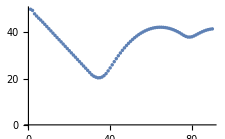
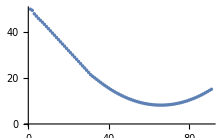
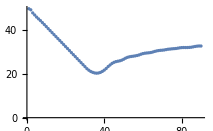

```mathematica
(* some visualizations *) 
ListPlot/@(tcRange[#]* Cos[tcHead[#]]&/@ datadirs[[4;;6]])
```

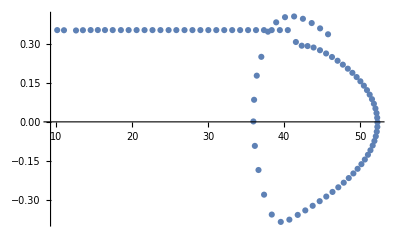
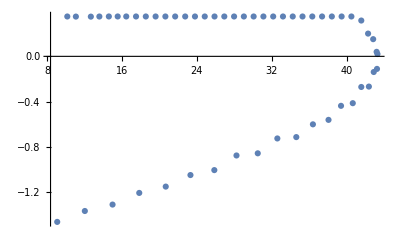
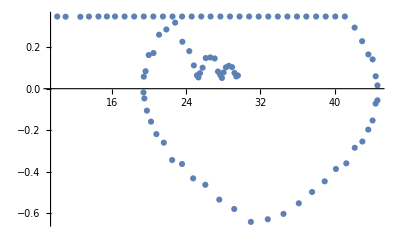

```mathematica
ListPlot/@( Transpose[{ tcRange[#]* Cos[tcHead[#]],tcHead[#] }]&/@ datadirs[[1;;3]])
```

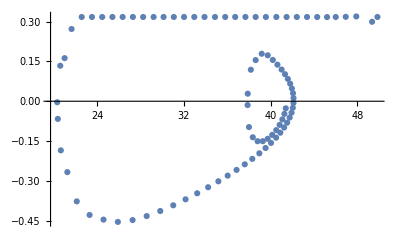
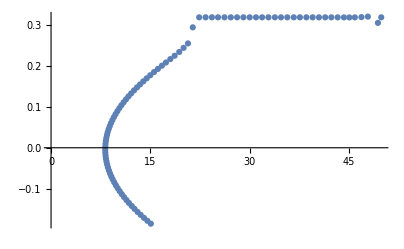
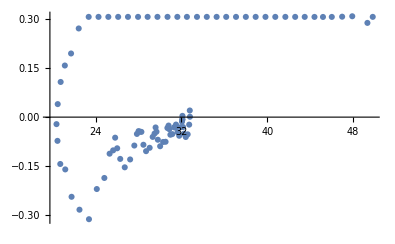

```mathematica
ListPlot/@( Transpose[{ tcRange[#]* Cos[tcHead[#]],-tcHead[#] }]&/@ datadirs[[4;;6]])
```

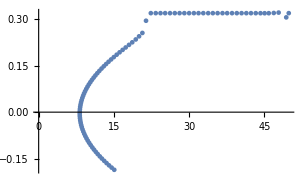

```mathematica
ListPlot/@( Transpose[{ tcRange[#]* Cos[tcHead[#]],-tcHead[#] }]&/@ {uuvResultsDir <> "/run_20deg_50m_061off"})
```

```mathematica
(*** MODELGUARD (aka MG/MON_2) RESULTS ANALYSIS ***)
```

```mathematica
mgStepSize = 3; (* the parameter with which MG was run - affects trace lengths *) 
runDirs = Select[FileNames[All,resultsDir],  DirectoryQ[#]&];
mgFiles001 = Flatten[Select[FileNames[All,#],  (StringTake[#,-17]== "mg_0.001_2_15.csv")&]&/@ runDirs ];
mgFiles0025 = Flatten[Select[FileNames[All,#],  (StringTake[#,-18]== "mg_0.0025_2_15.csv")&]&/@ runDirs ];
mgFiles004 = Flatten[Select[FileNames[All,#],  (StringTake[#,-17]== "mg_0.004_2_15.csv")&]&/@ runDirs ];
mgFiles005 = Flatten[Select[FileNames[All,#],  (StringTake[#,-17]== "mg_0.005_2_15.csv")&]&/@ runDirs ];
(*outcomeFiles = Select[FileNames[All,resultsDir],  StringTake[#,-7]== "out.csv"&];
mcFiles = Select[FileNames[All,resultsDir],  StringTake[#,-6]== "mc.csv"&];
mgFiles = Select[FileNames[All,resultsDir],  StringTake[#,-16]== "mg.csv"&];*)
```

```mathematica
mgConfs001 = getMgConfs@mgFiles001; 
mgConfs0025 = getMgConfs@mgFiles0025; 
mgConfs004 = getMgConfs@mgFiles004; 
mgConfs005 = getMgConfs@mgFiles005;
```

```mathematica
successes = {}; stepCounts = {};  noiseAssnHolds = {}; steepAssnHolds = {}; allAssnHolds = {}; steeps = {}; atLeastOneAssnHolds={};
( 
AppendTo[successes, (Import@#)[[(*first line *) 1,(*1st element: success wrt the goal *) 1]]];
AppendTo[stepCounts, (Import@#)[[(*first line *) 1,(*2nd element: step count *) 2]]];
AppendTo[noiseAssnHolds, (Import@#)[[(*second line *) 2,(*1st element: whether the verification assumptions hold *) 1]]];
AppendTo[steeps, (Import@#)[[(*second line *) 2,(*5th element: the steepness of the hill *) 5]]];
AppendTo[steepAssnHolds, ToString[steeps[[-1]] == 0.0025]] ;
AppendTo[allAssnHolds,ToString[ToExpression@noiseAssnHolds[[-1]] ∧ ToExpression@steepAssnHolds[[-1]]]];
AppendTo[atLeastOneAssnHolds,ToString[ToExpression@noiseAssnHolds[[-1]] ∨ ToExpression@steepAssnHolds[[-1]]]];
)&/@ outcomeFiles;
mcProbs = Flatten[Import@# & /@ mcFiles, (*flatten at 3rd level*){3}][[1]];
```

```mathematica
Mean[#[[1]]]&/@ {mgConfs001, mgConfs0025, mgConfs004, mgConfs005}
```

{0.133911,0.318879,0.701652,0.839544}

```mathematica
{Mean[#[[2]]],  Mean[#[[3]]]}&/@ {mgConfs001, mgConfs0025, mgConfs004, mgConfs005}
```

{{0.109531,0.117079},{0.274725,0.268579},{0.66099,0.656104},{0.882237,0.864597}}

```mathematica
verifiedState[y_, h_]:=(0≤h≤2.5 And 10.05≤y≤30) Or
 ( 13≤h≤13.5 And 12.35≤y≤30)
```

13≤h≤166.725 And≤y≤30

```mathematica
verifiedState[11,12]
```

False

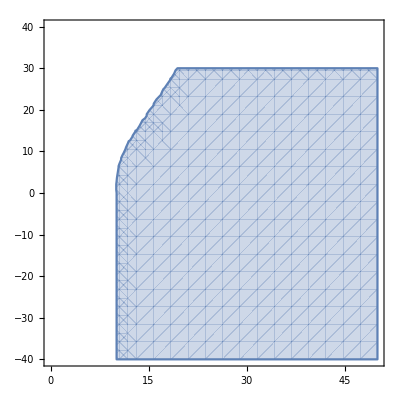

```mathematica
RegionPlot[verifiedUuvStateAll[y,h], {y, 0,50}, {h,-40, 40}]
```

```mathematica
(*** UUV TRIALS ANALYSIS ***)
```

```mathematica
loadUuvFilenames[uuvResultsDir]
loadAllUuvData[{1,2},4]
```

```mathematica
(* load just the last one to add monitor to it *) 
loadUuvFilenames[uuvResultsDir]
loadAllUuvData[{107},4]
```

$Aborted

```mathematica
saveCachedUuvStateMon[{trialDirs[[107]]}, stateMon]
```

{/home/ivan/uuv-mg-set7/trial_194/stateMon.csv}

```mathematica
saveCachedUuvStateMon[trialDirs, stateMon]
```

{/home/ivan/uuv-mg-set7b/trial_100/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_101/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_102/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_103/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_104/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_105/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_106/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_107/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_108/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_109/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_110/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_111/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_112/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_113/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_114/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_115/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_116/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_117/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_118/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_119/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_120/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_121/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_122/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_123/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_124/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_125/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_126/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_127/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_128/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_129/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_130/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_131/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_132/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_133/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_134/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_135/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_136/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_137/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_138/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_139/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_140/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_141/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_142/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_143/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_144/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_145/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_146/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_147/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_148/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_149/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_150/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_151/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_152/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_153/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_154/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_155/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_156/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_157/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_158/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_159/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_160/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_161/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_162/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_163/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_164/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_165/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_166/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_167/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_168/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_169/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_170/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_171/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_172/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_173/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_174/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_175/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_176/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_177/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_178/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_179/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_180/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_181/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_182/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_183/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_184/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_185/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_186/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_187/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_188/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_189/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_190/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_191/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_192/stateMon.csv,/home/ivan/uuv-mg-set7b/trial_193/stateMon.csv}

```mathematica
{Length@trialDirs
,Length@usingLec1
,Length@trueYs
,Length@pfRanges
,Length@pfHeadings
,Length@pfYs, 
Length@stateMonLoaded, 
Length@stateMon, 
Length@particleYHpairs,
Length@particleDists,
Length@particleHeads}
```

{194,194,194,0,0,0,194,1,1,0,0}

```mathematica
Length/@{uuvSafe, stateAssns, Not/@findist, stateMonLoaded, mgUuvConfs}
```

{194,194,194,194,194}

```mathematica
(* testing cached monitor *) 

loadUuvFilenames["/home/ivan/uuv-mg-set6-nominal/"]
loadSomeUuvData[Range[1,51] ,4]
```

```mathematica
loadUuvFilenames[uuvResultsDir]
loadSomeUuvData[Range[1,10] ,4]
```

```mathematica
organizeUuvData[uuvSafeties(*uuvSafe*), stateAssns, Not/@findist, stateMonLoaded, mgUuvConfs];
```

```mathematica
outM1Pairs =fixExtremeProbs2[Transpose@{ Flatten@ uuvSafeties,Flatten@stateMonLoaded}];
```

```mathematica
Dimensions/@uuvSafeties
```

{{42},{42},{42},{40},{41},{39},{41},{40},{41},{39}}

```mathematica
loadAndOrganizeUuvData[uuvResultsDir, Range[1,100]]
```

```mathematica
Dimensions/@stateMonLoaded
```

{{43},{43},{43},{41},{42},{40},{42},{41},{42},{40}}

```mathematica
doValidationTuning[False]
```

```mathematica
m1CalParams
```

{a→2.14531,b→-0.914193}

```mathematica
m2CalParams
```

{a→0.179226,b→0.0319517}

```mathematica
uuvSafe
```

{True,False,False,True,False,False,True,False,True,True}

```mathematica
Not/@findist
```

{False,False,False,False,False,False,False,False,False,False}

```mathematica
Flatten[pairElemWithList/@ Inner[List,  uuvSafe,stateMonLoaded, List],{1,2}]
```

```mathematica
stateMonLoaded
```

```mathematica
organizeUuvData[uuvSafe, stateAssns, Not/@findist, stateMonLoaded, mgUuvConfs];
```

```mathematica
(* Processing cached data *) 
loadAndOrganizeUUVData[uuvResultsDir,Range[1,194] ]
```

```mathematica
loadUuvFilenames[uuvResultsDir]
loadSomeUuvData[Range[1,Length@trialDirs] ,4]
```

$Aborted

```mathematica
doValidationTuning[False]
```

```mathematica
{m1CalParams, m2CalParams, lrParams}
```

{{a→-0.535769,b→-0.13703},{a→0.843231,b→166.056},{a→0.990926,b→0.155494,c→-0.0590116}}

```mathematica
addHeadingsToResultsMatrix@doTesting[]
```

General::munfl: (-4.43442×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.5829×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.50518×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.147907 | 0.413255 | -0.413255 | 0.14797 | 0.968063
Prod-outcome | 0.240744 | 0.524366 | -0.524366 | 0.24002 | 0.852845
Avg-assn | 0.0199519 | 0.46478 | -0.46478 | 0.08419 | 0.9641
Avg-outcome | 0.10876 | 0.536209 | -0.536209 | 0.16006 | 0.850916
AvgVar-assn | 0.0746028 | 0.46115 | -0.46115 | 0.07864 | 0.973637
AvgVar-outcome | 0.169659 | 0.532578 | -0.532578 | 0.15319 | 0.861007
LowCop-assn | 0.148458 | 0.413255 | -0.413255 | 0.14832 | 0.313321
LowCop-outcome | 0.241295 | 0.524366 | -0.524366 | 0.24041 | 0.301082
ProdSq-assn | 0.149191 | 0.307715 | -0.307715 | 0.15064 | 0.968063
ProdSq-outcome | 0.241294 | 0.418826 | -0.418826 | 0.24211 | 0.852845
LR-assn | 0.0176309 | 0.134784 | -0.108357 | 0.05079 | 0.982815
LR-outcome | 0.0981764 | 0.148297 | -0.148297 | 0.12077 | 0.873114
Bayes-assn | 0.150451 | 0.483861 | 0.00694987 | 0.13812 | 0.934216
Bayes-outcome | 0.0890835 | 0.579099 | 0.00694987 | 0.06605 | 0.994613)

```mathematica
a1andA2LrComp
```

{{True,0.300046},{True,0.285218},{True,0.305361},{True,0.36052},{True,0.759316},{True,0.884611},{True,0.938323},8101,{True,0.985046},{True,0.995425},{True,0.995425},{True,0.995425},{True,0.995425},{True,0.995425},{True,0.923838}}
 |  |  |  |

```mathematica
triplesLR
```

{{True,0.6636,0.073789},{True,0.646,0.050399},{True,0.7004,0.041758},{True,0.8024,0.039229},{True,0.9112,99999/100000},{True,0.986,99999/100000},8103,{True,99999/100000,99999/100000},{True,99999/100000,99999/100000},{True,99999/100000,99999/100000},{True,99999/100000,99999/100000},{True,99999/100000,99999/100000},{True,0.9996,0.122744}}
 |  |  |  |

```mathematica
outProdSqComp
```

{{True,0.0000247182},{True,3.46314×10^-6},{True,1.47447×10^-6},{True,1.17259×10^-6},{True,0.996636},{True,0.999966},{True,0.999999},8102,{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.000416839}}
 |  |  |  |

```mathematica
a1AndA2WeightAvgComp
```

{{True,0.49776},{True,0.488286},{True,0.50936},{True,0.530434},{True,0.999094},{True,0.999991},{True,1.},8101,{True,0.545615},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.547531}}
 |  |  |  |

```mathematica
a1M1CalPairs
```

{{True,0.920395},{True,0.905661},{True,0.945486},{True,0.984809},{True,0.998317},{True,0.999983},{True,1.},{True,1.},8100,{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.}}
 |  |  |  |

```mathematica
calibEvalShort@a1M1Pairs
```

{0.0261116,0.254387,-0.097185,0.01842,0.314535}

```mathematica
calibEvalShort@a1M1CalPairs
```

{0.00289807,0.220331,-0.0651931,0.01392,0.998421}

{0.0261116,0.254387,-0.097185,0.01842,0.314535}

```mathematica
calibEvalShort@a2M2Pairs
```

{0.193798,0.490162,-0.11518,0.20675,0.76392}

```mathematica
calibEvalShort@a2M2CalPairs
```

{0.225657,0.370301,-0.11519,0.2274,0.76392}

```mathematica
a1M1CalPairs
```

{{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{True,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203},{False,0.119203}}

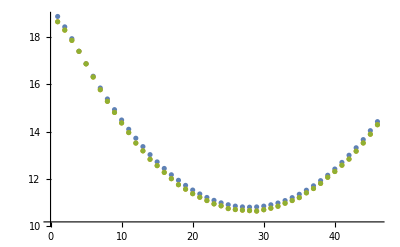
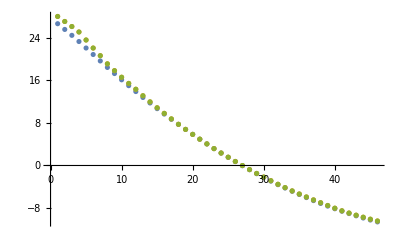

```mathematica
ListPlot [#] &/@Transpose[{trueYs,pfYs, Map[Mean, particleDists, {2}]}]
```

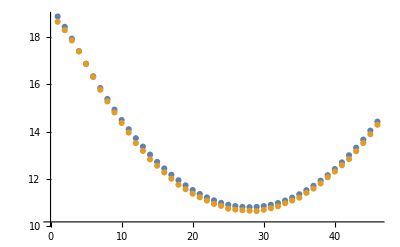
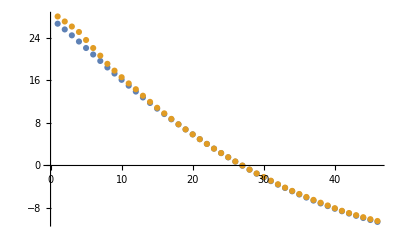

```mathematica
ListPlot [#] &/@Transpose[{trueYs,Map[Mean, particleYsfixed, {2}]}]
```

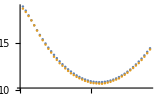
{-Graphics-,-Graphics-}

```mathematica
ListPlot [#] &/@Transpose[{trueYs,pfYs}]
```

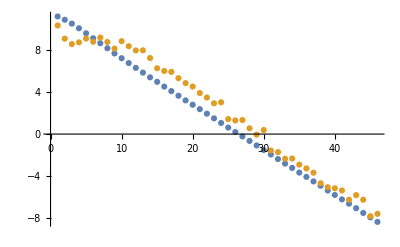
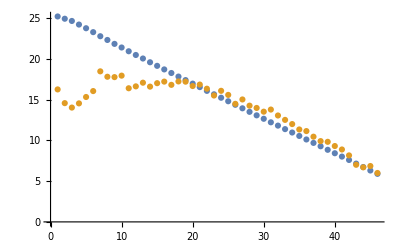

```mathematica
ListPlot [#] &/@Transpose[{trueHeads,Map[Mean, particleHeads, {2}]}]
```

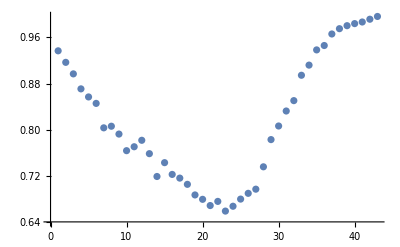
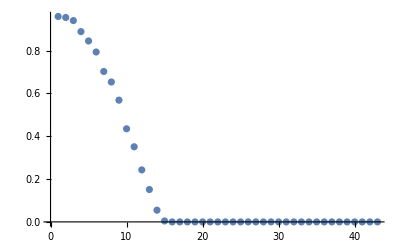
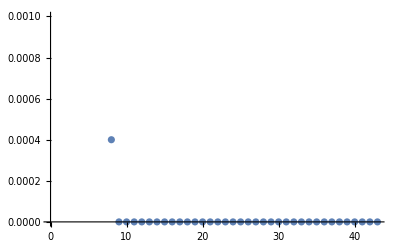
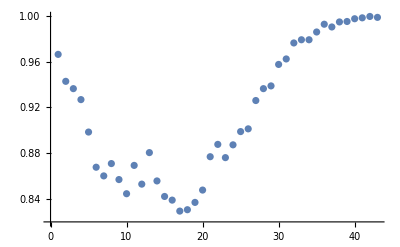
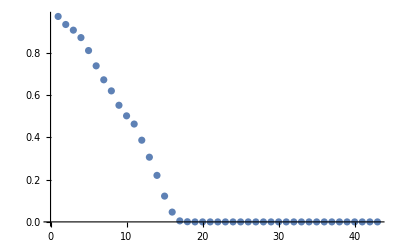
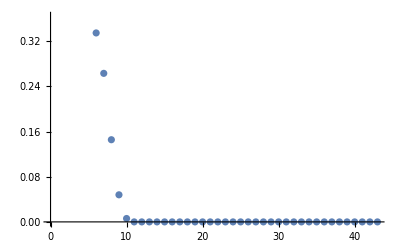
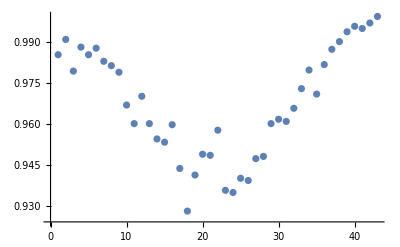
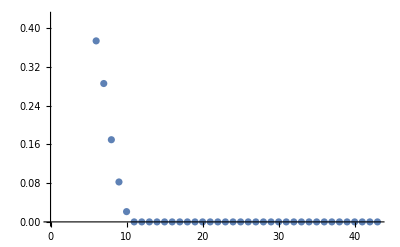

```mathematica
ListPlot/@stateMonLoaded
```

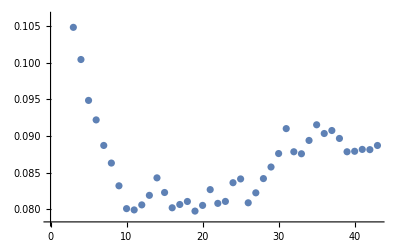
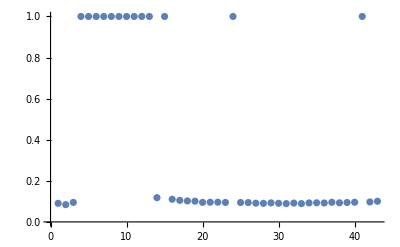
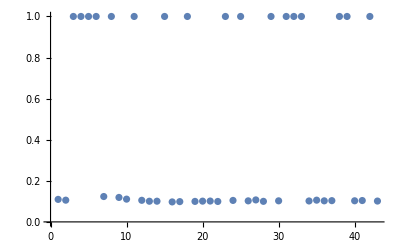
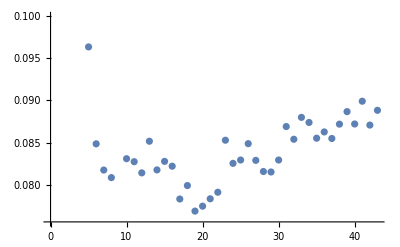
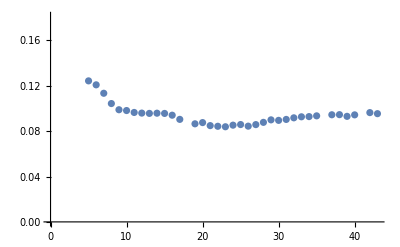
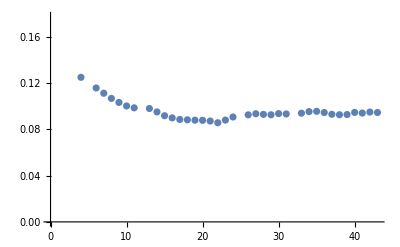
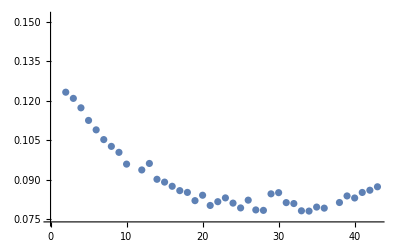
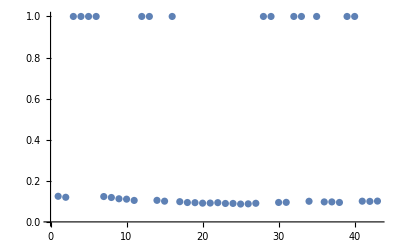
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot/@mgUuvConfs
```

```mathematica
stateMonLoaded
```

{{0.9368,0.9168,0.8968,0.8708,0.8568,0.8456,0.8032,0.806,0.7924,0.7636,0.7704,0.7816,0.7584,0.7188,0.7428,0.7224,0.716,0.7052,0.6868,0.6792,0.6684,0.6756,0.6588,0.6672,0.6796,0.6896,0.6968,0.7356,0.7828,0.8064,0.8324,0.8504,0.8944,0.912,0.9384,0.946,0.966,0.9752,0.9804,0.984,0.9868,0.9916,0.9964},{0.9592,0.9544,0.94,0.8884,0.8448,0.7932,0.7024,0.6532,0.5684,0.4348,0.3508,0.2428,0.1512,0.0548,0.0044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.72,0.6064,0.4536,0.3132,0.1764,0.0916,0.0264,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9664,0.9428,0.9364,0.9268,0.8984,0.8676,0.86,0.8708,0.8568,0.8444,0.8692,0.8528,0.8804,0.8556,0.842,0.8388,0.8292,0.8304,0.8368,0.8476,0.8768,0.8876,0.876,0.8872,0.8988,0.9012,0.926,0.9364,0.9388,0.9576,0.9624,0.9764,0.9792,0.9792,0.986,0.9928,0.9904,0.9948,0.9952,0.9976,0.9984,0.9996,0.9988},{0.9716,0.9336,0.9068,0.8716,0.8104,0.738,0.672,0.6196,0.5516,0.5016,0.4628,0.3864,0.306,0.22,0.122,0.0464,0.0048,0.0008,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.7824,0.7272,0.6232,0.5548,0.4296,0.3348,0.2632,0.1456,0.048,0.006,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9852,0.9908,0.9792,0.988,0.9852,0.9876,0.9828,0.9812,0.9788,0.9668,0.96,0.97,0.96,0.9544,0.9532,0.9596,0.9436,0.928,0.9412,0.9488,0.9484,0.9576,0.9356,0.9348,0.94,0.9392,0.9472,0.948,0.96,0.9616,0.9608,0.9656,0.9728,0.9796,0.9708,0.9816,0.9872,0.99,0.9936,0.9956,0.9948,0.9968,0.9992},{0.8528,0.7968,0.6928,0.5816,0.502,0.3736,0.2856,0.1696,0.0824,0.0212,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9868,0.9792,0.98,0.9752,0.972,0.9652,0.9452,0.9296,0.9176,0.9012,0.8928,0.9064,0.888,0.8888,0.8688,0.8696,0.844,0.836,0.8548,0.8428,0.846,0.8472,0.8408,0.856,0.8556,0.8436,0.8472,0.858,0.8668,0.8888,0.8888,0.8868,0.8988,0.9028,0.9144,0.944,0.9564,0.9656,0.9656,0.9772,0.984,0.988,0.99},{0.9636,0.944,0.9268,0.9136,0.9084,0.892,0.8796,0.8448,0.8548,0.8448,0.8388,0.802,0.8024,0.8256,0.7972,0.82,0.838,0.8056,0.802,0.7956,0.7984,0.8356,0.8164,0.8172,0.8336,0.8452,0.8384,0.8756,0.8888,0.8956,0.9176,0.9396,0.948,0.9612,0.9648,0.9856,0.9832,0.9852,0.9824,0.9948,0.9972,0.9972,0.9988},{0.6576,0.4956,0.35,0.228,0.1012,0.0348,0.002,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9732,0.974,0.9696,0.9676,0.9512,0.9252,0.9072,0.8668,0.8424,0.8028,0.7336,0.6772,0.6228,0.5428,0.5144,0.458,0.414,0.3172,0.2332,0.132,0.0536,0.0064,0.002,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.8588,0.77,0.676,0.5012,0.3944,0.272,0.18,0.0876,0.0216,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9484,0.9372,0.918,0.9072,0.8544,0.796,0.6836,0.6408,0.574,0.4912,0.43,0.3608,0.2804,0.1844,0.092,0.0256,0.0024,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9808,0.962,0.96,0.9688,0.944,0.9328,0.9264,0.9,0.8408,0.7956,0.7548,0.6888,0.6448,0.6048,0.5424,0.4956,0.4388,0.388,0.2724,0.1768,0.1,0.0292,0.0052,0.0004,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.7124,0.6096,0.4676,0.3476,0.2268,0.1364,0.0464,0.0024,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.6624,0.5544,0.3716,0.2436,0.1456,0.0456,0.0036,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9704,0.9496,0.9412,0.9012,0.8868,0.8184,0.7524,0.6792,0.5816,0.5504,0.44,0.3844,0.2972,0.2204,0.0976,0.0228,0.0036,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9724,0.9804,0.9472,0.9536,0.9092,0.8808,0.856,0.8184,0.774,0.7048,0.6496,0.6248,0.5452,0.5188,0.4424,0.37,0.3144,0.206,0.1084,0.048,0.0084,0.002,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.968,0.976,0.9412,0.9236,0.904,0.8296,0.8048,0.7424,0.7228,0.6916,0.6508,0.6296,0.5416,0.5012,0.4416,0.3636,0.2808,0.1804,0.076,0.0304,0.0068,0.0024,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9748,0.958,0.9624,0.9584,0.9336,0.9072,0.8788,0.8376,0.8028,0.7564,0.7344,0.6536,0.632,0.5632,0.4868,0.4444,0.3704,0.3092,0.2196,0.124,0.0372,0.0104,0.002,0.0016,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9928,0.9888,0.9836,0.9772,0.9764,0.982,0.9868,0.9868,0.9848,0.9744,0.9804,0.9772,0.9736,0.9584,0.974,0.9616,0.9672,0.9512,0.9552,0.9708,0.9632,0.9592,0.9648,0.9612,0.9588,0.9664,0.9656,0.9636,0.972,0.9752,0.9848,0.9836,0.9856,0.986,0.9892,0.9904,0.9932,0.9928,0.998,0.9984,0.9988,0.9988,1.},{0.8856,0.8732,0.8576,0.7932,0.724,0.6904,0.6272,0.578,0.5116,0.4596,0.3968,0.318,0.2152,0.112,0.0312,0.0108,0.0012,0.0008,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9844,0.9728,0.9712,0.94,0.934,0.9352,0.9044,0.9024,0.888,0.8824,0.898,0.8508,0.8628,0.8748,0.8636,0.8356,0.8324,0.8412,0.838,0.83,0.8572,0.8292,0.834,0.8456,0.8484,0.854,0.8884,0.8892,0.8724,0.8928,0.9256,0.9304,0.9556,0.9536,0.9684,0.9712,0.9752,0.974,0.9852,0.9916,0.9884,0.9928,0.9972},{0.8812,0.8468,0.7408,0.6652,0.5548,0.4352,0.3384,0.2512,0.1356,0.0628,0.0076,0.0008,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9868,0.9912,0.9848,0.9704,0.9812,0.9716,0.962,0.938,0.9304,0.932,0.9012,0.8864,0.8824,0.8672,0.8544,0.8252,0.8384,0.8132,0.8216,0.8076,0.808,0.7672,0.7752,0.7396,0.7376,0.742,0.7792,0.7764,0.7708,0.7416,0.76,0.7544,0.7752,0.7792,0.7696,0.7908,0.836,0.8464,0.8652,0.8872,0.9056,0.9276,0.9388},{0.9912,0.9888,0.9784,0.9732,0.9604,0.948,0.9272,0.9092,0.892,0.8872,0.8656,0.8724,0.8448,0.8288,0.8024,0.776,0.7392,0.7196,0.7056,0.6936,0.696,0.6648,0.65,0.6508,0.6316,0.6112,0.5724,0.5588,0.572,0.536,0.5108,0.48,0.4764,0.464,0.4844,0.5104,0.5388,0.594,0.6284,0.666,0.732,0.7868,0.8464},{0.9296,0.9228,0.8696,0.7844,0.6804,0.584,0.4436,0.3212,0.2016,0.1216,0.0476,0.0028,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.8508,0.7752,0.6004,0.4564,0.3212,0.1856,0.0612,0.024,0.0012,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98,0.9644,0.9584,0.9476,0.932,0.9316,0.9256,0.9056,0.908,0.9004,0.9172,0.9232,0.9224,0.9164,0.9032,0.9148,0.9072,0.916,0.9188,0.9132,0.9192,0.9112,0.9228,0.9476,0.95,0.9568,0.9664,0.9724,0.9756,0.9832,0.9804,0.9892,0.9896,0.9916,0.994,0.9984,0.9996,1.,0.9992,0.9992,1.,0.9992,1.},{0.9708,0.9416,0.9276,0.906,0.868,0.8064,0.778,0.726,0.6772,0.6672,0.6132,0.576,0.5432,0.4964,0.444,0.4004,0.2796,0.19,0.1088,0.05,0.012,0.006,0.0004,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.98,0.972,0.9548,0.936,0.884,0.8176,0.77,0.7072,0.6484,0.5896,0.5172,0.4264,0.3848,0.2988,0.1596,0.0536,0.0064,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9792,0.9816,0.9704,0.9636,0.9656,0.9564,0.9304,0.922,0.9056,0.8688,0.8192,0.7888,0.7348,0.716,0.674,0.6128,0.558,0.5004,0.4636,0.3972,0.3044,0.2192,0.124,0.0376,0.0112,0.0024,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9876,0.986,0.9876,0.9884,0.976,0.978,0.9748,0.9756,0.9748,0.9756,0.9744,0.9664,0.9528,0.95,0.9556,0.9572,0.9488,0.9444,0.944,0.9572,0.9556,0.9544,0.9728,0.9712,0.972,0.966,0.9764,0.9788,0.9752,0.9824,0.9872,0.9892,0.9908,0.9884,0.9944,0.9948,0.9984,0.998,0.9988,0.9992,1.,1.,1.},{0.8288,0.6948,0.6224,0.4476,0.2728,0.184,0.1032,0.022,0.0012,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9936,0.9912,0.9892,0.9812,0.9728,0.968,0.9564,0.962,0.96,0.95,0.9624,0.9516,0.95,0.9428,0.94,0.9432,0.9468,0.9548,0.9448,0.9516,0.948,0.9492,0.956,0.96,0.9692,0.9732,0.9764,0.974,0.9736,0.9836,0.9836,0.9892,0.9904,0.9948,0.9972,0.9968,0.9956,0.9972,0.9992,0.9976,0.9988,0.9976,1.},{0.9728,0.9736,0.96,0.9424,0.8972,0.8924,0.8588,0.856,0.8424,0.8036,0.788,0.762,0.7516,0.7152,0.686,0.6912,0.6584,0.6196,0.6136,0.5656,0.492,0.4532,0.3948,0.3328,0.2448,0.2092,0.1752,0.1396,0.1308,0.0868,0.0752,0.0612,0.0608,0.0696,0.0816,0.0944,0.128,0.1748,0.2296,0.2828,0.3976,0.5112,0.6312},{0.8464,0.7684,0.7136,0.6436,0.5648,0.4448,0.3784,0.2836,0.2076,0.1188,0.0316,0.0056,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9876,0.99,0.9812,0.9748,0.9896,0.9856,0.9796,0.966,0.9572,0.9644,0.9616,0.9364,0.9092,0.9136,0.8888,0.8948,0.8896,0.85,0.8576,0.8744,0.8736,0.8712,0.8324,0.8388,0.8424,0.818,0.8212,0.8328,0.8176,0.8448,0.8396,0.8464,0.8468,0.8464,0.8576,0.86,0.88,0.9128,0.9288,0.9252,0.9356,0.9408,0.9536},{0.992,0.9944,0.9936,0.9952,0.9852,0.9928,0.9852,0.9824,0.9856,0.986,0.9884,0.9896,0.992,0.992,0.9932,0.9904,0.9936,0.9904,0.9972,0.9964,0.9944,0.9948,0.9976,0.9992,0.9988,0.9992,0.9996,0.9996,0.9996,0.998,0.9996,0.9996,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.87,0.8548,0.822,0.7604,0.7364,0.6368,0.6296,0.6144,0.5488,0.5076,0.444,0.3576,0.2712,0.1884,0.0888,0.0284,0.0092,0.0032,0.0004,0.0004,0.,0.,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0004,0.0004},{0.996,0.994,0.9932,0.9944,0.9948,0.998,0.9932,0.9924,0.9968,0.9976,0.9984,0.9936,0.9912,0.9968,0.9976,0.9988,0.9976,0.9988,0.9984,0.9992,1.,1.,1.,0.9996,0.9996,1.,1.,0.9996,0.9996,1.,1.,1.,1.,1.,0.9992,1.,1.,1.,1.,1.,1.,1.,1.},{0.9876,0.9932,0.9924,0.9968,0.9944,0.9784,0.9844,0.9896,0.9824,0.9896,0.9908,0.9928,0.994,0.994,0.9936,0.996,0.9936,0.9916,0.9936,0.9944,0.9924,0.996,0.9984,0.996,0.9976,0.9988,0.9964,0.9964,0.998,0.9992,0.9996,1.,0.9984,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.9624,0.9612,0.922,0.872,0.8184,0.7384,0.6904,0.5568,0.5164,0.458,0.4056,0.34,0.224,0.144,0.0656,0.0136,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9668,0.9704,0.9576,0.9344,0.8968,0.8464,0.8192,0.7648,0.6972,0.6328,0.5832,0.548,0.4396,0.4016,0.3072,0.2032,0.1132,0.0368,0.0068,0.0008,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.97,0.9624,0.956,0.9564,0.9432,0.9424,0.9576,0.9548,0.9552,0.9536,0.9544,0.9512,0.9568,0.9636,0.978,0.9672,0.9704,0.9692,0.9816,0.9896,0.99,0.986,0.9896,0.9932,0.9932,0.9956,0.9972,0.9968,0.9996,0.9996,0.9996,1.,0.9996,0.9996,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.9724,0.968,0.9652,0.9456,0.9504,0.9564,0.9528,0.9452,0.9328,0.9512,0.9392,0.9576,0.952,0.962,0.9636,0.9696,0.9648,0.9548,0.9768,0.9828,0.9772,0.986,0.988,0.9912,0.996,0.996,0.9972,0.9996,0.9984,0.9996,0.9996,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.9596,0.9492,0.9456,0.9104,0.8536,0.76,0.666,0.5996,0.508,0.41,0.322,0.208,0.0928,0.0264,0.0016,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.96,0.9388,0.8972,0.8652,0.8196,0.7464,0.6916,0.62,0.5776,0.5152,0.4476,0.3764,0.2828,0.1924,0.0884,0.0248,0.0016,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.882,0.8564,0.7848,0.6976,0.592,0.504,0.4292,0.3272,0.2264,0.1504,0.0712,0.0124,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.992,0.9968,0.9904,0.9908,0.994,0.994,0.988,0.9904,0.9908,0.9904,0.9876,0.9932,0.9844,0.988,0.9928,0.9916,0.9968,0.9944,0.9916,0.9952,0.9948,0.9928,0.9964,0.9984,0.9996,0.9992,0.9956,0.9996,0.9996,1.,0.9996,1.,0.9996,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.986,0.9788,0.9788,0.972,0.962,0.9552,0.9484,0.9284,0.9232,0.9072,0.91,0.874,0.878,0.8592,0.8596,0.8396,0.8428,0.8608,0.8624,0.8504,0.8364,0.84,0.8448,0.8512,0.8464,0.8716,0.8472,0.858,0.8792,0.88,0.9136,0.9252,0.9228,0.9452,0.944,0.9552,0.956,0.9696,0.9744,0.9844,0.9864,0.9884,0.99},{0.966,0.9584,0.968,0.9648,0.9536,0.9316,0.8804,0.8268,0.768,0.7232,0.6512,0.5732,0.488,0.4312,0.3284,0.2452,0.1524,0.0528,0.0068,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.986,0.986,0.9864,0.9828,0.9732,0.966,0.9632,0.964,0.9476,0.942,0.9396,0.9508,0.9464,0.9432,0.9444,0.9572,0.9568,0.9396,0.9312,0.9656,0.9668,0.9564,0.9624,0.9552,0.96,0.97,0.9724,0.9732,0.982,0.984,0.9908,0.9904,0.9948,0.9988,0.9968,0.9996,0.9976,0.9976,0.9996,0.9996,0.9996,1.,1.},{0.9852,0.9752,0.9804,0.98,0.9808,0.9792,0.962,0.9664,0.9376,0.9392,0.9344,0.9004,0.8972,0.8684,0.8508,0.8328,0.8312,0.8072,0.7892,0.7728,0.768,0.7476,0.7144,0.7,0.6856,0.6712,0.6552,0.6236,0.6332,0.5728,0.5624,0.5424,0.5296,0.4956,0.4832,0.4824,0.4844,0.4752,0.4812,0.4988,0.5308,0.562,0.6112},{0.9948,0.9976,0.9976,0.9936,0.9956,0.9908,0.9976,0.9984,0.998,0.9988,0.998,0.9992,0.9992,0.9984,0.9972,0.9992,0.9988,0.9996,1.,0.9992,1.,0.9996,0.9992,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.7084,0.5812,0.4796,0.3632,0.262,0.1736,0.0692,0.0092,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9556,0.9376,0.924,0.876,0.838,0.8016,0.7776,0.7336,0.698,0.6732,0.6528,0.6096,0.5912,0.5888,0.5232,0.49,0.3964,0.3584,0.2748,0.178,0.1072,0.06,0.0348,0.016,0.0108,0.0036,0.0036,0.0024,0.0012,0.0036,0.0004,0.0008,0.0024,0.0012,0.0024,0.0032,0.0052,0.0048,0.008,0.0076,0.0252,0.0404,0.084},{0.9288,0.9036,0.8728,0.8196,0.7368,0.7072,0.678,0.6164,0.5824,0.5236,0.446,0.4176,0.3292,0.2568,0.1644,0.0752,0.0188,0.0044,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9892,0.9884,0.9852,0.986,0.9856,0.9828,0.9796,0.9632,0.9564,0.968,0.9528,0.95,0.9336,0.948,0.9568,0.938,0.9456,0.9492,0.9412,0.9452,0.9532,0.9456,0.962,0.9668,0.9676,0.9624,0.974,0.9804,0.9808,0.982,0.9896,0.9888,0.9932,0.9952,0.9964,0.9968,0.9968,1.,0.9996,1.,0.9988,1.,1.},{0.9972,0.9984,0.998,0.9984,0.998,0.9932,0.998,0.998,0.9976,0.9964,0.9968,0.9988,0.9992,0.9988,0.998,0.9968,0.9992,0.9992,0.9996,0.9992,1.,1.,0.9992,1.,0.9996,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.6476,0.5284,0.366,0.2364,0.1132,0.0236,0.0012,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9456,0.9332,0.8932,0.8888,0.8788,0.8396,0.8188,0.7908,0.736,0.6916,0.6592,0.6184,0.6448,0.5876,0.5636,0.5212,0.4692,0.4192,0.342,0.242,0.18,0.1132,0.066,0.0296,0.02,0.0096,0.0036,0.006,0.0028,0.0036,0.002,0.0016,0.0012,0.0016,0.004,0.004,0.006,0.006,0.0088,0.0132,0.0332,0.0592,0.1064},{0.9748,0.9708,0.9368,0.8968,0.8632,0.816,0.7384,0.6984,0.6356,0.6048,0.5636,0.4988,0.4304,0.3432,0.2548,0.1652,0.0728,0.0212,0.0036,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.9508,0.9312,0.87,0.8092,0.7312,0.6376,0.5632,0.4432,0.3716,0.276,0.1824,0.0868,0.0208,0.0008,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.946,0.9176,0.8744,0.8528,0.7928,0.714,0.6772,0.668,0.5948,0.582,0.506,0.4436,0.3572,0.2552,0.17,0.0888,0.034,0.0032,0.0004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
stateAssns
```

{{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True},{True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}}

```mathematica
Dimensions@{stateAssns, stateMonLoaded}
```

{2,66,43}

```mathematica
Dimensions@Transpose[{stateAssns, stateMonLoaded}, {3,1,2}]
```

{66,43,2}

```mathematica
organizeUuvData
```

```mathematica
organizeUuvData[uuvSafe, stateAssns, Not/@findist, stateMonLoaded, mgUuvConfs];
```

```mathematica
Not/@findist
```

{False,False,False}

```mathematica
Dimensions@a1M1Pairs
```

{129,2}

```mathematica
a1M1Pairs
```

{{True,0.9368},{True,0.9168},{True,0.8968},{True,0.8708},{True,0.8568},{True,0.8456},{True,0.8032},{True,0.806},{True,0.7924},{True,0.7636},{True,0.7704},{True,0.7816},{True,0.7584},{True,0.7188},{True,0.7428},{True,0.7224},{True,0.716},{True,0.7052},{True,0.6868},{True,0.6792},{True,0.6684},{True,0.6756},{True,0.6588},{True,0.6672},{True,0.6796},{True,0.6896},{True,0.6968},{True,0.7356},{True,0.7828},{True,0.8064},{True,0.8324},{True,0.8504},{True,0.8944},{True,0.912},{True,0.9384},{True,0.946},{True,0.966},{True,0.9752},{True,0.9804},{True,0.984},{True,0.9868},{True,0.9916},{True,0.9964},{True,0.9592},{True,0.9544},{True,0.94},{True,0.8884},{True,0.8448},{True,0.7932},{True,0.7024},{False,0.6532},{False,0.5684},{False,0.4348},{False,0.3508},{False,0.2428},{False,0.1512},{False,0.0548},{False,0.0044},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,0.72},{False,0.6064},{False,0.4536},{False,0.3132},{False,0.1764},{False,0.0916},{False,0.0264},{False,0.0004},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000},{False,1/100000000}}

```mathematica
Dimensions@a2M2Pairs
```

{86,2}

```mathematica
Map[And,Transpose@{a1M1Pairs[[All,1]], a2M2Pairs[[All,1]]},{2}]
```

```mathematica
nll@sigPairs[logOddsPairs[a1M1Pairs], a, b]
```

```mathematica
calibrateMon[a1M1Pairs,0<a<2∧ 0<b<2.5]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→0.0485452,b→2.5}

```mathematica
calibrateMon[a2M2Pairs,0<a∧0<b]
```

{a→22.0153,b→2335.7}

```mathematica
m2CalParams
```

{a,b}

```mathematica
m1CalParams
```

{a→1.84889×10^-32,b→2.}

```mathematica
m2CalParams
```

{a→112.376,b→3167.7}

```mathematica
doValidationTuning[False]
```

```mathematica
lrParams
```

{a→308.508,b→-1.05768,c→135.993}

```mathematica
calibEvalShort@a1M1Pairs
calibEvalShort@a1M1CalPairs
```

{0.457425,0.971196,-0.971196,0.02622,0.500116}

{0.102275,0.278092,-0.278092,0.34899,0.500116}

```mathematica
calibEvalShort@a2M2Pairs
calibEvalShort@a2M2CalPairs
```

{0.259622,1.,-1.,0.19164,0.500116}

{0.137921,0.278092,-0.278092,0.02347,0.500116}

```mathematica
composeMons[outM1Pairs, outM2Pairs,#1&, Max[0,#1+#2-1]&]
```

```mathematica
calibEvalShort/@{
a1AndA2ProdComp,
outProdComp,
a1AndA2AvgComp, 
outAvgComp,
a1AndA2WeightAvgComp,
outWeightAvgComp,
a1AndA2CopBounComp, 
outCopBounComp,
a1AndA2ProdSqComp,
outProdSqComp,
a1andA2LrComp,
outLrComp(*,
a1andA2BayesComp,
outBayesComp*)
}// MatrixForm
```

General::munfl: 10. 6.438882521679×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 10. 1.65788165654×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 10. 3.365303821414×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(* FIXING CALIBRATION *)
```

```mathematica
loadAndOrganizeUUVData[uuvResultsDir,Range[1,194] ]
```

```mathematica
nllW[pairs_,consW_] := Plus@@With[{preppedPairs = pairs /.{"True"->1, "False"->0, True->1, False->0 }}, 
-Log[(1-consW)*#[[1]]*#[[2]] + consW*(1-#[[1]])*(1-#[[2]])]&/@preppedPairs
];
```

```mathematica
nllNew[pairs_] := Plus@@With[{preppedPairs = pairs /.{"True"->1, "False"->0, True->1, False->0 }}, 
-#[[1]]*Log[#[[2]]] - (1-#[[1]])*Log[1-#[[2]]]&/@preppedPairs
];
```

```mathematica
nllNewW[pairs_,consW_] := Plus@@With[{preppedPairs = pairs /.{"True"->1, "False"->0, True->1, False->0 }}, 
-(1-consW)*#[[1]]*Log[#[[2]]] - consW*(1-#[[1]])*Log[1-#[[2]]]&/@preppedPairs
];
```

```mathematica
nll@a1M1Pairs
```

263.064

```mathematica
nllNew@a1M1Pairs
```

94.3381

```mathematica
normParams1 = Minimize[nllNew[sigPairs[logOddsPairs[a1M1Pairs], a, b]], {a,b}] [[2]]
```

{a→2.65943,b→-0.882493}

```mathematica
weightParams1 = Minimize[nllNewW[sigPairs[logOddsPairs[a1M1Pairs], a, b],0.75], {a,b}] [[2]]
```

{a→2.49467,b→0.21922}

```mathematica
normParams2 = Minimize[nllNew[sigPairs[logOddsPairs[a2M2Pairs], a, b]], {a,b}] [[2]]
```

{a→0.177467,b→0.128527}

```mathematica
weightParams2 = Minimize[nllNewW[sigPairs[logOddsPairs[a2M2Pairs], a, b],0.75], {a,b}] [[2]]
```

{a→0.177773,b→1.22808}

```mathematica
calibrateMon[a1M1Pairs, 0.5]
```

{a→2.65943,b→-0.882493}

```mathematica
calibrateMon[a1M1Pairs, 0.75]
```

{a→2.49467,b→0.21922}

```mathematica
a1M1CalPairs= sigPairs[logOddsPairs[a1M1Pairs],a/.normParams1, b/.normParams1];
a1M1CalWPairs= sigPairs[logOddsPairs[a1M1Pairs],a/.weightParams1, b/.weightParams1];
outM1CalPairs= sigPairs[logOddsPairs[outM1Pairs],a/.normParams1, b/.normParams1];
outM1CalWPairs= sigPairs[logOddsPairs[outM1Pairs],a/.weightParams1, b/.weightParams1];
```

```mathematica
a1M2CalPairs= sigPairs[logOddsPairs[a2M2Pairs],a/.normParams2, b/.normParams2];
a2M2CalWPairs= sigPairs[logOddsPairs[a2M2Pairs],a/.weightParams2, b/.weightParams2];
outM2CalPairs= sigPairs[logOddsPairs[outM2Pairs],a/.normParams2, b/.normParams2];
outM2CalWPairs= sigPairs[logOddsPairs[outM2Pairs],a/.weightParams2, b/.weightParams2];
```

```mathematica
PrintTemporary["Calibrating M1"];
m1CalParams =calibrateMon[a1M1Pairs];
```

```mathematica
m1CalParams
```

{a→2.38788,b→-0.825457}

```mathematica
PrintTemporary["Calibrating M2"];
m2CalParams =calibrateMon[a2M2Pairs,  0<a∧0<b];
```

```mathematica
m2CalParams
```

{a→0.180772,b→0.21021}

```mathematica
m2CalParams
```

{a→0.180772,b→0.21021}

```mathematica
PrintTemporary["Calibrating M1"];
m1CalParams =calibrateMon[a1M1Pairs]; 
PrintTemporary["Calibrating M2"];
m2CalParams =calibrateMon[a2M2Pairs(*,  0<a∧0<b*)];
```

```mathematica
calibEvalShort/@{a1M1Pairs, a1M1CalPairs}
```

{{0.0281491,0.249476,-0.117288,0.01852,0.299481},{0.00487988,0.152805,-0.149983,0.01368,0.998553}}

```mathematica
calibEvalShort/@{a2M2Pairs, a2M2CalPairs}
```

{{0.187685,0.461801,-0.132771,0.20442,0.775875},{0.224712,0.337225,-0.132781,0.22592,0.775875}}

```mathematica
calibrateMon[a2M2Pairs]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b} = {2.43892,-80.5376}.

{a→-10.0672,b→452.155}

```mathematica
calibrateMon[a2M2Pairs,  0<a∧0<b]
```

{a→112.376,b→3167.7}

```mathematica
Minimize[nll[sigPairs[logOddsPairs[a1M1Pairs], a, b]], {a,b}]
```

{0.,{a→1.1698,b→92.4952}}

```mathematica
Minimize[nll[sigPairs[logOddsPairs[a2M2Pairs], a, b]], {a,b}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b} = {2.43892,-80.5376}.

{0.,{a→-10.0672,b→452.155}}

```mathematica
Minimize[{nll[sigPairs[logOddsPairs[a1M1Pairs], a]],a>0}, {a}]
```

```mathematica
nll[sigPairs[logOddsPairs[a1M1Pairs], 1,0]]
```

```mathematica
75568.68[a1M1Pairs]
```

```mathematica
Minimize[{nll[sigPairs[logOddsPairs[a1M1Pairs], a]],a≥1}, {a}]
```

{5624.89,{a→1.2039×10^18}}

```mathematica
Minimize[{nll[sigPairs[logOddsPairs[a2M2Pairs], a]],a≥1}, {a}]
```

{5624.89,{a→3.8115×10^8}}

```mathematica
N@Log[99999999]
```

18.4207

```mathematica
(* testing evals *) 
doUuvEvals[uuvResultsDir, 1, 0.5]
```

General::munfl: (-4.43442×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.5829×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.50518×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{0.147907,0.413255,-0.413255,0.14797,0.968063},{0.240744,0.524366,-0.524366,0.24002,0.852845},{0.0199519,0.46478,-0.46478,0.08419,0.9641},{0.10876,0.536209,-0.536209,0.16006,0.850916},{0.0746028,0.46115,-0.46115,0.07864,0.973637},{0.169659,0.532578,-0.532578,0.15319,0.861007},{0.148458,0.413255,-0.413255,0.14832,0.313321},{0.241295,0.524366,-0.524366,0.24041,0.301082},{0.149191,0.307715,-0.307715,0.15064,0.968063},{0.241294,0.418826,-0.418826,0.24211,0.852845},{0.0176309,0.134784,-0.108357,0.05079,0.982815},{0.0981764,0.148297,-0.148297,0.12077,0.873114},{0.150451,0.483861,0.00694987,0.13812,0.934216},{0.0890835,0.579099,0.00694987,0.06605,0.994613}}}

```mathematica
(* after fixing Bayes and function names *) 
addHeadingsToResultsMatrix@Mean@doUuvEvals[uuvResultsDir, 1, 0.5]
```

General::munfl: 1.0193×10^-294 2.17692×10^-15 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.70171×10^-300 2.17692×10^-15 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.53141×10^-297 2.17692×10^-15 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.144386 | 0.427579 | -0.427579 | 0.14334 | 0.967938
Prod-outcome | 0.248845 | 0.575636 | -0.575636 | 0.24642 | 0.858321
Avg-assn | 0.0300968 | 0.50879 | -0.50879 | 0.08582 | 0.964002
Avg-outcome | 0.114373 | 0.565537 | -0.565537 | 0.15903 | 0.856998
AvgVar-assn | 0.073005 | 0.511696 | -0.511696 | 0.08023 | 0.972377
AvgVar-outcome | 0.179026 | 0.536489 | -0.536489 | 0.15097 | 0.866169
LowCop-assn | 0.145139 | 0.427579 | -0.427579 | 0.14381 | 0.342372
LowCop-outcome | 0.249599 | 0.575636 | -0.575636 | 0.24698 | 0.304807
ProdSq-assn | 0.145554 | 0.383395 | -0.383395 | 0.14707 | 0.967938
ProdSq-outcome | 0.249358 | 0.550061 | -0.550061 | 0.25006 | 0.858321
LR-assn | 0.0282163 | 0.197831 | -0.197831 | 0.05463 | 0.980989
LR-outcome | 0.0971151 | 0.148233 | -0.148233 | 0.11361 | 0.880086
Bayes-assn | 0.252897 | 0.491275 | -0.056785 | 1.75665×10^57 | 0.860766
Bayes-outcome | 0.116182 | 0.510505 | -0.0914898 | 1.75665×10^57 | 0.919619)

```mathematica
traces = applyBayesHist[0.5,#, jointHistAssnSat,jointHistAll]& /@(m1M2sByRun);
```

```mathematica
jointHistAssnNotSat = normalizeHist@HistogramList[Transpose@{ Pick[Flatten@m1sByRun,Not/@ToExpression@a1AndA2ByPoint],  Pick[Flatten@m2sByRun,Not/@ToExpression@a1AndA2ByPoint]}, {{0,1.05,0.05},{0,1.05,0.05}},"Probability"];
```

```mathematica
?applyBayesFix
```

```mathematica
traces2 = applyBayesFix[0.5,#, jointHistAssnSat,jointHistAssnNotSat]& /@(m1M2sByRun);
```

```mathematica
Histogram@Flatten@traces2
```

-Graphics-

```mathematica
a1andA2BayesComp =Transpose[{ a1AndA2ByPoint,Flatten@traces2}]/.{True->"True", False->"False"};
outBayesComp =Transpose[{ outM1Pairs[[All,1]],Flatten@traces2}]/.{True->"True", False->"False"};
```

```mathematica
calibEvalShort/@{a1andA2BayesComp, outBayesComp}
```

General::munfl: (-3.75401×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.62936×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.98363×10^-168)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

{{0.0932163,0.419826,-0.0193531,0.09675,0.95776},{0.0969714,0.487202,-0.0822519,0.09638,0.958084}}

```mathematica
(* fixed with rado skd *) 
addHeadingsToResultsMatrix@Mean@doUuvEvals[uuvResultsDir, 1, 0.5]
```

General::munfl: (-4.66348×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.025×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.25289×10^-168)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.158272 | 0.519088 | -0.519088 | 0.15778 | 0.96565
Prod-outcome | 0.243966 | 0.602422 | -0.602422 | 0.24343 | 0.861708
Avg-assn | 0.0195652 | 0.515946 | -0.515946 | 0.08534 | 0.962482
Avg-outcome | 0.106494 | 0.627057 | -0.627057 | 0.14608 | 0.862387
AvgVar-assn | 0.0772039 | 0.517821 | -0.517821 | 0.08108 | 0.971954
AvgVar-outcome | 0.164504 | 0.628932 | -0.628932 | 0.14032 | 0.872012
LowCop-assn | 0.158695 | 0.519088 | -0.519088 | 0.15807 | 0.338011
LowCop-outcome | 0.244388 | 0.602422 | -0.602422 | 0.24372 | 0.299101
ProdSq-assn | 0.159491 | 0.665994 | -0.665994 | 0.1602 | 0.96565
ProdSq-outcome | 0.245004 | 0.665994 | -0.665994 | 0.24547 | 0.861708
LR-assn | 0.0258368 | 0.220317 | -0.139866 | 0.05481 | 0.980298
LR-outcome | 0.083807 | 0.201655 | -0.108233 | 0.1024 | 0.885594
Bayes-assn | 0.107648 | 0.48594 | -0.293664 | 0.10539 | 0.965327
Bayes-outcome | 0.0963797 | 0.57741 | -0.219948 | 0.09096 | 0.9506)

```mathematica
addHeadingsToResultsMatrix@Mean@doUuvEvals[uuvResultsDir, 1, 0.25]
```

General::munfl: (-2.83262×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.20986×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.18259×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.146646 | 0.527253 | -0.527253 | 0.14631 | 0.972648
Prod-outcome | 0.236334 | 0.634627 | -0.634627 | 0.23537 | 0.855391
Avg-assn | 0.0181782 | 0.438011 | -0.438011 | 0.08123 | 0.968655
Avg-outcome | 0.107467 | 0.60112 | -0.60112 | 0.16559 | 0.85313
AvgVar-assn | 0.0759815 | 0.570666 | -0.570666 | 0.06908 | 0.981625
AvgVar-outcome | 0.166852 | 0.570666 | -0.570666 | 0.15251 | 0.86581
LowCop-assn | 0.147069 | 0.527253 | -0.527253 | 0.14658 | 0.298948
LowCop-outcome | 0.236757 | 0.634627 | -0.634627 | 0.23563 | 0.306929
ProdSq-assn | 0.147713 | 0.457555 | -0.457555 | 0.14847 | 0.972648
ProdSq-outcome | 0.236107 | 0.657555 | -0.657555 | 0.23674 | 0.855391
LR-assn | 0.0403573 | 0.256373 | -0.15804 | 0.04903 | 0.986069
LR-outcome | 0.107798 | 0.252913 | -0.154192 | 0.13309 | 0.87087
Bayes-assn | 0.129918 | 0.598845 | -0.0546116 | 0.12916 | 0.960242
Bayes-outcome | 0.115567 | 0.57556 | -0.185151 | 0.1157 | 0.952844)

```mathematica
addHeadingsToResultsMatrix@Mean@doUuvEvals[uuvResultsDir, 1, 0.75]
```

General::munfl: (-2.55544×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.88595×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.35571×10^-167)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.137119 | 0.644192 | -0.644192 | 0.13738 | 0.976116
Prod-outcome | 0.196197 | 0.709566 | -0.709566 | 0.19579 | 0.888177
Avg-assn | 0.0307666 | 0.603966 | -0.603966 | 0.08373 | 0.968738
Avg-outcome | 0.104896 | 0.603966 | -0.603966 | 0.15069 | 0.881456
AvgVar-assn | 0.0985018 | 0.476831 | -0.476831 | 0.07427 | 0.980299
AvgVar-outcome | 0.158701 | 0.601831 | -0.601831 | 0.14192 | 0.892379
LowCop-assn | 0.137282 | 0.644192 | -0.644192 | 0.13747 | 0.284943
LowCop-outcome | 0.196359 | 0.709566 | -0.709566 | 0.19587 | 0.310751
ProdSq-assn | 0.13719 | 0.51479 | -0.51479 | 0.13782 | 0.976116
ProdSq-outcome | 0.195105 | 0.51479 | -0.51479 | 0.19527 | 0.888177
LR-assn | 0.0317334 | 0.205468 | -0.129356 | 0.0394 | 0.990585
LR-outcome | 0.0849171 | 0.19384 | -0.139181 | 0.10879 | 0.90292
Bayes-assn | 0.100967 | 0.559293 | -0.253192 | 0.09975 | 0.973723
Bayes-outcome | 0.0915139 | 0.559293 | -0.336526 | 0.08998 | 0.961601)

```mathematica
addHeadingsToResultsMatrix@Mean@doUuvEvals[uuvResultsDir, 1, 0.5]
```

General::munfl: (-4.68179×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.96365×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.87605×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.150616 | 0.661139 | -0.661139 | 0.15084 | 0.96811
Prod-outcome | 0.226805 | 0.711127 | -0.711127 | 0.22622 | 0.877475
Avg-assn | 0.0249952 | 0.526632 | -0.526632 | 0.08754 | 0.962641
Avg-outcome | 0.0912828 | 0.582188 | -0.582188 | 0.14797 | 0.873114
AvgVar-assn | 0.0775297 | 0.479952 | -0.479952 | 0.08082 | 0.974403
AvgVar-outcome | 0.154151 | 0.542452 | -0.542452 | 0.13982 | 0.88604
LowCop-assn | 0.150927 | 0.661139 | -0.661139 | 0.15103 | 0.308991
LowCop-outcome | 0.227116 | 0.711127 | -0.711127 | 0.22643 | 0.302649
ProdSq-assn | 0.15108 | 0.470862 | -0.470862 | 0.15177 | 0.96811
ProdSq-outcome | 0.226425 | 0.588162 | -0.588162 | 0.22662 | 0.877475
LR-assn | 0.0297754 | 0.219041 | -0.219041 | 0.04857 | 0.984676
LR-outcome | 0.0801516 | 0.175554 | -0.115148 | 0.10779 | 0.89729
Bayes-assn | 0.104679 | 0.545771 | -0.112901 | 0.10412 | 0.963609
Bayes-outcome | 0.0737357 | 0.651034 | -0.0961224 | 0.07304 | 0.966687)

```mathematica
a1M1CalPairs
```

{{True,0.0755415},{True,0.0684383},{True,0.0704769},{True,0.221739},{True,0.777589},{True,0.994558},{True,0.999985},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.734022},{True,0.749645},{True,0.741497},{True,0.766982},{True,0.907119},{True,0.972294},{True,0.994212},{True,0.999607},{True,0.999984},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.999687},{True,0.9994},{True,0.998255},{True,0.996032},{True,0.993895},{True,0.98997},{True,0.983398},{True,0.965688},{True,0.947256},{True,0.942395},{True,0.916421},{True,0.87177},{True,0.831245},{True,0.712567},{True,0.500154},{False,0.310785},{False,0.102528},{False,0.0389665},{False,0.00868715},{False,0.00318787},{False,0.00016632},{False,0.0000547217},{False,0.0000280653},{False,1.36845×10^-7},{False,3.4738×10^-8},{False,2.23294×10^-7},{False,7.51746×10^-8},{False,9.28572×10^-14},{False,7.51746×10^-8},{False,1.17075×10^-8},{False,1.36845×10^-7},{False,2.23294×10^-7},{False,1.82527×10^-9},{False,3.4738×10^-8},{False,1.17075×10^-8},{False,3.37864×10^-7},{False,1.43997×10^-6},3831,{False,0.0110352},{False,0.000638611},{False,0.000123915},{False,0.0000104382},{False,1.43997×10^-6},{False,7.51746×10^-8},{False,2.23294×10^-7},{False,1.36845×10^-7},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,1.82527×10^-9},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,1.17075×10^-8},{False,1.36845×10^-7},{False,1.36845×10^-7},{False,0.0000650288},{False,0.000325892},{False,0.00337935},{False,0.0174674},{False,0.140533},{True,0.559907},{True,0.93037},{True,0.995166},{True,0.999783},{True,0.99997},{False,0.913162},{False,0.836698},{False,0.570567},{False,0.310785},{False,0.0795021},{False,0.0126641},{False,0.000159764},{False,6.63975×10^-7},{False,1.82527×10^-9},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{False,9.28572×10^-14},{True,0.996357},{True,0.999205},{True,0.999904},{True,0.999983},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.}}
 |  |  |  |

```mathematica
calibEvalShort@a1M1Pairs
```

{0.0200527,0.216,-0.0512762,0.02239,0.264219}

```mathematica
calibEvalShort@a1M1CalPairs
```

{0.0137541,0.319276,-0.152514,0.02064,0.997472}

```mathematica
calibEvalShort@a2M2CalPairs
```

{0.24108,0.303356,-0.189041,0.24166,0.743273}

```mathematica
calibEvalShort@a2M2Pairs
```

{0.19985,0.328198,-0.189031,0.22125,0.743273}

```mathematica
Minimize[nll[sigPairs[logOddsPairs[a1M1Pairs], a≥0]], {a}]
```

NMinimize::nnum: The function value «99»+«750» is not a number at {a} = {-0.829053}.

Minimize[-1842 Log[1/(1+99999^(-1/(a≥0)))]-1036 Log[1-1/(1+99999^(1/(a≥0)))]-59 Log[1/(1+ⅇ^(-7.82365/(a≥0)))]-23 Log[1/(1+ⅇ^(-7.1301/(a≥0)))]-20 Log[1/(1+ⅇ^(-6.72423/(a≥0)))]-10 Log[1/(1+ⅇ^(-6.43615/(a≥0)))]-7 Log[1/(1+ⅇ^(-6.21261/(a≥0)))]-7 Log[1/(1+ⅇ^(-6.02988/(a≥0)))]-6 Log[1/(1+ⅇ^(-5.87533/(a≥0)))]-5 Log[1/(1+ⅇ^(-5.7414/(a≥0)))]-5 Log[1/(1+ⅇ^(-5.62321/(a≥0)))]-2 Log[1/(1+ⅇ^(-5.51745/(a≥0)))]-6 Log[1/(1+ⅇ^(-5.42174/(a≥0)))]-Log[1/(1+ⅇ^(-5.33433/(a≥0)))]-2 Log[1/(1+ⅇ^(-5.17937/(a≥0)))]-5 Log[1/(1+ⅇ^(-5.10998/(a≥0)))]-2 Log[1/(1+ⅇ^(-5.04504/(a≥0)))]-3 Log[1/(1+ⅇ^(-4.98401/(a≥0)))]-3 Log[1/(1+ⅇ^(-4.92645/(a≥0)))]-Log[1/(1+ⅇ^(-4.87198/(a≥0)))]-4 Log[1/(1+ⅇ^(-4.82028/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.77109/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.72416/(a≥0)))]-Log[1/(1+ⅇ^(-4.67931/(a≥0)))]-Log[1/(1+ⅇ^(-4.63635/(a≥0)))]-4 Log[1/(1+ⅇ^(-4.59512/(a≥0)))]-5 Log[1/(1+ⅇ^(-4.5555/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.51735/(a≥0)))]-3 Log[1/(1+ⅇ^(-4.48058/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.41078/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.37758/(a≥0)))]-4 Log[1/(1+ⅇ^(-4.34543/(a≥0)))]-Log[1/(1+ⅇ^(-4.28399/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.2546/(a≥0)))]-3 Log[1/(1+ⅇ^(-4.19822/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.17114/(a≥0)))]-3 Log[1/(1+ⅇ^(-4.14476/(a≥0)))]-Log[1/(1+ⅇ^(-4.11904/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.09394/(a≥0)))]-2 Log[1/(1+ⅇ^(-4.06943/(a≥0)))]-Log[1/(1+ⅇ^(-4.0455/(a≥0)))]-Log[1/(1+ⅇ^(-3.99922/(a≥0)))]-3 Log[1/(1+ⅇ^(-3.97683/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.91243/(a≥0)))]-3 Log[1/(1+ⅇ^(-3.89182/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.87161/(a≥0)))]-Log[1/(1+ⅇ^(-3.83233/(a≥0)))]-Log[1/(1+ⅇ^(-3.81323/(a≥0)))]-Log[1/(1+ⅇ^(-3.79447/(a≥0)))]-Log[1/(1+ⅇ^(-3.77604/(a≥0)))]-Log[1/(1+ⅇ^(-3.75793/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.72263/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.63923/(a≥0)))]-5 Log[1/(1+ⅇ^(-3.60764/(a≥0)))]-Log[1/(1+ⅇ^(-3.59219/(a≥0)))]-4 Log[1/(1+ⅇ^(-3.57696/(a≥0)))]-Log[1/(1+ⅇ^(-3.56195/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.51816/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.50395/(a≥0)))]-Log[1/(1+ⅇ^(-3.4761/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.44896/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.42249/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.4095/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.39666/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.35905/(a≥0)))]-Log[1/(1+ⅇ^(-3.3468/(a≥0)))]-Log[1/(1+ⅇ^(-3.33469/(a≥0)))]-Log[1/(1+ⅇ^(-3.31087/(a≥0)))]-Log[1/(1+ⅇ^(-3.28757/(a≥0)))]-Log[1/(1+ⅇ^(-3.27611/(a≥0)))]-Log[1/(1+ⅇ^(-3.25354/(a≥0)))]-Log[1/(1+ⅇ^(-3.24243/(a≥0)))]-3 Log[1/(1+ⅇ^(-3.19909/(a≥0)))]-3 Log[1/(1+ⅇ^(-3.16769/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.15742/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.13717/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.12718/(a≥0)))]-3 Log[1/(1+ⅇ^(-3.10747/(a≥0)))]-Log[1/(1+ⅇ^(-3.09775/(a≥0)))]-2 Log[1/(1+ⅇ^(-3.08812/(a≥0)))]-Log[1/(1+ⅇ^(-3.04118/(a≥0)))]-Log[1/(1+ⅇ^(-3.03202/(a≥0)))]-Log[1/(1+ⅇ^(-3.00501/(a≥0)))]-Log[1/(1+ⅇ^(-2.99615/(a≥0)))]-Log[1/(1+ⅇ^(-2.97864/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.96999/(a≥0)))]-Log[1/(1+ⅇ^(-2.96141/(a≥0)))]-3 Log[1/(1+ⅇ^(-2.95289/(a≥0)))]-Log[1/(1+ⅇ^(-2.94444/(a≥0)))]-Log[1/(1+ⅇ^(-2.92772/(a≥0)))]-Log[1/(1+ⅇ^(-2.91946/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.91125/(a≥0)))]-Log[1/(1+ⅇ^(-2.887/(a≥0)))]-Log[1/(1+ⅇ^(-2.87903/(a≥0)))]-Log[1/(1+ⅇ^(-2.86326/(a≥0)))]-Log[1/(1+ⅇ^(-2.84771/(a≥0)))]-Log[1/(1+ⅇ^(-2.84001/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.83237/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.82477/(a≥0)))]-3 Log[1/(1+ⅇ^(-2.8023/(a≥0)))]-Log[1/(1+ⅇ^(-2.79491/(a≥0)))]-Log[1/(1+ⅇ^(-2.78756/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.75154/(a≥0)))]-Log[1/(1+ⅇ^(-2.69617/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.68943/(a≥0)))]-Log[1/(1+ⅇ^(-2.67607/(a≥0)))]-3 Log[1/(1+ⅇ^(-2.66945/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.65633/(a≥0)))]-Log[1/(1+ⅇ^(-2.63692/(a≥0)))]-Log[1/(1+ⅇ^(-2.63052/(a≥0)))]-Log[1/(1+ⅇ^(-2.62415/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.61153/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.60527/(a≥0)))]-Log[1/(1+ⅇ^(-2.59285/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.58056/(a≥0)))]-Log[1/(1+ⅇ^(-2.57447/(a≥0)))]-Log[1/(1+ⅇ^(-2.56237/(a≥0)))]-Log[1/(1+ⅇ^(-2.52681/(a≥0)))]-Log[1/(1+ⅇ^(-2.52099/(a≥0)))]-Log[1/(1+ⅇ^(-2.50943/(a≥0)))]-Log[1/(1+ⅇ^(-2.50369/(a≥0)))]-Log[1/(1+ⅇ^(-2.49798/(a≥0)))]-Log[1/(1+ⅇ^(-2.48101/(a≥0)))]-Log[1/(1+ⅇ^(-2.46984/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.46429/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.45876/(a≥0)))]-3 Log[1/(1+ⅇ^(-2.45327/(a≥0)))]-Log[1/(1+ⅇ^(-2.43692/(a≥0)))]-Log[1/(1+ⅇ^(-2.43153/(a≥0)))]-Log[1/(1+ⅇ^(-2.42615/(a≥0)))]-Log[1/(1+ⅇ^(-2.41548/(a≥0)))]-Log[1/(1+ⅇ^(-2.41018/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.39964/(a≥0)))]-Log[1/(1+ⅇ^(-2.38401/(a≥0)))]-Log[1/(1+ⅇ^(-2.3737/(a≥0)))]-Log[1/(1+ⅇ^(-2.36348/(a≥0)))]-Log[1/(1+ⅇ^(-2.35335/(a≥0)))]-3 Log[1/(1+ⅇ^(-2.34831/(a≥0)))]-Log[1/(1+ⅇ^(-2.33333/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.32838/(a≥0)))]-Log[1/(1+ⅇ^(-2.29425/(a≥0)))]-Log[1/(1+ⅇ^(-2.28946/(a≥0)))]-Log[1/(1+ⅇ^(-2.27045/(a≥0)))]-Log[1/(1+ⅇ^(-2.26574/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.26106/(a≥0)))]-2 Log[1/(1+ⅇ^(-2.2333/(a≥0)))]-Log[1/(1+ⅇ^(-2.21063/(a≥0)))]-Log[1/(1+ⅇ^(-2.19722/(a≥0)))]-Log[1/(1+ⅇ^(-2.16216/(a≥0)))]-Log[1/(1+ⅇ^(-2.13227/(a≥0)))]-Log[1/(1+ⅇ^(-2.12385/(a≥0)))]-Log[1/(1+ⅇ^(-2.11549/(a≥0)))]-Log[1/(1+ⅇ^(-2.10719/(a≥0)))]-Log[1/(1+ⅇ^(-2.10306/(a≥0)))]-Log[1/(1+ⅇ^(-2.07047/(a≥0)))]-Log[1/(1+ⅇ^(-2.06646/(a≥0)))]-Log[1/(1+ⅇ^(-2.06245/(a≥0)))]-Log[1/(1+ⅇ^(-2.05448/(a≥0)))]-Log[1/(1+ⅇ^(-2.03477/(a≥0)))]-Log[1/(1+ⅇ^(-2.01922/(a≥0)))]-Log[1/(1+ⅇ^(-2.01536/(a≥0)))]-3 Log[1/(1+ⅇ^(-2.00767/(a≥0)))]-3 Log[1/(1+ⅇ^(-1.99622/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.99243/(a≥0)))]-Log[1/(1+ⅇ^(-1.9699/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.96247/(a≥0)))]-Log[1/(1+ⅇ^(-1.95141/(a≥0)))]-3 Log[1/(1+ⅇ^(-1.94408/(a≥0)))]-Log[1/(1+ⅇ^(-1.94044/(a≥0)))]-Log[1/(1+ⅇ^(-1.9368/(a≥0)))]-Log[1/(1+ⅇ^(-1.92595/(a≥0)))]-Log[1/(1+ⅇ^(-1.92235/(a≥0)))]-Log[1/(1+ⅇ^(-1.91518/(a≥0)))]-Log[1/(1+ⅇ^(-1.9045/(a≥0)))]-Log[1/(1+ⅇ^(-1.90096/(a≥0)))]-Log[1/(1+ⅇ^(-1.89743/(a≥0)))]-Log[1/(1+ⅇ^(-1.89039/(a≥0)))]-Log[1/(1+ⅇ^(-1.88689/(a≥0)))]-Log[1/(1+ⅇ^(-1.88339/(a≥0)))]-Log[1/(1+ⅇ^(-1.87296/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.86605/(a≥0)))]-Log[1/(1+ⅇ^(-1.85574/(a≥0)))]-Log[1/(1+ⅇ^(-1.84213/(a≥0)))]-Log[1/(1+ⅇ^(-1.83874/(a≥0)))]-Log[1/(1+ⅇ^(-1.83537/(a≥0)))]-Log[1/(1+ⅇ^(-1.81529/(a≥0)))]-Log[1/(1+ⅇ^(-1.81197/(a≥0)))]-Log[1/(1+ⅇ^(-1.80866/(a≥0)))]-Log[1/(1+ⅇ^(-1.80536/(a≥0)))]-Log[1/(1+ⅇ^(-1.7955/(a≥0)))]-Log[1/(1+ⅇ^(-1.79223/(a≥0)))]-Log[1/(1+ⅇ^(-1.77922/(a≥0)))]-Log[1/(1+ⅇ^(-1.76632/(a≥0)))]-Log[1/(1+ⅇ^(-1.75355/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.74721/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.74089/(a≥0)))]-Log[1/(1+ⅇ^(-1.73147/(a≥0)))]-Log[1/(1+ⅇ^(-1.72834/(a≥0)))]-Log[1/(1+ⅇ^(-1.72211/(a≥0)))]-Log[1/(1+ⅇ^(-1.70664/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.70357/(a≥0)))]-Log[1/(1+ⅇ^(-1.69744/(a≥0)))]-Log[1/(1+ⅇ^(-1.68526/(a≥0)))]-Log[1/(1+ⅇ^(-1.67921/(a≥0)))]-Log[1/(1+ⅇ^(-1.67318/(a≥0)))]-Log[1/(1+ⅇ^(-1.67018/(a≥0)))]-4 Log[1/(1+ⅇ^(-1.64342/(a≥0)))]-Log[1/(1+ⅇ^(-1.62876/(a≥0)))]-Log[1/(1+ⅇ^(-1.62294/(a≥0)))]-Log[1/(1+ⅇ^(-1.61714/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.61136/(a≥0)))]-4 Log[1/(1+ⅇ^(-1.6056/(a≥0)))]-Log[1/(1+ⅇ^(-1.59987/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.59131/(a≥0)))]-Log[1/(1+ⅇ^(-1.58846/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.58563/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.57997/(a≥0)))]-Log[1/(1+ⅇ^(-1.57715/(a≥0)))]-Log[1/(1+ⅇ^(-1.57433/(a≥0)))]-Log[1/(1+ⅇ^(-1.57152/(a≥0)))]-Log[1/(1+ⅇ^(-1.56871/(a≥0)))]-Log[1/(1+ⅇ^(-1.56033/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.55754/(a≥0)))]-Log[1/(1+ⅇ^(-1.54093/(a≥0)))]-Log[1/(1+ⅇ^(-1.53818/(a≥0)))]-Log[1/(1+ⅇ^(-1.53269/(a≥0)))]-Log[1/(1+ⅇ^(-1.5245/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.52178/(a≥0)))]-Log[1/(1+ⅇ^(-1.50554/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.50017/(a≥0)))]-4 Log[1/(1+ⅇ^(-1.49482/(a≥0)))]-Log[1/(1+ⅇ^(-1.49214/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.48948/(a≥0)))]-Log[1/(1+ⅇ^(-1.47621/(a≥0)))]-Log[1/(1+ⅇ^(-1.46568/(a≥0)))]-Log[1/(1+ⅇ^(-1.45522/(a≥0)))]-Log[1/(1+ⅇ^(-1.44482/(a≥0)))]-Log[1/(1+ⅇ^(-1.43707/(a≥0)))]-Log[1/(1+ⅇ^(-1.42935/(a≥0)))]-Log[1/(1+ⅇ^(-1.42679/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.41402/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.39884/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.39381/(a≥0)))]-Log[1/(1+ⅇ^(-1.3913/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.3888/(a≥0)))]-Log[1/(1+ⅇ^(-1.37632/(a≥0)))]-Log[1/(1+ⅇ^(-1.35165/(a≥0)))]-Log[1/(1+ⅇ^(-1.34921/(a≥0)))]-Log[1/(1+ⅇ^(-1.34432/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.32975/(a≥0)))]-Log[1/(1+ⅇ^(-1.32734/(a≥0)))]-3 Log[1/(1+ⅇ^(-1.32493/(a≥0)))]-Log[1/(1+ⅇ^(-1.30574/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.30336/(a≥0)))]-Log[1/(1+ⅇ^(-1.2986/(a≥0)))]-Log[1/(1+ⅇ^(-1.28206/(a≥0)))]-Log[1/(1+ⅇ^(-1.27736/(a≥0)))]-Log[1/(1+ⅇ^(-1.27267/(a≥0)))]-Log[1/(1+ⅇ^(-1.26567/(a≥0)))]-Log[1/(1+ⅇ^(-1.26101/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.24942/(a≥0)))]-Log[1/(1+ⅇ^(-1.24711/(a≥0)))]-Log[1/(1+ⅇ^(-1.24021/(a≥0)))]-Log[1/(1+ⅇ^(-1.23791/(a≥0)))]-Log[1/(1+ⅇ^(-1.21737/(a≥0)))]-Log[1/(1+ⅇ^(-1.20831/(a≥0)))]-Log[1/(1+ⅇ^(-1.20155/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.19257/(a≥0)))]-Log[1/(1+ⅇ^(-1.18809/(a≥0)))]-Log[1/(1+ⅇ^(-1.18586/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.15707/(a≥0)))]-Log[1/(1+ⅇ^(-1.15268/(a≥0)))]-Log[1/(1+ⅇ^(-1.1483/(a≥0)))]-Log[1/(1+ⅇ^(-1.13087/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.12654/(a≥0)))]-Log[1/(1+ⅇ^(-1.12222/(a≥0)))]-Log[1/(1+ⅇ^(-1.12006/(a≥0)))]-Log[1/(1+ⅇ^(-1.1136/(a≥0)))]-Log[1/(1+ⅇ^(-1.10716/(a≥0)))]-Log[1/(1+ⅇ^(-1.10502/(a≥0)))]-Log[1/(1+ⅇ^(-1.09861/(a≥0)))]-Log[1/(1+ⅇ^(-1.08797/(a≥0)))]-2 Log[1/(1+ⅇ^(-1.08162/(a≥0)))]-Log[1/(1+ⅇ^(-1.07107/(a≥0)))]-Log[1/(1+ⅇ^(-1.06476/(a≥0)))]-Log[1/(1+ⅇ^(-1.06057/(a≥0)))]-Log[1/(1+ⅇ^(-1.0543/(a≥0)))]-Log[1/(1+ⅇ^(-1.05221/(a≥0)))]-Log[1/(1+ⅇ^(-1.05013/(a≥0)))]-Log[1/(1+ⅇ^(-1.04597/(a≥0)))]-Log[1/(1+ⅇ^(-1.03147/(a≥0)))]-Log[1/(1+ⅇ^(-1.02734/(a≥0)))]-Log[1/(1+ⅇ^(-1.01706/(a≥0)))]-Log[1/(1+ⅇ^(-1.01296/(a≥0)))]-Log[1/(1+ⅇ^(-1.00888/(a≥0)))]-Log[1/(1+ⅇ^(-1.00479/(a≥0)))]-Log[1/(1+ⅇ^(-0.998685/(a≥0)))]-Log[1/(1+ⅇ^(-0.996653/(a≥0)))]-Log[1/(1+ⅇ^(-0.978447/(a≥0)))]-Log[1/(1+ⅇ^(-0.96239/(a≥0)))]-Log[1/(1+ⅇ^(-0.958393/(a≥0)))]-Log[1/(1+ⅇ^(-0.956398/(a≥0)))]-Log[1/(1+ⅇ^(-0.942478/(a≥0)))]-Log[1/(1+ⅇ^(-0.934562/(a≥0)))]-Log[1/(1+ⅇ^(-0.932588/(a≥0)))]-Log[1/(1+ⅇ^(-0.930615/(a≥0)))]-Log[1/(1+ⅇ^(-0.928643/(a≥0)))]-Log[1/(1+ⅇ^(-0.92274/(a≥0)))]-Log[1/(1+ⅇ^(-0.912933/(a≥0)))]-Log[1/(1+ⅇ^(-0.907069/(a≥0)))]-Log[1/(1+ⅇ^(-0.899273/(a≥0)))]-Log[1/(1+ⅇ^(-0.891502/(a≥0)))]-Log[1/(1+ⅇ^(-0.879893/(a≥0)))]-Log[1/(1+ⅇ^(-0.853019/(a≥0)))]-Log[1/(1+ⅇ^(-0.847298/(a≥0)))]-3 Log[1/(1+ⅇ^(-0.84159/(a≥0)))]-Log[1/(1+ⅇ^(-0.835895/(a≥0)))]-Log[1/(1+ⅇ^(-0.832106/(a≥0)))]-Log[1/(1+ⅇ^(-0.822657/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.817004/(a≥0)))]-Log[1/(1+ⅇ^(-0.815122/(a≥0)))]-Log[1/(1+ⅇ^(-0.811364/(a≥0)))]-Log[1/(1+ⅇ^(-0.809486/(a≥0)))]-Log[1/(1+ⅇ^(-0.79265/(a≥0)))]-Log[1/(1+ⅇ^(-0.790786/(a≥0)))]-Log[1/(1+ⅇ^(-0.788923/(a≥0)))]-Log[1/(1+ⅇ^(-0.787061/(a≥0)))]-Log[1/(1+ⅇ^(-0.781485/(a≥0)))]-Log[1/(1+ⅇ^(-0.779628/(a≥0)))]-Log[1/(1+ⅇ^(-0.76667/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.762978/(a≥0)))]-Log[1/(1+ⅇ^(-0.748263/(a≥0)))]-Log[1/(1+ⅇ^(-0.744596/(a≥0)))]-Log[1/(1+ⅇ^(-0.740934/(a≥0)))]-Log[1/(1+ⅇ^(-0.728154/(a≥0)))]-Log[1/(1+ⅇ^(-0.724513/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.722694/(a≥0)))]-Log[1/(1+ⅇ^(-0.713617/(a≥0)))]-Log[1/(1+ⅇ^(-0.708185/(a≥0)))]-Log[1/(1+ⅇ^(-0.704569/(a≥0)))]-Log[1/(1+ⅇ^(-0.702763/(a≥0)))]-Log[1/(1+ⅇ^(-0.695548/(a≥0)))]-Log[1/(1+ⅇ^(-0.688351/(a≥0)))]-Log[1/(1+ⅇ^(-0.681171/(a≥0)))]-Log[1/(1+ⅇ^(-0.679379/(a≥0)))]-Log[1/(1+ⅇ^(-0.677587/(a≥0)))]-Log[1/(1+ⅇ^(-0.675797/(a≥0)))]-Log[1/(1+ⅇ^(-0.67222/(a≥0)))]-Log[1/(1+ⅇ^(-0.670433/(a≥0)))]-Log[1/(1+ⅇ^(-0.668646/(a≥0)))]-Log[1/(1+ⅇ^(-0.661512/(a≥0)))]-Log[1/(1+ⅇ^(-0.659731/(a≥0)))]-Log[1/(1+ⅇ^(-0.654394/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.652617/(a≥0)))]-Log[1/(1+ⅇ^(-0.649066/(a≥0)))]-Log[1/(1+ⅇ^(-0.645519/(a≥0)))]-Log[1/(1+ⅇ^(-0.638437/(a≥0)))]-Log[1/(1+ⅇ^(-0.634901/(a≥0)))]-Log[1/(1+ⅇ^(-0.622558/(a≥0)))]-Log[1/(1+ⅇ^(-0.612014/(a≥0)))]-Log[1/(1+ⅇ^(-0.608506/(a≥0)))]-Log[1/(1+ⅇ^(-0.599754/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.596259/(a≥0)))]-Log[1/(1+ⅇ^(-0.578838/(a≥0)))]-Log[1/(1+ⅇ^(-0.566694/(a≥0)))]-Log[1/(1+ⅇ^(-0.554591/(a≥0)))]-Log[1/(1+ⅇ^(-0.540806/(a≥0)))]-Log[1/(1+ⅇ^(-0.539087/(a≥0)))]-Log[1/(1+ⅇ^(-0.53565/(a≥0)))]-Log[1/(1+ⅇ^(-0.518513/(a≥0)))]-Log[1/(1+ⅇ^(-0.506561/(a≥0)))]-Log[1/(1+ⅇ^(-0.499748/(a≥0)))]-Log[1/(1+ⅇ^(-0.498046/(a≥0)))]-Log[1/(1+ⅇ^(-0.486154/(a≥0)))]-Log[1/(1+ⅇ^(-0.475988/(a≥0)))]-Log[1/(1+ⅇ^(-0.464158/(a≥0)))]-Log[1/(1+ⅇ^(-0.460783/(a≥0)))]-Log[1/(1+ⅇ^(-0.448994/(a≥0)))]-Log[1/(1+ⅇ^(-0.447312/(a≥0)))]-Log[1/(1+ⅇ^(-0.443951/(a≥0)))]-Log[1/(1+ⅇ^(-0.442271/(a≥0)))]-Log[1/(1+ⅇ^(-0.432205/(a≥0)))]-Log[1/(1+ⅇ^(-0.430529/(a≥0)))]-Log[1/(1+ⅇ^(-0.428854/(a≥0)))]-Log[1/(1+ⅇ^(-0.425506/(a≥0)))]-Log[1/(1+ⅇ^(-0.423833/(a≥0)))]-Log[1/(1+ⅇ^(-0.417146/(a≥0)))]-Log[1/(1+ⅇ^(-0.403799/(a≥0)))]-Log[1/(1+ⅇ^(-0.400468/(a≥0)))]-Log[1/(1+ⅇ^(-0.393812/(a≥0)))]-Log[1/(1+ⅇ^(-0.385504/(a≥0)))]-Log[1/(1+ⅇ^(-0.382185/(a≥0)))]-Log[1/(1+ⅇ^(-0.362312/(a≥0)))]-Log[1/(1+ⅇ^(-0.350752/(a≥0)))]-Log[1/(1+ⅇ^(-0.347454/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.345805/(a≥0)))]-Log[1/(1+ⅇ^(-0.335924/(a≥0)))]-Log[1/(1+ⅇ^(-0.326058/(a≥0)))]-Log[1/(1+ⅇ^(-0.317849/(a≥0)))]-Log[1/(1+ⅇ^(-0.316209/(a≥0)))]-Log[1/(1+ⅇ^(-0.31129/(a≥0)))]-Log[1/(1+ⅇ^(-0.301463/(a≥0)))]-Log[1/(1+ⅇ^(-0.281851/(a≥0)))]-Log[1/(1+ⅇ^(-0.280219/(a≥0)))]-Log[1/(1+ⅇ^(-0.278588/(a≥0)))]-Log[1/(1+ⅇ^(-0.275326/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.268807/(a≥0)))]-Log[1/(1+ⅇ^(-0.262293/(a≥0)))]-Log[1/(1+ⅇ^(-0.260666/(a≥0)))]-Log[1/(1+ⅇ^(-0.236293/(a≥0)))]-Log[1/(1+ⅇ^(-0.229806/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.228185/(a≥0)))]-Log[1/(1+ⅇ^(-0.224944/(a≥0)))]-Log[1/(1+ⅇ^(-0.208755/(a≥0)))]-Log[1/(1+ⅇ^(-0.203904/(a≥0)))]-Log[1/(1+ⅇ^(-0.195823/(a≥0)))]-Log[1/(1+ⅇ^(-0.173232/(a≥0)))]-Log[1/(1+ⅇ^(-0.165175/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.157122/(a≥0)))]-Log[1/(1+ⅇ^(-0.152294/(a≥0)))]-Log[1/(1+ⅇ^(-0.145858/(a≥0)))]-2 Log[1/(1+ⅇ^(-0.137818/(a≥0)))]-Log[1/(1+ⅇ^(-0.129782/(a≥0)))]-Log[1/(1+ⅇ^(-0.126569/(a≥0)))]-Log[1/(1+ⅇ^(-0.116933/(a≥0)))]-Log[1/(1+ⅇ^(-0.100885/(a≥0)))]-Log[1/(1+ⅇ^(-0.0992815/(a≥0)))]-Log[1/(1+ⅇ^(-0.0944702/(a≥0)))]-Log[1/(1+ⅇ^(-0.0848509/(a≥0)))]-Log[1/(1+ⅇ^(-0.083248/(a≥0)))]-Log[1/(1+ⅇ^(-0.0784402/(a≥0)))]-Log[1/(1+ⅇ^(-0.0672253/(a≥0)))]-Log[1/(1+ⅇ^(-0.0640219/(a≥0)))]-Log[1/(1+ⅇ^(-0.0576159/(a≥0)))]-Log[1/(1+ⅇ^(-0.0560146/(a≥0)))]-Log[1/(1+ⅇ^(-0.0496102/(a≥0)))]-Log[1/(1+ⅇ^(-0.0352036/(a≥0)))]-Log[1/(1+ⅇ^(-0.028802/(a≥0)))]-Log[1/(1+ⅇ^(-0.0272017/(a≥0)))]-Log[1/(1+ⅇ^(-0.0256014/(a≥0)))]-Log[1/(1+ⅇ^(-0.0240012/(a≥0)))]-Log[1/(1+ⅇ^(-0.0208007/(a≥0)))]-Log[1/(1+ⅇ^(-0.00800004/(a≥0)))]-Log[1/(1+ⅇ^(0.0032/(a≥0)))]-3 Log[1/(1+ⅇ^(0.00640002/(a≥0)))]-Log[1/(1+ⅇ^(0.0192006/(a≥0)))]-Log[1/(1+ⅇ^(0.0352036/(a≥0)))]-Log[1/(1+ⅇ^(0.0400053/(a≥0)))]-Log[1/(1+ⅇ^(0.0592173/(a≥0)))]-Log[1/(1+ⅇ^(0.0880569/(a≥0)))]-Log[1/(1+ⅇ^(0.0960738/(a≥0)))]-Log[1/(1+ⅇ^(0.0992815/(a≥0)))]-Log[1/(1+ⅇ^(0.104094/(a≥0)))]-Log[1/(1+ⅇ^(0.118539/(a≥0)))]-Log[1/(1+ⅇ^(0.124962/(a≥0)))]-Log[1/(1+ⅇ^(0.131389/(a≥0)))]-Log[1/(1+ⅇ^(0.132996/(a≥0)))]-Log[1/(1+ⅇ^(0.134603/(a≥0)))]-Log[1/(1+ⅇ^(0.142641/(a≥0)))]-Log[1/(1+ⅇ^(0.153903/(a≥0)))]-Log[1/(1+ⅇ^(0.157122/(a≥0)))]-Log[1/(1+ⅇ^(0.170008/(a≥0)))]-Log[1/(1+ⅇ^(0.181295/(a≥0)))]-Log[1/(1+ⅇ^(0.190978/(a≥0)))]-Log[1/(1+ⅇ^(0.213609/(a≥0)))]-Log[1/(1+ⅇ^(0.216846/(a≥0)))]-Log[1/(1+ⅇ^(0.223324/(a≥0)))]-Log[1/(1+ⅇ^(0.224944/(a≥0)))]-Log[1/(1+ⅇ^(0.231427/(a≥0)))]-2 Log[1/(1+ⅇ^(0.249283/(a≥0)))]-Log[1/(1+ⅇ^(0.314569/(a≥0)))]-Log[1/(1+ⅇ^(0.326058/(a≥0)))]-Log[1/(1+ⅇ^(0.330989/(a≥0)))]-Log[1/(1+ⅇ^(0.349103/(a≥0)))]-Log[1/(1+ⅇ^(0.357355/(a≥0)))]-Log[1/(1+ⅇ^(0.359007/(a≥0)))]-Log[1/(1+ⅇ^(0.365619/(a≥0)))]-Log[1/(1+ⅇ^(0.372239/(a≥0)))]-Log[1/(1+ⅇ^(0.433881/(a≥0)))]-Log[1/(1+ⅇ^(0.479374/(a≥0)))]-Log[1/(1+ⅇ^(0.484458/(a≥0)))]-Log[1/(1+ⅇ^(0.518513/(a≥0)))]-Log[1/(1+ⅇ^(0.598006/(a≥0)))]-Log[1/(1+ⅇ^(0.608506/(a≥0)))]-Log[1/(1+ⅇ^(0.675797/(a≥0)))]-Log[1/(1+ⅇ^(0.704569/(a≥0)))]-Log[1/(1+ⅇ^(0.709995/(a≥0)))]-Log[1/(1+ⅇ^(0.781485/(a≥0)))]-2 Log[1/(1+ⅇ^(0.783342/(a≥0)))]-Log[1/(1+ⅇ^(0.824544/(a≥0)))]-Log[1/(1+ⅇ^(0.872184/(a≥0)))]-Log[1/(1+ⅇ^(0.874109/(a≥0)))]-Log[1/(1+ⅇ^(0.891502/(a≥0)))]-Log[1/(1+ⅇ^(0.912933/(a≥0)))]-Log[1/(1+ⅇ^(0.988543/(a≥0)))]-Log[1/(1+ⅇ^(1.03767/(a≥0)))]-Log[1/(1+ⅇ^(1.03974/(a≥0)))]-Log[1/(1+ⅇ^(1.11145/(a≥0)))]-Log[1/(1+ⅇ^(1.24942/(a≥0)))]-Log[1/(1+ⅇ^(1.27736/(a≥0)))]-Log[1/(1+ⅇ^(1.28913/(a≥0)))]-Log[1/(1+ⅇ^(1.32975/(a≥0)))]-Log[1/(1+ⅇ^(1.36148/(a≥0)))]-Log[1/(1+ⅇ^(1.36889/(a≥0)))]-Log[1/(1+ⅇ^(1.43707/(a≥0)))]-Log[1/(1+ⅇ^(1.45522/(a≥0)))]-Log[1/(1+ⅇ^(1.66121/(a≥0)))]-Log[1/(1+ⅇ^(1.6883/(a≥0)))]-Log[1/(1+ⅇ^(1.77922/(a≥0)))]-Log[1-1/(1+ⅇ^(-1.268/(a≥0)))]-Log[1-1/(1+ⅇ^(-1.06686/(a≥0)))]-Log[1-1/(1+ⅇ^(-1.01911/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.903168/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.83969/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.796382/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.724513/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.657951/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.62608/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.563232/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.559773/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.457412/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.433881/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.413805/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.410468/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.383844/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.370584/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.367274/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.363965/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.296554/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.294919/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.254159/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.233049/(a≥0)))]-2 Log[1-1/(1+ⅇ^(-0.131389/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.113722/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.0528123/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.0496102/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.0480092/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.0320027/(a≥0)))]-Log[1-1/(1+ⅇ^(-0.0272017/(a≥0)))]-Log[1-1/(1+ⅇ^(0.00480001/(a≥0)))]-Log[1-1/(1+ⅇ^(0.0176005/(a≥0)))]-Log[1-1/(1+ⅇ^(0.0240012/(a≥0)))]-Log[1-1/(1+ⅇ^(0.0560146/(a≥0)))]-Log[1-1/(1+ⅇ^(0.131389/(a≥0)))]-Log[1-1/(1+ⅇ^(0.160343/(a≥0)))]-Log[1-1/(1+ⅇ^(0.202287/(a≥0)))]-Log[1-1/(1+ⅇ^(0.208755/(a≥0)))]-Log[1-1/(1+ⅇ^(0.26555/(a≥0)))]-Log[1-1/(1+ⅇ^(0.278588/(a≥0)))]-Log[1-1/(1+ⅇ^(0.286749/(a≥0)))]-Log[1-1/(1+ⅇ^(0.332633/(a≥0)))]-Log[1-1/(1+ⅇ^(0.347454/(a≥0)))]-Log[1-1/(1+ⅇ^(0.363965/(a≥0)))]-Log[1-1/(1+ⅇ^(0.367274/(a≥0)))]-Log[1-1/(1+ⅇ^(0.382185/(a≥0)))]-Log[1-1/(1+ⅇ^(0.385504/(a≥0)))]-Log[1-1/(1+ⅇ^(0.388826/(a≥0)))]-Log[1-1/(1+ⅇ^(0.405465/(a≥0)))]-Log[1-1/(1+ⅇ^(0.412136/(a≥0)))]-Log[1-1/(1+ⅇ^(0.425506/(a≥0)))]-Log[1-1/(1+ⅇ^(0.448994/(a≥0)))]-Log[1-1/(1+ⅇ^(0.452359/(a≥0)))]-Log[1-1/(1+ⅇ^(0.46247/(a≥0)))]-Log[1-1/(1+ⅇ^(0.469224/(a≥0)))]-Log[1-1/(1+ⅇ^(0.489548/(a≥0)))]-Log[1-1/(1+ⅇ^(0.492945/(a≥0)))]-Log[1-1/(1+ⅇ^(0.520223/(a≥0)))]-Log[1-1/(1+ⅇ^(0.523646/(a≥0)))]-Log[1-1/(1+ⅇ^(0.533933/(a≥0)))]-Log[1-1/(1+ⅇ^(0.539087/(a≥0)))]-Log[1-1/(1+ⅇ^(0.544248/(a≥0)))]-Log[1-1/(1+ⅇ^(0.549416/(a≥0)))]-2 Log[1-1/(1+ⅇ^(0.55114/(a≥0)))]-Log[1-1/(1+ⅇ^(0.556317/(a≥0)))]-Log[1-1/(1+ⅇ^(0.568426/(a≥0)))]-Log[1-1/(1+ⅇ^(0.575364/(a≥0)))]-Log[1-1/(1+ⅇ^(0.582315/(a≥0)))]-Log[1-1/(1+ⅇ^(0.585796/(a≥0)))]-Log[1-1/(1+ⅇ^(0.58928/(a≥0)))]-Log[1-1/(1+ⅇ^(0.592768/(a≥0)))]-Log[1-1/(1+ⅇ^(0.596259/(a≥0)))]-Log[1-1/(1+ⅇ^(0.598006/(a≥0)))]-2 Log[1-1/(1+ⅇ^(0.612014/(a≥0)))]-Log[1-1/(1+ⅇ^(0.622558/(a≥0)))]-2 Log[1-1/(1+ⅇ^(0.62608/(a≥0)))]-Log[1-1/(1+ⅇ^(0.633135/(a≥0)))]-Log[1-1/(1+ⅇ^(0.638437/(a≥0)))]-Log[1-1/(1+ⅇ^(0.645519/(a≥0)))]-Log[1-1/(1+ⅇ^(0.675797/(a≥0)))]-Log[1-1/(1+ⅇ^(0.686554/(a≥0)))]-Log[1-1/(1+ⅇ^(0.737276/(a≥0)))]-Log[1-1/(1+ⅇ^(0.750098/(a≥0)))]-Log[1-1/(1+ⅇ^(0.774067/(a≥0)))]-Log[1-1/(1+ⅇ^(0.80199/(a≥0)))]-Log[1-1/(1+ⅇ^(0.817004/(a≥0)))]-Log[1-1/(1+ⅇ^(0.820771/(a≥0)))]-Log[1-1/(1+ⅇ^(0.822657/(a≥0)))]-Log[1-1/(1+ⅇ^(0.837792/(a≥0)))]-Log[1-1/(1+ⅇ^(0.83969/(a≥0)))]-Log[1-1/(1+ⅇ^(0.85111/(a≥0)))]-Log[1-1/(1+ⅇ^(0.862583/(a≥0)))]-Log[1-1/(1+ⅇ^(0.866419/(a≥0)))]-Log[1-1/(1+ⅇ^(0.868339/(a≥0)))]-Log[1-1/(1+ⅇ^(0.872184/(a≥0)))]-Log[1-1/(1+ⅇ^(0.881824/(a≥0)))]-Log[1-1/(1+ⅇ^(0.899273/(a≥0)))]-Log[1-1/(1+ⅇ^(0.914891/(a≥0)))]-Log[1-1/(1+ⅇ^(0.920775/(a≥0)))]-Log[1-1/(1+ⅇ^(0.930615/(a≥0)))]-2 Log[1-1/(1+ⅇ^(0.938517/(a≥0)))]-Log[1-1/(1+ⅇ^(0.950422/(a≥0)))]-Log[1-1/(1+ⅇ^(0.954404/(a≥0)))]-2 Log[1-1/(1+ⅇ^(0.976434/(a≥0)))]-Log[1-1/(1+ⅇ^(0.98652/(a≥0)))]-Log[1-1/(1+ⅇ^(0.990568/(a≥0)))]-Log[1-1/(1+ⅇ^(1.01911/(a≥0)))]-Log[1-1/(1+ⅇ^(1.04597/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.05013/(a≥0)))]-Log[1-1/(1+ⅇ^(1.06267/(a≥0)))]-Log[1-1/(1+ⅇ^(1.09861/(a≥0)))]-Log[1-1/(1+ⅇ^(1.10288/(a≥0)))]-Log[1-1/(1+ⅇ^(1.10502/(a≥0)))]-Log[1-1/(1+ⅇ^(1.10716/(a≥0)))]-Log[1-1/(1+ⅇ^(1.11791/(a≥0)))]-Log[1-1/(1+ⅇ^(1.12438/(a≥0)))]-Log[1-1/(1+ⅇ^(1.13957/(a≥0)))]-Log[1-1/(1+ⅇ^(1.15707/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.16368/(a≥0)))]-Log[1-1/(1+ⅇ^(1.16588/(a≥0)))]-Log[1-1/(1+ⅇ^(1.16809/(a≥0)))]-Log[1-1/(1+ⅇ^(1.17918/(a≥0)))]-Log[1-1/(1+ⅇ^(1.18586/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.20155/(a≥0)))]-Log[1-1/(1+ⅇ^(1.22419/(a≥0)))]-Log[1-1/(1+ⅇ^(1.22875/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.23562/(a≥0)))]-Log[1-1/(1+ⅇ^(1.25405/(a≥0)))]-Log[1-1/(1+ⅇ^(1.27971/(a≥0)))]-Log[1-1/(1+ⅇ^(1.28206/(a≥0)))]-Log[1-1/(1+ⅇ^(1.29149/(a≥0)))]-Log[1-1/(1+ⅇ^(1.31531/(a≥0)))]-Log[1-1/(1+ⅇ^(1.34921/(a≥0)))]-Log[1-1/(1+ⅇ^(1.3888/(a≥0)))]-Log[1-1/(1+ⅇ^(1.42423/(a≥0)))]-Log[1-1/(1+ⅇ^(1.43192/(a≥0)))]-Log[1-1/(1+ⅇ^(1.44223/(a≥0)))]-Log[1-1/(1+ⅇ^(1.44741/(a≥0)))]-Log[1-1/(1+ⅇ^(1.45783/(a≥0)))]-Log[1-1/(1+ⅇ^(1.46044/(a≥0)))]-Log[1-1/(1+ⅇ^(1.47886/(a≥0)))]-Log[1-1/(1+ⅇ^(1.49214/(a≥0)))]-Log[1-1/(1+ⅇ^(1.50286/(a≥0)))]-Log[1-1/(1+ⅇ^(1.51094/(a≥0)))]-Log[1-1/(1+ⅇ^(1.51364/(a≥0)))]-Log[1-1/(1+ⅇ^(1.52723/(a≥0)))]-Log[1-1/(1+ⅇ^(1.54093/(a≥0)))]-Log[1-1/(1+ⅇ^(1.55198/(a≥0)))]-Log[1-1/(1+ⅇ^(1.56591/(a≥0)))]-Log[1-1/(1+ⅇ^(1.56871/(a≥0)))]-Log[1-1/(1+ⅇ^(1.57715/(a≥0)))]-Log[1-1/(1+ⅇ^(1.59701/(a≥0)))]-Log[1-1/(1+ⅇ^(1.6056/(a≥0)))]-Log[1-1/(1+ⅇ^(1.61425/(a≥0)))]-Log[1-1/(1+ⅇ^(1.62876/(a≥0)))]-Log[1-1/(1+ⅇ^(1.63168/(a≥0)))]-Log[1-1/(1+ⅇ^(1.63461/(a≥0)))]-Log[1-1/(1+ⅇ^(1.64933/(a≥0)))]-Log[1-1/(1+ⅇ^(1.65525/(a≥0)))]-Log[1-1/(1+ⅇ^(1.67619/(a≥0)))]-Log[1-1/(1+ⅇ^(1.69439/(a≥0)))]-Log[1-1/(1+ⅇ^(1.70357/(a≥0)))]-Log[1-1/(1+ⅇ^(1.72834/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.74089/(a≥0)))]-Log[1-1/(1+ⅇ^(1.75037/(a≥0)))]-4 Log[1-1/(1+ⅇ^(1.75355/(a≥0)))]-Log[1-1/(1+ⅇ^(1.76312/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.78571/(a≥0)))]-Log[1-1/(1+ⅇ^(1.79223/(a≥0)))]-Log[1-1/(1+ⅇ^(1.80866/(a≥0)))]-Log[1-1/(1+ⅇ^(1.81862/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.82195/(a≥0)))]-Log[1-1/(1+ⅇ^(1.82864/(a≥0)))]-Log[1-1/(1+ⅇ^(1.83874/(a≥0)))]-Log[1-1/(1+ⅇ^(1.87296/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.89743/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.9045/(a≥0)))]-Log[1-1/(1+ⅇ^(1.94044/(a≥0)))]-Log[1-1/(1+ⅇ^(1.94408/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.94774/(a≥0)))]-Log[1-1/(1+ⅇ^(1.96618/(a≥0)))]-2 Log[1-1/(1+ⅇ^(1.9699/(a≥0)))]-Log[1-1/(1+ⅇ^(1.97737/(a≥0)))]-Log[1-1/(1+ⅇ^(1.98112/(a≥0)))]-Log[1-1/(1+ⅇ^(1.99243/(a≥0)))]-Log[1-1/(1+ⅇ^(2.00003/(a≥0)))]-Log[1-1/(1+ⅇ^(2.05448/(a≥0)))]-Log[1-1/(1+ⅇ^(2.07047/(a≥0)))]-Log[1-1/(1+ⅇ^(2.0745/(a≥0)))]-2 Log[1-1/(1+ⅇ^(2.0826/(a≥0)))]-Log[1-1/(1+ⅇ^(2.11967/(a≥0)))]-Log[1-1/(1+ⅇ^(2.12805/(a≥0)))]-Log[1-1/(1+ⅇ^(2.14074/(a≥0)))]-Log[1-1/(1+ⅇ^(2.17084/(a≥0)))]-Log[1-1/(1+ⅇ^(2.26574/(a≥0)))]-Log[1-1/(1+ⅇ^(2.28946/(a≥0)))]-Log[1-1/(1+ⅇ^(2.29425/(a≥0)))]-Log[1-1/(1+ⅇ^(2.32838/(a≥0)))]-Log[1-1/(1+ⅇ^(2.36858/(a≥0)))]-Log[1-1/(1+ⅇ^(2.3737/(a≥0)))]-Log[1-1/(1+ⅇ^(2.42615/(a≥0)))]-Log[1-1/(1+ⅇ^(2.43692/(a≥0)))]-Log[1-1/(1+ⅇ^(2.45876/(a≥0)))]-Log[1-1/(1+ⅇ^(2.47541/(a≥0)))]-2 Log[1-1/(1+ⅇ^(2.48101/(a≥0)))]-Log[1-1/(1+ⅇ^(2.55039/(a≥0)))]-Log[1-1/(1+ⅇ^(2.57447/(a≥0)))]-2 Log[1-1/(1+ⅇ^(2.60527/(a≥0)))]-Log[1-1/(1+ⅇ^(2.61783/(a≥0)))]-2 Log[1-1/(1+ⅇ^(2.62415/(a≥0)))]-Log[1-1/(1+ⅇ^(2.63692/(a≥0)))]-Log[1-1/(1+ⅇ^(2.66945/(a≥0)))]-Log[1-1/(1+ⅇ^(2.70294/(a≥0)))]-Log[1-1/(1+ⅇ^(2.70976/(a≥0)))]-Log[1-1/(1+ⅇ^(2.71662/(a≥0)))]-Log[1-1/(1+ⅇ^(2.75865/(a≥0)))]-Log[1-1/(1+ⅇ^(2.77301/(a≥0)))]-3 Log[1-1/(1+ⅇ^(2.79491/(a≥0)))]-Log[1-1/(1+ⅇ^(2.84771/(a≥0)))]-Log[1-1/(1+ⅇ^(2.887/(a≥0)))]-Log[1-1/(1+ⅇ^(2.92772/(a≥0)))]-Log[1-1/(1+ⅇ^(2.96999/(a≥0)))]-Log[1-1/(1+ⅇ^(3.01394/(a≥0)))]-Log[1-1/(1+ⅇ^(3.04118/(a≥0)))]-2 Log[1-1/(1+ⅇ^(3.0504/(a≥0)))]-Log[1-1/(1+ⅇ^(3.05971/(a≥0)))]-Log[1-1/(1+ⅇ^(3.07857/(a≥0)))]-Log[1-1/(1+ⅇ^(3.08812/(a≥0)))]-Log[1-1/(1+ⅇ^(3.09775/(a≥0)))]-Log[1-1/(1+ⅇ^(3.10747/(a≥0)))]-Log[1-1/(1+ⅇ^(3.14724/(a≥0)))]-Log[1-1/(1+ⅇ^(3.22054/(a≥0)))]-Log[1-1/(1+ⅇ^(3.24243/(a≥0)))]-Log[1-1/(1+ⅇ^(3.25354/(a≥0)))]-Log[1-1/(1+ⅇ^(3.28757/(a≥0)))]-Log[1-1/(1+ⅇ^(3.29916/(a≥0)))]-Log[1-1/(1+ⅇ^(3.31087/(a≥0)))]-2 Log[1-1/(1+ⅇ^(3.43564/(a≥0)))]-Log[1-1/(1+ⅇ^(3.46244/(a≥0)))]-Log[1-1/(1+ⅇ^(3.4761/(a≥0)))]-Log[1-1/(1+ⅇ^(3.48993/(a≥0)))]-Log[1-1/(1+ⅇ^(3.50395/(a≥0)))]-Log[1-1/(1+ⅇ^(3.56195/(a≥0)))]-Log[1-1/(1+ⅇ^(3.57696/(a≥0)))]-Log[1-1/(1+ⅇ^(3.60764/(a≥0)))]-Log[1-1/(1+ⅇ^(3.6718/(a≥0)))]-Log[1-1/(1+ⅇ^(3.68847/(a≥0)))]-2 Log[1-1/(1+ⅇ^(3.74013/(a≥0)))]-2 Log[1-1/(1+ⅇ^(3.75793/(a≥0)))]-Log[1-1/(1+ⅇ^(3.77604/(a≥0)))]-Log[1-1/(1+ⅇ^(3.85178/(a≥0)))]-Log[1-1/(1+ⅇ^(3.87161/(a≥0)))]-Log[1-1/(1+ⅇ^(3.91243/(a≥0)))]-Log[1-1/(1+ⅇ^(3.93346/(a≥0)))]-Log[1-1/(1+ⅇ^(3.97683/(a≥0)))]-2 Log[1-1/(1+ⅇ^(3.99922/(a≥0)))]-Log[1-1/(1+ⅇ^(4.0221/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.0455/(a≥0)))]-Log[1-1/(1+ⅇ^(4.11904/(a≥0)))]-Log[1-1/(1+ⅇ^(4.14476/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.17114/(a≥0)))]-Log[1-1/(1+ⅇ^(4.19822/(a≥0)))]-3 Log[1-1/(1+ⅇ^(4.22602/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.2546/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.31425/(a≥0)))]-Log[1-1/(1+ⅇ^(4.34543/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.37758/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.41078/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.5555/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.59512/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.63635/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.67931/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.72416/(a≥0)))]-Log[1-1/(1+ⅇ^(4.77109/(a≥0)))]-Log[1-1/(1+ⅇ^(4.82028/(a≥0)))]-2 Log[1-1/(1+ⅇ^(4.98401/(a≥0)))]-5 Log[1-1/(1+ⅇ^(5.04504/(a≥0)))]-2 Log[1-1/(1+ⅇ^(5.17937/(a≥0)))]-2 Log[1-1/(1+ⅇ^(5.25388/(a≥0)))]-3 Log[1-1/(1+ⅇ^(5.33433/(a≥0)))]-5 Log[1-1/(1+ⅇ^(5.42174/(a≥0)))]-3 Log[1-1/(1+ⅇ^(5.51745/(a≥0)))]-4 Log[1-1/(1+ⅇ^(5.62321/(a≥0)))]-4 Log[1-1/(1+ⅇ^(5.7414/(a≥0)))]-3 Log[1-1/(1+ⅇ^(5.87533/(a≥0)))]-3 Log[1-1/(1+ⅇ^(6.02988/(a≥0)))]-6 Log[1-1/(1+ⅇ^(6.21261/(a≥0)))]-7 Log[1-1/(1+ⅇ^(6.43615/(a≥0)))]-8 Log[1-1/(1+ⅇ^(6.72423/(a≥0)))]-6 Log[1-1/(1+ⅇ^(7.1301/(a≥0)))]-12 Log[1-1/(1+ⅇ^(7.82365/(a≥0)))],{a}]

```mathematica
Minimize[nll[sigPairs[logOddsPairs[a1M1Pairs], a, b]], {a,b}]
```

{213.076,{a→2.19512,b→-0.814645}}

```mathematica
Minimize[nll[sigPairs[logOddsPairs[a2M2Pairs], a>0]], {a}]
```

NMinimize::nnum: The function value «99»+«1804» is not a number at {a} = {-0.829053}.

Minimize[1,{a}]
 |  |  |  |

```mathematica
Minimize[nll[sigPairs[logOddsPairs[a2M2Pairs], a, b]], {a,b}]
```

{2149.58,{a→0.17192,b→0.291286}}

```mathematica
addHeadingsToResultsMatrix@Mean[doUuvEvals[uuvResultsDir, 1, 0.5]]
```

```mathematica
(* investingation of a detailed notion of safety *)
```

```mathematica
Dimensions/@trueYs
```

{{43},{41},{42},{41},{42},{42},{40},{43},{41},{41},{41},{42},{41},{42},{41},{43},{42},{41},{42},{43},{42},{43},{43},{43},{43},{40},{43},{41},{41},{41},{41},{43},{42},{41},{43},{40},{41},{44},{43},{41},{42},{41},{43},{43},{42},{40},{43},{43},{43},{41},{41},{41},{42},{43},{43},{43},{41},{41},{43},{43},{43},{43},{43},{43},{43},{43},{43},{43},{43},{42},{42},{42},{41},{41},{43},{41},{42},{41},{41},{41},{42},{43},{41},{40},{42},{41},{43},{43},{41},{43},{43},{42},{43},{41},{40},{42},{43}}

```mathematica
uuvSafe
```

{True,True,False,False,True,False,True,True,True,False,True,True,False,True,True,True,False,False,True,True,True,False,True,True,True,False,True,True,False,False,False,True,False,True,True,True,False,False,True,False,True,True,False,False,False,True,False,True,False,False,True,True,False,True,False,True,False,False,False,False,True,True,False,False,False,True,True,False,True,False,True,False,False,True,True,True,True,True,True,True,True,False,True,False,False,True,True,False,True,False,False,False,True,False,False,False,True}

```mathematica
Length@trialDirs
```

194

```mathematica
Length@uuvSafe
```

97

```mathematica
Pick[trueYs, uuvSafe]
```

{{10.6607339987773173,10.3522932640828174,10.263192160484806,10.3939046664127943,10.7453803464490818,11.2777443701562845,12.0463950229625141,13.0598332806738142,14.2630798182226783,15.6081704322529902,16.7240218763722339,17.7123904709418127,18.5210253296881149,19.1252801777761476,19.5417276268620128,20.0859660888987435,20.8043743688430425,21.4980233568212782,22.0989203774828695,22.5731063154583183,23.0006483969613385,23.4562833079084214,23.9610112663902157,24.5094098503966222,24.9052676159532496,25.1879974492030954,25.5042101415317859,25.8518316263840973,26.2735542781509537,26.7235537009562165,27.0641065883434919,27.2470605960486694,27.4051911072075711,27.5524755154072238,27.7773171634822518,28.2003900532287446,28.7567760455804091,29.1531137362364916,29.3398155588953955,29.3347081939377574,29.2116662647910346,29.083208534438171,29.105036207809178},{12.9131070455770498,12.4759639774814275,12.1643857041377999,11.9827984076798373,11.9322868105199689,12.0274410267599308,12.2575141526158689,12.59754517348793,13.1152606205801305,13.8068909314422115,14.5690938843576703,15.4711836216850145,16.5929436844525924,17.8118798404505867,18.7524057628656635,19.6322892725619056,20.4078511945787398,21.0333620903133181,21.6020265179249975,22.1491152977957029,22.7439236631837218,23.3189926388851347,23.8693219683559335,24.3434569967358527,24.7283384882394728,25.1129921157711067,25.5301678629322453,25.8973997976692374,26.290131926984742,26.6058421558393832,26.8968738279901061,27.2444561902869111,27.5158122293505869,27.8221492278887865,28.1120005506555799,28.3810552106485545,28.5720278896868081,28.7943281009083307,29.0427337504209788,29.2716595754756668,29.5254873926337211},{12.4357144685802012,12.0505219371168408,11.7650241609183439,11.6340551793726803,11.6403056011561006,11.772421163557496,12.0573384503091887,12.4768624220592272,13.0658373394216341,13.7413943088927084,14.5742130014177604,15.5041037462979006,16.6799931634708827,17.9063634661468853,18.8263677086756474,19.6454449927641548,20.3168869222973143,20.8932238712281873,21.433644654598865,21.9362604061928863,22.4832206625752491,22.9975735763053848,23.5355707005888206,23.9968656328306764,24.4297106648810853,24.8188411756662362,25.1584834842825984,25.4613545412459388,25.8544439028488995,26.2372854127137174,26.5990626807653001,26.8965423348509916,27.2247123301298615,27.6338072206395822,27.9699760051559139,28.2532901607321634,28.464199082734396,28.6264158788488174,28.8418787340134912,29.1275519043542914,29.4347716588606403,29.7137149453905778},{19.1696123257598998,19.0387726161010988,19.0458298800813424,19.1702458832703684,19.4551289023755913,19.8285511493777591,20.4310035935167349,21.0423662464855426,21.852095462098319,22.742075828408943,23.4088889253080339,23.9943025739022033,24.4281513542406543,24.7937283592082878,25.1324908045250055,25.5262134762844113,25.9531828958935904,26.3645052648633538,26.7750461179306427,27.1148852633736652,27.4163918833261988,27.6400645267065244,27.8549587866220492,28.1275252540141452,28.4387217133715495,28.731987513865775,28.9670030633549374,29.1691263040621749,29.3495410446967782,29.5050984979057631,29.7291615662088731,30.0227116046447833,30.2795460897676634,30.4940716997741816,30.6185415963794725,30.6558832378903361,30.6710041451851083,30.7337983570433977,30.8750184544091582,31.1320621396269104},{15.6087202460660564,15.1373348501351046,14.9276496653842941,14.9744841723402686,15.2229873799143292,15.6709926626491409,16.3405443267854906,17.1785605127727052,18.3686690247190398,19.5208920235133832,20.375501274451878,21.0674613087322626,21.5200278123287916,21.7820809707280176,22.1199004194097455,22.6499348947412358,23.4247763674977563,24.0102756252338594,24.4454515596764708,24.7614466563900209,25.0269383957352005,25.2986623128423247,25.73073026852596,26.1622845096950272,26.5834204042316031,26.8734428648657371,27.0123478018690406,27.171209120365333,27.4585162517150678,27.9021715218323578,28.400896183037716,28.6881217718566717,28.837126893449053,28.8546103037916026,28.7776538990073192,28.8286656889829231,29.0972564602583503,29.5582138505329084,30.1998705797039833,30.5868030623084195,30.8043327214359266,30.8120016468319733,30.5782347376561887},{19.5337776793569162,19.5559143282053185,19.7345530473380393,20.0445832589461759,20.4967184158038265,21.0784332774994425,21.8571774845983384,22.7047848141549196,23.5448546957523774,24.2625548917173717,24.842095141683302,25.2994459299866605,25.599304948399066,25.8111660223479191,26.0469827829352596,26.3754268872459932,26.8036562703759103,27.2284630392656766,27.5858581761206949,27.8516837684998393,28.0664485643906971,28.2344512729697215,28.4316121180090988,28.6928264561223898,28.9995329562944733,29.2932822038550569,29.5561618681938114,29.753824824037082,29.88585172289973,29.9621487539646125,30.0889602969743066,30.2862405129783667,30.5059504872477021,30.7848753710561596,31.0260017026916444,31.1565056163805139,31.1730233399966608,31.1899797576251103,31.200505541070072,31.2889701589838012,31.4943793613711307},{14.1499489094961461,13.9668384217112305,13.9204655160770869,14.0232943099851752,14.2590285019527698,14.5821197357339258,15.0612930838034629,15.7056007903659918,16.4297042567239657,17.2847225586279194,18.3514192722331302,19.2540566746090178,20.1069964170144715,20.8409750040195547,21.4327701116406786,21.9257060540702184,22.4474024593304478,23.0489144916849398,23.6066765719030229,24.0874964801604108,24.4943863972387987,24.8933986864347787,25.2424203291421065,25.6472286833203214,26.0853378063808066,26.5459068118114772,26.9099424570759709,27.1804535985150721,27.4372453713897073,27.6988209950734756,27.9503847132401404,28.2249638194236638,28.5157151171059979,28.8125528887140092,29.0842096447606195,29.3152235875587053,29.4678093528034708,29.574593839829447,29.7300532145940224,29.9024289319095828,30.1734566328013045},{13.9738305215294218,13.6536361840894784,13.4466721813426631,13.3811017905769774,13.4426568402544291,13.6107032149161142,13.9410154768858803,14.402409226838202,14.973913842078403,15.643186127510333,16.550545805930156,17.4309878282719666,18.5702722682602399,19.5730817332397038,20.2608827090208052,20.931692114482658,21.5292181875638136,22.0984357844738071,22.5789902501641251,23.0549119437440737,23.5518926388519532,24.0461652688094461,24.5398400346784484,24.953273056387971,25.2992454946109575,25.6151445597229355,25.9741299537864876,26.3805749089516013,26.7679491110872192,27.0589078112808608,27.3685543319887898,27.6275045597158879,27.8802127259042578,28.1451959444250548,28.4121627254365166,28.7058149893897934,28.9995556654413775,29.2509792992772617,29.4486387467462834,29.6277219103456133,29.7636029736251686,29.9039468768028911},{14.6831302204292342,14.177975525967895,13.794531441890399,13.568733794209038,13.4754883838524506,13.5045827287195834,13.6753318463933624,13.9761994673311278,14.4172128718675481,14.949467641228523,15.7092914821634508,16.4904711118223872,17.4818260013741451,18.5476525449590213,19.4705781733464391,20.2881059677031317,20.9581487412793308,21.544821922419942,22.0651796355330703,22.5150301311039129,23.0133291976536043,23.4896359289880365,23.9822184670782121,24.4505749356133606,24.8848894947062718,25.2962394811972331,25.6995276147752065,26.0726080644839158,26.4017199327110461,26.7099134700212062,27.0000216455292161,27.3178225083660777,27.6969891385579672,28.010790701326755,28.2112998353106832,28.3922607544529058,28.6214310007885047,28.8634757832726052,29.1955291831724253,29.5208042311113843,29.7845354468200867,29.9464717810323009},{12.2070543105050717,12.2190165302668845,12.3924192744200639,12.6523759131708573,13.0700080913771046,13.6226032680806668,14.3320260784832669,15.1378877027276815,16.0833772689930754,17.085430905408117,18.1827956758769176,19.1292080496432675,19.9889689051294397,20.7680626699375068,21.3391958714110785,21.8771316773396904,22.3978822360994343,22.9348422114912012,23.5072910173264233,24.0170230105352118,24.4879498417700177,24.910800994040784,25.2877064018271369,25.6565130808479864,26.0358495027825541,26.4007221316016114,26.813392759006689,27.1444563995260353,27.4269202586136487,27.6634040518443669,27.9205224018276397,28.2035932944718581,28.5134546896790369,28.8404279352838842,29.1742009741631136,29.4365316117028613,29.6154357631717176,29.745603342706147,29.8672719193353373,30.0259779829474667,30.1989478983172717},{12.6650566737672108,12.2630337455845648,12.084050842654861,12.1286233389078149,12.405048801390322,12.917970479271915,13.6433277123793602,14.5846417624921543,15.7289884498646444,17.1570130102204672,18.2331537647622355,19.232831806685752,20.0055564250498179,20.5815507498733865,20.9777219131712656,21.4142168440621532,22.0375967708337299,22.7338928211590456,23.3235434796770988,23.8600405291312114,24.2118448466278124,24.4385809273343426,24.753000356990654,25.209374664191003,25.7770817943393382,26.2142330101909948,26.495961337389943,26.6727680911838689,26.9066274370583329,27.1625771569069485,27.5663541006451425,28.0726007778847162,28.3927843898877796,28.5763179686370705,28.5897615334780113,28.6355571261973267,28.8042499763115387,29.0752758879794016,29.4666082499976625,29.9397995109727191,30.2204195205608386,30.3121360241879216,30.2075594933995291},{16.472025493261981,16.0355283305038938,15.7164043085609819,15.5296105920571677,15.4844214448094704,15.5599989648611654,15.7778987200579195,16.0790654147178316,16.5471318341928964,17.132489742718235,17.9882096069911768,18.9221761088057292,19.9676122047995364,20.7888026126783529,21.5241646586904381,22.1489612025476959,22.6559803713138308,23.1092386937172023,23.5433410310686782,23.9991810099961072,24.5385326642821156,25.0074870819467492,25.4117465254888657,25.7682488459356023,26.108252858434355,26.4546371967517757,26.7982046179813551,27.166355189337537,27.4906528757132378,27.7547675815881121,28.0134704219546507,28.2270826317620731,28.4652392355534971,28.6994183820116291,28.9045526200046652,29.0772230389434583,29.2802388266526918,29.4752784819211229,29.7072983310068537,30.0207381399876283,30.3251278014291188,30.541010618993198},{20.1754564099629903,19.5430304347101611,18.9945125080075883,18.4485706494549646,17.8965800954391767,17.393641099754646,16.9008724352472228,16.4321934988648906,15.9879544333529253,15.5684080217740331,15.1634343082665311,14.7924061294068707,14.4441002268203107,14.1182354024642365,13.807374885675884,13.5334368349945891,13.2744555994124909,13.0376938572666319,12.8230936274603806,12.6356691806878558,12.4673385241851094,12.3222481476685886,12.2001599010925048,12.1013883881236808,12.0249097107946028,11.9724393103804374,11.9430684130402511,11.9374582378554379,11.9543139301060393,11.994432898258097,12.0596895826545421,12.1446544220199968,12.2581696258367714,12.3928369575105961,12.5464027448777102,12.731575298749803,12.9301278061449665,13.1564705526950974,13.4115869664990868,13.6773761000056169,13.9729204682335961,14.2911786732629622,14.6418338723744768},{15.0741606861867865,14.551694706293091,14.2304188802490046,14.1361408225249932,14.3135806118114886,14.6348574249664978,15.0768607712439291,15.6533876422692799,16.3722637689911323,17.2740763776663187,18.2604272815511024,19.2804349322681503,20.1527192601157879,20.9300188783892338,21.5441470290087125,22.0818153534925443,22.5978064889204404,23.122833812524533,23.630276514777762,24.098844787066497,24.5419444612565201,24.9462567333459049,25.3399618963859155,25.7135898541701806,26.0676112808236269,26.4630361153827209,26.8151232513210687,27.0910009550206326,27.3378879883373713,27.5993559758859703,27.8605483139618002,28.1313973931866315,28.4223608783765087,28.6815391460530691,28.913381824500533,29.0933821837462858,29.2847533009980623,29.5148914330432888,29.7909146545147507,30.0450251473391461,30.2558310873749861,30.4029006141269633},{19.0948270683287689,18.8281138635471876,18.6752642294723756,18.7115055481002202,18.910014757986076,19.2812475884794736,19.7734327249506379,20.4231056042306278,21.2370683530357525,22.1734077646770658,22.9567471018603584,23.6879631704121181,24.1606498497487934,24.456948460472475,24.6159041125306572,24.8392025708187276,25.2026474459111256,25.6841863384538698,26.2576404050809771,26.7514996621396364,27.1239759806280887,27.3751240927374084,27.4677332661784277,27.5603760488381369,27.7597344166654949,28.0745863401674711,28.5428187666081641,28.9774222640605927,29.2965155333873355,29.4384812918008407,29.4746828253968971,29.5122292837295532,29.4956956368265111,29.5832999090328741,29.8462451694264104,30.1871295613870956,30.583274399066184,30.8869758213449046,31.0263460449405812,31.0294753284104701,30.8976138620068497,30.7684289721706961,30.7109162259690294},{12.2566106298534123,11.598125813566412,11.0412352184238785,10.6479121564410661,10.3594596852486802,10.2091465713877483,10.1917510804582889,10.2967734197038112,10.5326662728158453,10.8845378339210015,11.4140585325878874,12.033503662571718,12.9324429528333553,13.8297746894792795,14.8373280206100731,16.0069062897941308,17.1220101441773522,18.105931606518709,18.8787103110780663,19.5840483887829464,20.1920912374770296,20.7939688219745449,21.4073266542009719,21.9636411133200227,22.5120761794934765,22.9666804516442085,23.4102983568967602,23.8102075854923214,24.2398162933374692,24.6760621015454262,25.1330547332382253,25.5352330576802729,25.9226958746177729,26.2242938752902433,26.5672876119961074,26.8712707735090532,27.1403362404208792,27.505847255468808,27.8189495250281595,28.1141952196161071,28.359078674966014,28.5559102857866947,28.7870860766230692},{14.4838190537303717,13.7829279900629445,13.1500975394499164,12.7291468174031479,12.4258931617915778,12.2448439232737201,12.1928842408071319,12.2130413496594201,12.4057425566675192,12.7049492751960997,13.2038771424530523,13.7743908584837982,14.5183642456903499,15.353699867352077,16.4541741269740101,17.5241333697555888,18.4910342666953511,19.413349083036735,20.1338918121584811,20.854692621753486,21.4083314871721768,21.8965600399966434,22.3614874543807218,22.8370278727933282,23.372789010731708,23.8714505364204115,24.3275371884377023,24.7387444044864537,25.138126672310591,25.5576234895117977,25.9477966012343586,26.2850223601503785,26.6290359151377629,26.9565205614937327,27.2612464848976117,27.5641624837259371,27.8612130478736049,28.1291302375401244,28.3642313071646868,28.6048286169838377,28.805379771919803,29.0448566921332088,29.288329936306468},{17.9471342126701643,17.4099286322115745,16.9609318323643379,16.6851284461213822,16.5375422320148005,16.5082261731868698,16.6213608423672667,16.8670776213244835,17.2452845770504268,17.7503513119038985,18.43866649864907,19.2142939605711831,20.2446630644982406,21.142839879982148,21.8845293860106267,22.5356790172557453,23.0366693868708694,23.4517878388350027,23.8471713421658933,24.2691918177866342,24.7548053870563081,25.2361910560460387,25.615691086609047,25.9202141239623529,26.2076801940876862,26.5305472717309954,26.8604683242817259,27.2323140106237247,27.5544982663762426,27.7805361496007208,28.0284201970620188,28.2369693304689235,28.4414938762304246,28.6901379258796965,28.9363434373219945,29.1809404811215245,29.4361902106693094,29.6425148430686534,29.7997862977285593,29.9014552160227822,29.9959047834779256,30.1189736945252093,30.2819078245577487},{12.8190309137802387,12.793317678117603,12.923540634187134,13.1564583729489755,13.5524762696261973,14.08753860918182,14.7601665366282191,15.6235729801602474,16.5433408665708157,17.5723363061535451,18.5874702607415543,19.5566901664827242,20.4335539568622835,21.0779394818206356,21.6121562173590291,22.1156141602869525,22.6279744961259439,23.187861889137082,23.7197828337613714,24.1950334484787959,24.6816452697328259,25.1361172627310339,25.5811934139278492,25.9503279429954432,26.3035001807045319,26.6876009232463503,27.0270537731114473,27.3288261691302523,27.601759821585631,27.8733444568349,28.1229928041207131,28.3430184188626413,28.6302947058709947,28.9692539779030085,29.2381194666338331,29.4517252225396646,29.6281744128684181,29.7553923377877254,29.8963620415109688,30.0940505142991128,30.3614750062739063},{11.4723670202383801,10.8560992888632768,10.435370931751379,10.2284414425363934,10.2426013061921708,10.4768059703052927,10.9661806526050327,11.641192564469975,12.554423788657175,13.6538338492567846,15.0258681750776191,16.1924727790314478,17.2001024473625535,17.9861924896069922,18.5495789246926961,18.9882543687303382,19.6255025949209312,20.356194799452112,21.0890961153068588,21.6958309603778048,22.166041636521868,22.5702341641761564,22.9921925100409794,23.4749525852311081,23.9685660275213763,24.4076119219401448,24.7962080274620575,25.1374530191769168,25.4482121028219126,25.8003030611287159,26.2312041284070574,26.6673837672437912,27.0050602514121465,27.2028620219004438,27.3926939537148542,27.523628311312649,27.6942766204630857,28.0711972968373971,28.5398897141327836,28.9372933630089904,29.1917701645080854,29.2529861946278516,29.1877293082461904},{12.5412982534653992,12.5832192063746646,12.7498988008994019,13.0384864397563405,13.4901023955545583,14.0728951513550982,14.7461476396885445,15.4802935609912851,16.3743020535923023,17.4288200469196539,18.5376400610201557,19.4989759037878656,20.2203331996135916,20.9021825565604758,21.4261086043900235,21.881559399808495,22.3763642519410126,22.8414214283617838,23.3746309278207463,23.9119171454901647,24.4420152727718545,24.8523950872215522,25.2375005648799373,25.6252714334737419,26.0157372282766772,26.344605786775432,26.6774231959105777,26.9882475973870299,27.2410426081761301,27.5029430927271932,27.8224228476554316,28.1936125818640306,28.558681453557071,28.8413500030309677,29.0479048261866382,29.1841731162250966,29.3236382052614459,29.4729564063631386,29.6875363813969528,29.9574975757684427,30.2449760423387062},{15.8401518309695035,15.8544098304608525,16.030156499496357,16.3099519143682556,16.7074350781748677,17.172066876509021,17.8980537333695935,18.6591052878000738,19.6228718288603119,20.4331978912912433,21.1939899958624238,21.8176076897120339,22.3294720041315173,22.7152858024590643,23.1668044348233622,23.6535008065074095,24.2137903993665447,24.7650562431294503,25.1931576205250423,25.5899615700288479,25.9033285984048263,26.2056063782877828,26.4479972870439184,26.7385434528296315,27.2223843521061468,27.6198272587540856,27.9358617480223899,28.1502273982237767,28.2875789174375001,28.4332668406117506,28.6321684769935274,28.89778689303661,29.2528788829597062,29.5876353237033669,29.8694405047923652,30.0994222834966791,30.2183564147675412,30.2651706539526373,30.3125722433669438,30.3982532618739043,30.5623601602467971,30.8502240489093964,31.1226580533141686},{15.2988620074479229,14.5828044559795842,13.9488216065409176,13.4975924235272657,13.1702458942621945,12.9861153158318246,12.9369074277493894,13.0437681912215737,13.2745501799867327,13.6023888607996071,14.1688630127785871,14.7556451040640297,15.4951529613027503,16.3519320052815544,17.498035165795244,18.5527297253986774,19.4583753288854098,20.2711539516685377,20.9846850708526915,21.5638456580275886,22.0697040305087455,22.5423548394757916,23.0822344749645083,23.6425804751732755,24.1465527509049309,24.5732310750617842,24.925223085657791,25.2641403534614994,25.6818420538673138,26.1238915307859259,26.551856672783714,26.9192611850161541,27.2214449980506856,27.4945264581625395,27.8067299238483372,28.1231483344887465,28.4047633657712595,28.6586260409027318,28.9189475594463374,29.2060638258289202},{13.0124598758026195,12.9037060951960712,13.0256083982009727,13.3476839060852512,13.866569148281144,14.6400476522297254,15.601532646430087,16.8268638415278815,18.0487089145300388,18.9917399628614021,19.7268163651722261,20.3061900403355367,20.6970451011889622,21.2251542529126596,21.8645894585401379,22.4624023798829171,22.9825954753347901,23.4411847846636192,23.8795426320020283,24.3204630802733277,24.6567376062227481,25.0143089650654247,25.5276731280696936,25.954305600952523,26.2959211496661283,26.5841149124674985,26.8463657094554833,27.1941726222649436,27.5888272900425591,27.8829980693826656,28.0550983465238346,28.1756208573135041,28.2918007034019752,28.5063565814888875,28.8179337414362067,29.261953971800466,29.6445614769267536,29.8296840848183251,29.823531683753572,29.6607158630446577,29.5272224746340157,29.5558105568009637,29.7907104091214023},{18.2024394109458569,17.7425813703706297,17.4227623595126886,17.2398632416180533,17.189449858880181,17.2686115880530622,17.5033824256084074,17.8270144204672931,18.3323400169469153,18.914926504842839,19.6544771811916519,20.4126509772681573,21.2458865452461225,21.9953332671732653,22.5983887191358406,23.1014920857357708,23.519384839973128,23.8982184813545189,24.2821904731221423,24.7104185932259099,25.210316101241034,25.7161584529465301,26.1230774180659466,26.4457696672050986,26.6828362924245823,26.9181039961769955,27.2041968101774785,27.5422697391127542,27.9701071830196781,28.3261577866029199,28.5565701070160287,28.7462256400042122,28.8646161211719061,28.9684157084292622,29.1300564161410307,29.379364126640894,29.6981762419040649,30.0520533325201882,30.3420470427530802,30.520517938459534,30.5934042179832773,30.5765289602553878},{16.391831629536199,16.2205180698404377,16.17891841341131,16.2482429706475102,16.4683679087224562,16.7949488777693716,17.3030101088808408,17.9481991626704769,18.7116542307643101,19.5410062422576232,20.5063067735077027,21.4015612190434865,22.1199295391161002,22.7326725904941043,23.2065800702658578,23.6128898553620559,24.0439788030874695,24.474583085343653,24.9247718034107209,25.3570340130122247,25.7421719590841747,26.1494382811120261,26.4736278478049201,26.7271048428809479,26.9688528023686729,27.2503936913228415,27.5648072897702434,27.9491135264680963,28.2783343794230007,28.5074400423871168,28.6762776437484774,28.8285649036074858,29.0305437653371712,29.2882505819150651,29.5402786514087552,29.8084701761977442,30.0237192640715875,30.1771204952973733,30.317670561961279,30.4205843302602546,30.554049943869245},{16.8863311952636792,16.1000160722499714,15.3874820298272681,14.8296249818158259,14.4017408401756057,14.11028430692933,13.9453986119317079,13.9195332482826899,14.0455838917348643,14.2904117304469907,14.6950412089706362,15.207004562862565,15.9255208800858696,16.7437094637873685,17.7057319912268696,18.7590037608369613,19.8012655409184077,20.7072923367592381,21.4605024826979758,22.1052990082832395,22.606246885778333,23.0359336942479587,23.4664046577220375,23.9947641211482647,24.5486781911073564,25.0394394357222296,25.5000852149972985,25.8427291615928567,26.1123182972388719,26.3790570434014882,26.6901038270172677,27.0391047539419986,27.4737343532545282,27.8207050575365571,28.0970535267377812,28.3272466697861063,28.4901383162124802,28.635630336912115,28.8736146987692877,29.1499773502907118},{13.0304929537967666,13.0387933726466656,13.1907577532914218,13.5021422022936974,13.9827749628024947,14.6212418134785196,15.451322040769611,16.4081695750655001,17.5458734917965842,18.6011400245293714,19.5576990686344914,20.3376084120901908,20.9435619519182126,21.4317799364445421,21.8933786471734777,22.4044552209527126,22.9670750443453073,23.4863971887529885,23.9679346899406198,24.395904164770883,24.8533466095460938,25.2678539275410401,25.6028977819129011,25.9022909534258758,26.2435469853131451,26.5936982243840987,26.9920594788320329,27.3125711206004951,27.5546010156724321,27.7946446331177128,28.0253856727116784,28.2625687210150716,28.4962606420380382,28.7851078169740333,29.0512874246524859,29.284718086609189,29.4522458414583923,29.5459784401982972,29.6327535040815633,29.7346208605534912,29.9216828911454513,30.1769439129247701,30.5688575954102078},{19.4731601205295988,19.0767056058419939,18.8034730330014668,18.6817934700468413,18.6872069390365141,18.8338221738502512,19.1195281745054331,19.5129982775418398,20.0732217314187551,20.764071573406909,21.6170154327434148,22.480371768403927,23.1549571556985825,23.7378587827241177,24.224574853118213,24.5989425146145777,24.9236028668444192,25.3031033525096518,25.7473273455103708,26.1730134646438728,26.5611311411486213,26.9073410421683548,27.1824510409899744,27.3974069274902945,27.6252695577564964,27.9068870340736908,28.2359942977287233,28.5883296822630086,28.8925136915212306,29.0957575791416616,29.2168893355881778,29.3698465934342039,29.5500043932752021,29.7520320330479819,29.9966307146884788,30.2836053261156053,30.5655251666824768,30.8543808229046306,31.0351249000629821,31.1227066369260683,31.118316354219445},{14.7654106378604695,14.0813471742754643,13.4614307700806251,13.0038930549138456,12.6593463897858385,12.4829716611576771,12.4321026995651494,12.4967881926258144,12.7178451010895799,13.114386356242477,13.6235176085964156,14.186171945770667,15.018256964106655,15.9217709366651263,16.9671867131738452,18.0635698423168094,19.0619895715215364,19.9300172025908466,20.5714721921514467,21.161586006978979,21.6786850158905224,22.1787414740213364,22.6808425329577688,23.2540350916421801,23.8340078000797178,24.2962439583424441,24.6954416277127677,25.0481262659231732,25.4277306461201818,25.8315743528554265,26.2370427830103665,26.6194153367508477,26.9145793558673461,27.1926859650713197,27.4654140546849419,27.7210590449568315,28.0155025452888253,28.3515633530693094,28.5988962250139309,28.7694235919905736,28.9032697231988038},{14.6479728125136433,13.9474080140277863,13.4133947195118424,13.1024515689668704,12.9885715924645808,13.0568511943561418,13.3023393700966324,13.7738501132760405,14.4207816670794671,15.2202990179091273,16.2879249554377736,17.317663024992811,18.3315486484659402,19.2258182312758947,20.0336329983680628,20.6882357999622002,21.2778598292869958,21.7529056181958538,22.2267952597311194,22.7849698334227639,23.3075779252634163,23.8495911174573791,24.2591019984807588,24.6102627652345234,24.960891421301568,25.2952146162598126,25.6821493704592569,26.120306533236402,26.4956740578142842,26.7779091297620937,27.0746360154749652,27.2787575729475122,27.5030910536923727,27.765369205816711,28.0864767554195964,28.4577749435902092,28.7730407564394,28.979290248077632,29.0711602042062793,29.08329673837153,29.1974939787106393,29.3798486614116712,29.668634102326223},{20.4835545288707976,20.0090717770353876,19.535974364734443,19.072046693010293,18.6528802105765408,18.2469818005415618,17.8655653987153755,17.5081229685697508,17.1667005943552908,16.8651993513178695,16.5731003518773719,16.3119573403816389,16.0748836035479599,15.86606515153386,15.6744518572664902,15.5057142004625348,15.3564768154810736,15.2368313912897975,15.1373024789745045,15.0609031481956208,15.0077661893499226,14.9777122002444685,14.9717069001006848,14.9884530063012562,15.0268033818384197,15.0901529979234965,15.1730538271584123,15.283119742686722,15.4097620427032211,15.5615934465035934,15.7405302526109381,15.9328363711938437,16.1527594037007134,16.3959103074932386,16.66820115560418,16.9495387422468014,17.2604053035921368,17.5936789121324182,17.9586728742923185,18.3280951637934209,18.7288790171330675,19.1522708285268948,19.5983883404198025},{17.7778806093357957,17.2034555885885538,16.884253791657045,16.7440288468944232,16.8179803135319048,17.0860269676496159,17.5738965001643237,18.2699941808897393,19.152665498193528,20.3197130083081561,21.2106987044023185,21.923912065449997,22.4343192265599214,22.7707798684589307,23.1011937070877593,23.5086153599002046,24.0613454535234723,24.7386477317758136,25.1760772590279771,25.4825359674895253,25.6386112275753817,25.9235523532491925,26.2889550595589867,26.7381918570981725,27.1940253748443297,27.4723199298423424,27.5902685765067872,27.6363538492167891,27.7407200840095243,28.0444138114173711,28.5363563149441006,29.0303218054417016,29.3835158212821739,29.5821384718236686,29.6192916871142131,29.5011285657263329,29.459307068381321,29.6247368152802721,29.9988047304470911,30.5468157226911785,30.9662552526154968,31.1893297104800524,31.2148546935644333},{11.1933851873601356,11.1719384341599692,11.3989862555422263,11.8015684798880187,12.4417447452360506,13.332659765584296,14.43352029385305,15.8344450158212311,16.9879750632972986,17.9790736992489855,18.7687912716996692,19.3608407479128317,19.8734480999178089,20.4680559122386256,21.2006313186491155,21.9125300692182208,22.4343035338458634,22.9026087587022715,23.3405550854069332,23.6602557487022835,24.1025043884024939,24.6355209769823063,25.1543828424694169,25.500146246213987,25.7879813966290925,26.05988816929748,26.3580939038023274,26.7450194939397505,27.0697274692353034,27.3636380799407419,27.6940326354983171,28.0002487792019537,28.3625774522785008,28.6453642166440972,28.8239634380968681,28.8478015872635325,28.7815577563549567,28.8772934581581779,29.1425004450259877,29.6243696805410508,30.2043665273933044,30.5408307666997274,30.672366438396196},{18.6792192584995576,18.0966915254436742,17.7065236799367369,17.4523877091877182,17.3306134785884467,17.3240154260726342,17.4990675798957511,17.8289549922970707,18.3152337264083656,18.9004554304795249,19.6297970247287879,20.5651186067157425,21.4184880842102814,22.0649590669655993,22.5401653379201719,22.863019425975466,23.1541585905514182,23.5622881577296255,24.0460659137691266,24.6398420180924802,25.0968306722694194,25.4253237171102171,25.6321856560850563,25.8481371124232453,26.1769558512807805,26.6598902302296494,27.1118663685927288,27.4630644315531924,27.6862260201105244,27.8240735755432809,27.9132895228634368,28.0054993665062568,28.3083621312246976,28.7865595260435327,29.1963141138710967,29.4537469341844371,29.5874299570635628,29.558848837267476,29.5376870961799227,29.607021300285254,29.8382184442442622,30.2799750462355064,30.7216341840333769},{16.2349722294540015,16.4518513645127769,16.8932613369039473,17.5040675575892237,18.3437040518089702,19.5017053706557704,20.5205079465084737,21.3849591214602697,22.089464164779713,22.5985925931774432,22.9552245632507379,23.1685971721606734,23.4613086693220794,23.9223737342384197,24.5740606919208062,25.169379873129742,25.5930975759145554,25.8954375030020856,26.0796740417351316,26.2658236608272091,26.5359586640175849,26.8763325517129488,27.3240497459191261,27.7686664815827839,28.0580915459061089,28.1671527956592058,28.1751499694560721,28.2161951956401822,28.4646053391189184,28.9053431046684182,29.3883991910803388,29.7619628771203679,29.9520943437283336,29.995623017975106,29.9274072052769498,29.8855165830007934,29.9286486946975572,30.1195453235203843,30.4155727085415322,30.7938128535026294,31.1408614690611216,31.3202722280138062,31.4122933326613918},{14.1971324889990029,13.6037528972617139,13.2499420734075812,13.0606184166395707,13.1161497013336685,13.3071563065795004,13.6182198542939119,14.1784959328849283,14.9305641422039486,15.9388557326485767,17.1357623187403902,18.2983987308959542,19.2777831803681039,20.0785172566630337,20.647002537754716,21.0626908753582285,21.4369606425974126,21.9511887929479741,22.6379490764831104,23.3251810437855198,23.8494404646129539,24.2655822878402461,24.5346913158084163,24.8420546335732553,25.3067889185841892,25.7892300815074833,26.1923971550861126,26.4914753344740035,26.7085074352043108,26.8277224309235436,27.0913297166581657,27.5813798499269893,28.0625578412956571,28.3847584972910028,28.5883391216347746,28.6345580929864099,28.7278669088565692,28.8534112091371213,29.1172456079326452,29.4661615531681917,29.8412709440951147,30.1218575224922773,30.2381236236416129},{15.9699194835079368,15.2939126123867766,14.7594041541342733,14.3818045931204495,14.1184587845033605,13.9896099149835038,13.9974369629743194,14.1180854874865815,14.4036727835785712,14.7600620225236128,15.3068801035793456,16.0416333687926169,16.8172278983433046,17.7244544010688117,18.7781330952041401,19.7304116890756234,20.5060435588546568,21.1652377030930836,21.7435295657886911,22.1942161010100847,22.6402430099006153,23.105275298067653,23.6455117115226301,24.1412394851759871,24.585603317534293,24.9971448005893819,25.3987961999534093,25.787134541814936,26.1871479417069111,26.5362952462112105,26.8018941429465656,27.1058971904869566,27.438197349930789,27.8176887447114325,28.0992008372176372,28.3572802323771782,28.6110699391498713,28.7948990848568087,28.9909299422136542,29.2254800814654345,29.503648784533226,29.7463002778805219},{12.4653264188100934,11.8402422383209114,11.2109018258489641,10.813346018241532,10.5351544232718766,10.4046646401910721,10.4117658436917964,10.5566673369294222,10.8562378597819134,11.2087328055847024,11.726385396906835,12.4011335178055333,13.2974792522079497,14.2013956634099259,15.3241613838404192,16.4768811413587741,17.4757950278713565,18.5757019317589993,19.4347835602045507,20.1565464623818116,20.7877730688822453,21.3113444906686027,21.795431029186318,22.2580838259593179,22.8532499097973414,23.4385256146280199,23.9459365750549864,24.4310692484406218,24.7977283805583966,25.1952568688356564,25.5673755024973843,25.9681427651398167,26.4404327948790296,26.8003668081627211,27.0783835811864719,27.2821537904816296,27.4611804135669786,27.6799285569126994,27.9932337910167348,28.2959075674849316,28.6381367311660995},{15.9340299641857115,15.3504102540623677,14.9316338437760265,14.748655791226625,14.7955723055856225,15.051699145219132,15.535860125098182,16.2158085574807984,17.1484990475292563,18.2692327285510743,19.4365414190628059,20.3278394933742703,21.0574490522881916,21.6036469533715518,22.06999003969743,22.5646707251204504,23.094885536266716,23.6895387675641729,24.2772957909148914,24.7533557745117179,25.0733110636080738,25.3792619785494509,25.798417120459888,26.2064610011851897,26.5570479761543226,26.8332049335696325,27.1630190097610154,27.4247152401310501,27.6814067387110896,27.9461822400275679,28.2113339125603062,28.4067289334998492,28.549884230081048,28.8014731828126429,29.0939093106840545,29.3768211415971194,29.6771341120050209,29.9017328241338163,29.9715974791684943,29.941933995729201,29.9469959224405358,29.9934660203245613,30.223371674623607},{13.4206727157889105,13.3472667638465197,13.4085334962866369,13.5996139152965867,13.9407569076032729,14.443431475054652,15.0610429717670655,15.7404657537057489,16.711945117615258,17.637536227721526,18.831174850079222,19.848309110676567,20.7540806515400078,21.4510404856012116,22.0636530472919645,22.5491378816747243,23.0100932094959632,23.4409955792913394,23.8859347540831806,24.3920513394815117,24.8989357928822557,25.3747812219484814,25.7351793873150569,26.0130724745917092,26.263708465129028,26.5742066277711189,26.9536122401592735,27.3594583493667898,27.7256266709684525,28.020269544969679,28.2137190754989575,28.3764087405506444,28.582203055745893,28.8122153482639902,29.0866330113242526,29.3289341212458652,29.5891385703987879,29.8367358051367688,29.9696760579502808,30.1070254455426465,30.18729833459075},{17.1241398472654396,16.7890536450544232,16.5783659603654883,16.4992466941389466,16.5677713168580567,16.7420966876912871,17.0904350760161492,17.5422379618337914,18.2339893927550634,18.9337150004374166,19.8394120921944364,20.6716452253758121,21.4280488386308434,22.1314767577357543,22.6626738057442481,23.1445729185389837,23.5034506961311536,23.804310359178146,24.1714293648686862,24.6299163231921625,25.1554875804526432,25.6899383686403553,26.0783055740087093,26.3800033269958476,26.6380054187233668,26.8703461910002943,27.0779024018265773,27.3277033653496915,27.6542155040671105,28.1151783883686903,28.4645545026889408,28.7221252912171394,28.9003081869703351,29.0007014326198203,29.1238410821397054,29.2945529591519858,29.5180713058991273,29.8031095864547808,30.0896273624205719,30.3510143484931234,30.5054088541951671,30.6122360469166779},{17.7718770377354076,17.0944177008672682,16.4589757059031285,16.01623358037358,15.6958747579362239,15.5177374427317432,15.4705347911332751,15.557349684515259,15.786606665122406,16.1399581176152651,16.6577364681990048,17.348204129839246,18.1669718828911186,18.9932935397103506,20.0005245034219001,20.9234291750170769,21.6676061644777178,22.2515939072032438,22.7387102451369856,23.1150671555885765,23.51818749248622,24.0097623423627624,24.5544556186814589,25.0652138391930635,25.4604149068986203,25.7935671976035224,26.1065728086236959,26.3843893127951787,26.6488972315722776,26.9963956039857749,27.4370574057788872,27.8242488136794464,28.1126736164816578,28.3036563696057897,28.4770251961661813,28.6759888662479909,28.9311614118599891,29.2160634149918792,29.4962761399275735,29.7055188183441317,29.9051123455478773},{12.305117256976132,12.4440140011366225,12.7445036994349721,13.1232891471606195,13.6845530276777367,14.3824318157682569,15.2997938784552048,16.2262831224643378,17.3198911476720241,18.359736917499049,19.3331155579169831,20.146099241338618,20.7529204052374325,21.2836910305382503,21.8141878700791381,22.3894071530455676,22.9611834932698571,23.5292612820352929,23.9981963693575153,24.4072538146366469,24.8251341824058613,25.2108386977675423,25.5754475365105236,25.9425630499335398,26.3286052395015418,26.7213928996262098,27.0788715409780139,27.3801069992638873,27.6518904590175794,27.9229545533296459,28.2286485163078851,28.5071491495691589,28.708821070580882,28.9562521035966825,29.2503874376928366,29.4941738660681381,29.709572797447521,29.8640735070516143,29.9663657432157038,30.0902921236641703,30.234518450674841},{12.0138731043602718,11.6684155671165684,11.4465746010857572,11.368047255850712,11.4361600201155227,11.6190220185418696,11.9587725425485303,12.4247085671517255,13.0864976071722765,13.8074944722699513,14.6927805030710204,15.735045177177966,16.9123108499047419,18.1016943809633801,19.0745970880069251,19.8484743282000693,20.455763305563579,21.0636417562956524,21.6107588944277893,22.1430484995946983,22.7211981142995398,23.3219504915903428,23.8806727573283126,24.3145233999769346,24.688272938033009,25.0416835309877399,25.3877037294298305,25.8339809341434545,26.2972849451532227,26.7136481113181787,27.0635130338249894,27.3278765673639157,27.5708715059417102,27.8404387444039685,28.089610475106781,28.3608274567753256,28.6630619652399901,28.9670375397809607,29.2179826972317471,29.4169834043298124,29.5472180617068148},{16.0653688830726935,15.6861767872609619,15.4219805969376296,15.2924666607886195,15.3000255992795644,15.418575283015997,15.6827160240098635,16.0517225751416675,16.5997590090487108,17.2933310789954646,18.1083718439901134,18.987074456013687,19.9945131950421171,20.9098947402012243,21.6343077500091852,22.2342955400416429,22.7494637270701503,23.1569700980928985,23.5516052044158926,23.9726000055735824,24.4733733053681988,24.9394819556113419,25.3686828328972354,25.7243243151459922,26.0324692805295115,26.3692158075421332,26.689379087835249,27.0109257741694648,27.3469204333227083,27.6720117479977432,27.935910653549314,28.2293385467928886,28.5371509092555868,28.8061945095670069,29.0078227994790439,29.2307292860236032,29.4264380947606412,29.638288800687036,29.8659208969623364,30.0482535740889318,30.2344018188900918,30.3876670491797825},{19.4331639077565797,19.4636880914726476,19.6465240368827949,19.9409533500776206,20.4033176020311089,20.9743265927948528,21.7000524281539242,22.5005308133191306,23.3311510876705484,24.1073607114544188,24.6427572045475927,25.0636619150156434,25.3710266149038262,25.611602144639221,25.9266382705444016,26.3307694375662322,26.8571492307327162,27.3389866976713734,27.6859151317784722,27.9256339218773064,28.0992336613918496,28.2550355769906219,28.4336373144013237,28.6807450421596855,29.0222666364789461,29.3100937602989689,29.5762603990439743,29.7728542152702858,29.8726992970867968,29.958516517664691,30.0595517782351749,30.2308661134127874,30.4597594784665375,30.7324822957466779,30.9945215012389497,31.2182189219153088,31.3908518611312672,31.4855547993545315,31.5328015140379137,31.5379898745463834,31.5327544103247988},{12.6924749561202646,12.4078767512412753,12.2351189288989701,12.2087928522799132,12.3267386855893335,12.5908246466537719,12.9877050531553948,13.4833992351384779,14.15305821896456,14.9289029864894758,15.9838489556106254,17.0411188447181701,18.1515459850996024,19.1586091382675647,20.0716682600832144,20.7370884167424094,21.2644713701909325,21.7570568776416451,22.2382670192572221,22.7895679821262718,23.3514903835607868,23.9328556499607714,24.4146596284946043,24.8516761092734839,25.1983716174276253,25.5149142716252015,25.8754777534340121,26.2637640823606091,26.6610826072393081,27.0401260797668499,27.3764157145932074,27.6327336413336582,27.7963289361212844,27.9128457425456986,28.0248644317356366,28.2133332881462309,28.522337560183928,28.8886881189134783,29.2768308635251628,29.5801383016649879,29.8090492042921937},{13.6913401258777014,13.6472468915823413,13.7195038547966135,13.9038949161532344,14.2512898037767002,14.7184622780311258,15.4096662137751821,16.1545467261601914,16.9810273046522582,18.0013111926482736,18.9587509142954502,19.8701652372538149,20.5396062614837831,21.1478097681105339,21.6548148985123987,22.1378071059945398,22.6444939243474721,23.1722526041797039,23.6543452770444844,24.1157932517656093,24.6006065472021476,24.972256379803099,25.3201517276453103,25.7044994085384531,26.0814574696632064,26.4833045414879109,26.804889860583188,27.1099612566472104,27.4185679507803286,27.7615355983406005,28.0641326828183253,28.3245721766461145,28.5725051894308706,28.8274069919552574,29.0663135460953015,29.3028579239636429,29.5197245082653694,29.6998438518746468,29.8723111804044095,30.0529221610623551,30.2312160967051682,30.3907495316861969,30.4922930761473197},{16.6971358233076757,16.3048746473648833,16.0193033195658785,15.8883936468541123,15.8952821297275904,16.053004489071256,16.3529094114922344,16.7437964343609878,17.2901279716408425,17.9225409511312108,18.7136948062053961,19.6195129884533657,20.6561820302153905,21.5398678945591513,22.2907225359182206,22.8542085861496247,23.3061517463585659,23.6793999796878296,24.0490593321214163,24.4833983721369322,24.9858204377143096,25.4738453010201482,25.9414192192111699,26.2813473146103291,26.5336828701208987,26.7289304519878641,26.9492740746688213,27.2597316857078198,27.6975251171092936,28.112180870037875,28.4276034218003559,28.6318274274247386,28.7837341334446677,28.9206003933346807,29.0608985999212877,29.2508453454365593,29.5224083176947119,29.8201715979490842,30.1242096473808232,30.3015204434783101,30.4719303769122831},{13.6674721929019967,13.3780257221042263,13.3153134729469258,13.4749193490578278,13.8804746043955589,14.5366182826393953,15.332834712606612,16.3846427924008964,17.7279600786964835,18.7364547151792777,19.6480659674707141,20.3331131736160415,20.8078558301877621,21.1867187623386855,21.6891238158381299,22.4104486068747661,23.1058915288303552,23.6183713425692901,23.9840488255393467,24.246519256665195,24.5869783574475065,25.0324193516047018,25.611550980464429,26.0321258661300732,26.2988834249104713,26.4918011234568809,26.6778177935431273,26.9127382494080649,27.2647368757207147,27.7677414288123856,28.1712090996915805,28.3885203492205989,28.4768068995804384,28.4472974704762152,28.4424183167624705,28.6226179336965316,29.0367415796347217,29.6103981862613495,30.0723144670194102,30.3248850190440891,30.3752618553859435,30.2433148570417956,29.942746425925904},{13.1246071808938609,13.2938239172649446,13.6294442333035022,14.0945342604931057,14.6895630435440125,15.4062627182425445,16.3347139730329332,17.2695045754002763,18.3817632479794497,19.2320236313682926,19.9705762359718619,20.5973891308153725,21.1321282227930851,21.6853335582870841,22.2456281067034638,22.8185158188958894,23.3378146547790379,23.8031455564598105,24.1932802403877076,24.6382464469808156,25.0796792419925509,25.5147015360366822,25.92986100066679,26.278507013675835,26.5924258239767823,26.8843126581361958,27.1498950617150285,27.4304242428322596,27.6899961611217123,27.9993935375171645,28.2827239616839847,28.5520702550402916,28.7934070902969665,28.9638087410518779,29.1435950856418344,29.3315396349557886,29.5720251569524919,29.8786776565557091,30.180153224669283,30.3534750604274564,30.4754849686707701,30.5281131620710085,30.5828816965987187}}

```mathematica
Pick[trueYs,Not/@ uuvSafe]
```

{{17.7178186087849952,17.0774759054286562,16.4131096235236385,15.8123801676334495,15.2020195000155525,14.6153347941204572,14.0797681154355985,13.5276215467706322,13.0131259439191069,12.5109718920228659,12.0672245920417538,11.6131942284556828,11.2239202113962335,10.8171657348994188,10.4437976313825232,10.0936700666975128,9.736504313252766,9.44955132526425246,9.16411393665995888,8.91483636059243167,8.6606943375042249,8.46775708964148066,8.28183617718664777,8.12270031728857589,7.99187337570779732,7.8755820827027776,7.77101418783880149,7.69994686621302549,7.65378501028638425,7.62922210043635118,7.62482841908550313,7.64467985048355558,7.69028675803681949,7.75548861726426253,7.84019225377539897,7.95471954800970593,8.09359689827934403,8.26502198645090402,8.45339599078911874,8.66058215230918904,8.90258964007909981,9.15040455025621213},{15.174624726811814,14.6835935048969049,14.1699119900115846,13.7008904420466564,13.213003309584721,12.823722597730395,12.4196678923702706,12.0677107024609285,11.6970857339135108,11.3617173676476426,11.073359210482792,10.7950474929047999,10.5186078349281473,10.2871271667438435,10.0949909494187722,9.92904567441199504,9.77729172779616818,9.64035850649371184,9.53468220655246057,9.45673280689474893,9.3997159943719879,9.36530615446240233,9.35546645591180948,9.37056129850542163,9.40764613644374492,9.46671120380356967,9.55237539964194582,9.65645381423722427,9.79985294264075435,9.95065530864251002,10.12796625382542,10.328358358722042,10.580698117732382,10.8620011919199584,11.1583080868986571,11.4582072271590079,11.789447079036492,12.1447429909977842,12.4962491194898888,12.927576795702393,13.3445958473778177},{11.7412602364438641,10.694640788016855,9.56870222047599839,8.48337832537693259,7.36628268802481045,6.32366214381984548,5.27965142882898419,4.30806260430604482,3.28828458677067204,2.29395117220697387,1.32495956143067417,0.424394779683908041,-0.453210155572705276,-1.3081038015471762,-2.10027166987883618,-2.75458073970547446,-3.50897818761829683,-4.317056692303467,-5.13611300460097198,-5.85867487491201189,-6.50803856325840968,-7.13696702820230655,-7.82505724228217048,-8.44271711749966869,-9.02406449421407331,-9.62715067356121779,-10.2064020695690232,-10.7616945378696158,-11.2682462883961279,-11.7529992594210313,-12.2273101870396062,-12.6895120604583696,-13.1578292002994459,-13.5793443274357202,-13.9486786985166447,-14.3213755487604573,-14.6453068996995484,-14.9473554602898702,-15.2676495584381797,-15.5348250335607787,-15.7831367173365749,-15.9962161020210516},{17.5497188351320688,16.7523711855822626,16.0229816550995565,15.198363969694185,14.4711254763034845,13.7316820106351543,13.0844698503090626,12.4093501179464738,11.6804119268775253,11.0409117587976198,10.4406427455502922,9.8638545546266414,9.24449114192947263,8.72968782020421941,8.18887202074694187,7.70889470885299488,7.26287145842837845,6.81821072769707826,6.47581818907411844,6.09375781761207236,5.75123478084196904,5.38750052945465541,5.0567492376106884,4.77838473338317726,4.51985155723349408,4.2571457842008158,4.00788572211115479,3.7947464191254312,3.61010645930139162,3.45223950147277492,3.30393662417890255,3.18474252245292178,3.0949091987522479,3.0255678947795559,2.97952599046800515,2.96290947740396859,2.97005402612421676,3.00245070380799461,3.05703100983438958,3.1347274712708213,3.23570312950371886},{10.2823893935180024,9.55178913628120085,8.96208328238927265,8.55650529969099694,8.21399819864265623,8.037220535997875,7.98119245977804326,8.06448347578751168,8.29367292841541826,8.62284367108858874,9.17777297557907446,9.76528782660201955,10.5622899312722609,11.4419658734095435,12.5895160930918166,13.6286956476186276,15.0304365967449769,16.1191500126986682,17.1256755328215888,18.0287273935753944,18.8186589502433606,19.542001190281411,20.1559548312647223,20.7529160942475244,21.3592696983094754,22.0258194286185756,22.7044296634459499,23.2140224094690382,23.6531597987450653,24.0602882638247309,24.4727068120922411,24.9019953269468886,25.363361278555459,25.7826379064242985,26.1512298820973115,26.4671873455139348,26.7672572523447911,27.1510642011933499,27.5828111446158175,27.9442735784845979,28.2241708840016941},{11.5067269633741489,10.744735576298126,10.0673729373980905,9.49896059560921913,9.06010732294845411,8.7564822380616647,8.59225236850056717,8.56614572413707265,8.68665959307702451,8.97578360624368088,9.37377855251685332,9.86876976440709086,10.5214543617918253,11.2763609421860451,12.3538931452437737,13.4693382261704642,14.6411958796847443,15.8379084068521365,16.8149787692182713,17.7407723558314387,18.6177930308885493,19.314015371287951,19.9356550015467064,20.5389570836753705,21.1119090061718566,21.7829517562041133,22.3730364341288919,22.9412579440709123,23.3811406359253056,23.8034405337032808,24.2367246374291767,24.6406174087090903,25.08206239001737,25.518455018743424,25.9269979873593854,26.310655802201012,26.6842579455218072,27.0115812800274284,27.2784692929236314,27.5259653948661764,27.824045632331007,28.1156124627204349},{19.1702454966972198,18.4760659606121465,17.7809030585500238,17.0920038910761889,16.4287486744734963,15.7631539966426146,15.1962670125069224,14.6523864008409248,14.1442790587362595,13.6097634210313743,13.0782883598632509,12.6187198466426764,12.1826365316586873,11.7405921774073079,11.3436282118210841,10.9881896466025921,10.6388642735849714,10.3590024563260101,10.0829378510497634,9.82035260146969335,9.56685906164514677,9.32050355930553565,9.12446298456680438,8.9494234954092633,8.78795669518078171,8.64959968796998169,8.52434658130655976,8.42879642848393473,8.36503102072711613,8.32175357590162435,8.30290067546931709,8.30925929401445274,8.33743637836181506,8.38500066368396801,8.45650787899813849,8.56591949576738898,8.6814499627873829,8.82542587322268446,8.992477292904141,9.17278560395388354,9.38483361072130151},{17.1406622767968315,16.0109251549323517,14.8519032005655731,13.7612310645611728,12.6612364905637946,11.5825923504922344,10.5008334422623193,9.4682778390290423,8.48353938578122779,7.49624675748776781,6.50778272179286432,5.49672251069222284,4.67030782370687803,3.7730439205181483,2.87604834971136825,2.04377648532880585,1.19071832028402014,0.380155205957521503,-0.409000548638346118,-1.15772510654534244,-1.90448600191416517,-2.6477348485722132,-3.35108820116369088,-4.03287341856997728,-4.6931176626341653,-5.33187749781723142,-5.94913131781515858,-6.57407402799128704,-7.13311379009280699,-7.67155580872838527,-8.18943404085192128,-8.69916177451483463,-9.19890828554028417,-9.66444616541517121,-10.0972914187843799,-10.5300723194019668,-10.9200733866921667,-11.3074822629448306,-11.6720019151046301,-11.9893430985583507,-12.3011033009672701,-12.590987563004262,-12.8587498430203482},{16.5451178873451141,15.8171117057460293,15.1213219250682442,14.4100456791780545,13.6723954992852015,13.0098697943904114,12.3562042784034958,11.6985815261033537,11.0965133361113573,10.5327664835366051,9.95394462001725344,9.43889063590656008,8.91211107820210202,8.43422184477596204,7.97012963383890849,7.51167515309164457,7.11816511365238114,6.73029818430343596,6.38410768564581588,6.02312353997213279,5.7397840870721808,5.45154119892369238,5.20615532915884671,4.97739153212081931,4.75752097098974502,4.57240393960422864,4.41147516427828634,4.27473902742600842,4.1645771782365415,4.07390014461792305,4.00266419647938676,3.96569510794078894,3.95409720923917973,3.96666650017517952,4.00461261254405088,4.06632119420321203,4.15223519592085211,4.25654846412784593,4.38623384414582063,4.55103586766513502},{11.0321604423618283,10.4849253810353389,10.0575846693615176,9.76640556925940473,9.58994918185749157,9.56787741569252148,9.68571650359535852,9.92238614206661396,10.3566374180991261,10.8678524093951978,11.504814516904105,12.2814700416615779,13.2904438163349141,14.3215582455963499,15.5164711854718576,16.6968821480109,17.6971428588376512,18.5378496902928305,19.2157075588165185,19.8886483778458114,20.4634220835163774,21.1305933609493195,21.7711382483603302,22.3587590270897181,22.9353483971025298,23.4224696848393137,23.8866758735358644,24.3267808680285498,24.7380887618429028,25.16981810145694,25.5706503592972467,25.9058033507383243,26.2796531094541024,26.6483923747578047,26.9682627625643079,27.2333009710775684,27.5178764437503958,27.8029542660236473,28.1048141066163453,28.3770487741360853,28.6630236740761859},{9.36290530986514114,8.10950818093738235,6.82408701878966895,5.58159405472855497,4.32806925743091142,3.0388866883239416,1.80393964952952501,0.649717482947153258,-0.509075124208436591,-1.61735166945959463,-2.70309424690719879,-3.84333325725492614,-4.83248869932538128,-5.87518953649839659,-6.87055622578947123,-7.86709717226648309,-8.84036940349193401,-9.74548406467499717,-10.5857345934989553,-11.4495818747862472,-12.3130132495666089,-13.1946975763715955,-14.0124365819921763,-14.8078601072743936,-15.5622763184492214,-16.3133382357585219,-17.0943765619894634,-17.8157137399376779,-18.4970580322739124,-19.155719792614434,-19.7764913614532816,-20.3905049554745119,-21.0522837135555108,-21.6180949643649001,-22.2129132639680051,-22.7556590324245747,-23.2499279982660028,-23.7099222316915927,-24.1695363105054639,-24.6051895908957761,-25.0358634293611431},{9.96616363543353145,9.34330015600068009,8.84896545040982119,8.52923904544962852,8.30371027584004651,8.22513836597136105,8.2863023085938039,8.46383923680195949,8.84600635686837222,9.28222819771934837,9.94267959304272608,10.6443441348738475,11.5514070483984597,12.4855554926170953,13.7192908554591782,15.0169104242882554,16.1719638938913022,17.3347495274768448,18.2840826955357443,19.1902640060013141,19.8925460676341004,20.5177928194415244,21.0930632672369143,21.619744384529838,22.2584280274734851,22.8336308263787373,23.4193080637874118,23.902609845037432,24.3295864477240684,24.7396011341453459,25.1672188070174343,25.5730452573473599,25.9247679614654203,26.2940969772670883,26.6164714294433225,26.9524996584793826,27.259548763683199,27.5283123115011392,27.792930758836718,28.0904897473097321,28.3808748850576649},{11.593210247859048,10.9571757574837818,10.3774026602526135,9.77483490005218414,9.21046496119961944,8.69651840168089052,8.20587071205065399,7.7385433330112221,7.27263584842907562,6.8626602156720935,6.4163998248866676,6.00761492015217868,5.65108647762050964,5.31797450661306925,5.00097584682160345,4.69515137123423187,4.4342401556176867,4.1966745834814958,3.98228609274471523,3.79550009720631465,3.62689554122303548,3.4684546081805081,3.3509959261596407,3.25771432257963056,3.18219670865758531,3.12979054725636274,3.09981150197822331,3.09474424054909036,3.11091778350547088,3.14692823766543484,3.21020335177487937,3.30489349189699055,3.4213300760201264,3.53482075973013821,3.69723759370779703,3.87106549887616325,4.05655005480400632,4.28485692784363437,4.51848323427958576,4.75249898104036106,5.03371481127740594,5.33677779564496291},{15.0833646665676753,14.0160665207233279,12.7914696286181453,11.6418587391940065,10.5412868966531761,9.46336839581518063,8.35766100069402285,7.30222564449702816,6.29523663660974364,5.31115708902196104,4.32674493304826058,3.3209275421207991,2.36322210777196062,1.47316267212126206,0.647414519046108694,-0.219091154854240244,-1.02235130099073501,-1.78500832509517693,-2.52713677331631459,-3.26705811876733776,-3.95012081341893406,-4.69970305405693978,-5.3913017573791393,-6.04425752282223527,-6.66015928088977205,-7.27056666856968548,-7.87383606528730695,-8.49599147419620238,-9.05216411278381372,-9.58557737501602958,-10.0840183605827036,-10.5723162891348892,-11.0377749720904461,-11.522327914652962,-11.929920792898784,-12.3343489533507835,-12.714616727001399,-13.0871558258051692,-13.387605134498088,-13.7037730758746221,-13.9816715328626202},{8.17209294742013981,7.28130680635729277,6.49391178065673103,5.89568950072583675,5.40249972136564338,5.05333906306083236,4.83172874976048661,4.75442979304966684,4.81493096254786224,4.99147449663132647,5.3058306500192316,5.70174229531437504,6.24038250559465269,6.91291117905836927,7.69109084109601326,8.46753225946156363,9.41517112413919222,10.5268822394341441,11.7251065050891725,12.9001936654767064,13.9305422388990792,14.8991916204468566,15.7837604928079145,16.5115897484335505,17.1776168029264795,17.8065831281789997,18.5011505168469057,19.3065977738810375,19.9949000230270144,20.6161480599683387,21.1906141039892191,21.7240349175736469,22.2995061135518995,22.8418305554321819,23.3564038736725479,23.8252732923482995,24.2604002352501027,24.6871017797660386,25.0791767381873854,25.4469259073578087,25.8213657225164184,26.2142589451602532,26.6054768158248578,26.9445427091857539},{13.7752992800133995,12.6972911916198257,11.657536763285151,10.5630869077147338,9.56608432615288962,8.56877349857919057,7.57312649870871724,6.5811460611798509,5.61592993758014814,4.69833760762813313,3.86743144248404747,2.95865864488709462,2.13520395009183517,1.37320056126313261,0.614581805677431703,-0.121420820574172694,-0.886008572667066119,-1.5749144576222136,-2.22512830479220725,-2.85387292547798666,-3.47575011603115058,-4.10358641952839776,-4.66519988694457766,-5.21841257394063973,-5.73613788987236717,-6.22005281634253038,-6.69496871821328909,-7.20319440353429741,-7.64223288221475627,-8.04853725104266005,-8.47034287307872091,-8.84830215063271908,-9.17770642718591034,-9.52438709587647736,-9.83056522352288198,-10.0996812688190687,-10.3645061051518894,-10.6039590417204863,-10.8087280017131207,-11.0068838547957455,-11.1632667266827355},{11.1757455190376618,10.1416036620826162,9.08779777463360006,8.07499459074148263,7.03712272600262168,6.07092383625399634,5.08512640312767417,4.2124320216422575,3.32016237089271726,2.45236911664403579,1.5693325728700529,0.712857737816932513,-0.0800644328818975737,-0.830962533439219442,-1.55902101872175081,-2.11146781730769817,-2.68319968216246707,-3.20622964193512416,-3.73086370602931083,-4.36118678592146125,-4.95406609471592674,-5.48320783856416938,-5.99382727038414487,-6.48591491282502375,-6.97200321366142362,-7.48644912181617883,-7.93123819266952523,-8.34548180259798755,-8.75155725174590771,-9.1479138744825832,-9.56083835044552188,-9.9135657109881663,-10.2537984674732172,-10.5335977917047785,-10.8184469395520466,-11.1236312926281755,-11.3720145802174102,-11.5995972643039806,-11.8214117887246744,-12.0102514509480898,-12.1574602573968775,-12.294088786268162,-12.419951912261439},{10.4305506220585613,9.26186497253981145,8.06196403806013962,6.93284328299070296,5.79246945534818281,4.64582521316516761,3.54959057923703369,2.50223791584751609,1.45083962126757626,0.419909491263879886,-0.580912439662128577,-1.55470257492218877,-2.5057802725623759,-3.43437250333737154,-4.34047179271924222,-5.24636740387317957,-6.10761506997407366,-6.92645421066787037,-7.74398617308155224,-8.5586913138280778,-9.31262792485914304,-10.0640428835551887,-10.7934764937847803,-11.5004097229357711,-12.2020279206383151,-12.8478687594183469,-13.4883279344875717,-14.1214666256832828,-14.7019478529480665,-15.2757570477123608,-15.8271163476905343,-16.3556389039956258,-16.8620179513410875,-17.3577832366187721,-17.8185074428808292,-18.2458864534099092,-18.6616511965175249,-19.0548822083343765,-19.4252055822204142,-19.7728066340779805,-20.1058820821205444,-20.4007623321157752,-20.6810672599514334},{16.1628883673456869,15.1633760779697298,14.089337521906117,13.0553484182191539,12.0656495663550629,11.1209886530484425,10.0336404516553159,9.08927766382268487,8.16826412039657157,7.20572999944241133,6.26973243246763445,5.31953266905608757,4.49693374959272774,3.67787014811719359,2.88271314234808074,2.07523587583338554,1.36380729668198342,0.656967915516673884,-0.0107458771609856285,-0.656900225983605424,-1.31215286958658339,-1.88444857121194787,-2.46573183402020391,-3.03905425458785317,-3.60273404844949141,-4.16769600854163969,-4.7063395697831254,-5.17323285338275696,-5.62925966942523814,-6.05215465708363354,-6.463042111604409,-6.87855593606968796,-7.24191415397567084,-7.56620814093534477,-7.8771890534246154,-8.18712608061613878,-8.46546933337103269,-8.70806405719568488,-8.9340182379923192,-9.13692275476421401,-9.32082683602610018,-9.48052751937302674},{12.2381707174427987,11.486280256436018,10.844330334020114,10.4246157959594683,10.0319887751124242,9.80733367999174277,9.72312321248635669,9.7228548926334355,9.87905403311502539,10.186842530017131,10.6335574917372213,11.176075775290073,11.9407907898483217,12.7468744852838398,13.7434130866076742,14.7702648700485923,16.0659090790672821,17.151191883625458,18.1068835336473484,18.9028410940137377,19.6002784760830053,20.1769021829635307,20.771914488773561,21.3933227706288989,22.0325483455003877,22.6195238928302587,23.1308965554677997,23.6105383612296436,24.0287010229671267,24.4670319078544907,24.902115120207597,25.3214780083414297,25.7279765749450888,26.0867028326795634,26.421176942982342,26.7086813784180635,26.9900457939485108,27.2603472040544688,27.5388961955447229,27.855123665730801,28.1484491980029219,28.4663045713237324,28.7538736240996542},{15.6857150528624487,14.5122196525223757,13.3373287688536237,12.1442764661467066,10.9989119229062879,9.84680575981211348,8.63576214026811329,7.53109791415117513,6.50160736554543917,5.46719336308983372,4.40432345921219337,3.46318830612140971,2.54141851299708321,1.59196745439417953,0.686775668013055451,-0.265422089051597254,-1.15048501142719317,-1.99295962930791859,-2.79439927090204776,-3.57666829033094302,-4.43863202713721705,-5.17995541643422541,-5.93917457882891142,-6.67689859577826894,-7.39311506122307094,-8.10445355104413068,-8.7766937535001972,-9.4114386629589859,-10.0411396796373111,-10.6791719966312968,-11.2359098093148333,-11.8560806175178897,-12.3573556664674555,-12.9040261237916667,-13.365518420144312,-13.8309193613952317,-14.2859450132885542,-14.7282922397041176,-15.1268688918683409,-15.5131475603831035,-15.8851785275131334,-16.2177232562183207,-16.5679959948606239},{16.2300827843683919,14.9312665426949707,13.6592788356030042,12.3967880785421016,11.1198295511335914,9.74209899447373573,8.48020439652958658,7.27120644748646328,6.11361030823144347,5.03384128058797842,3.86285274170444382,2.74233764868768049,1.56456076907170427,0.412304432935286513,-0.66382290279790368,-1.74144313588095656,-2.67345202774868085,-3.68152131495156709,-4.71259616279394322,-5.65035690478777042,-6.54386704566610433,-7.43788347283771145,-8.28860993368158461,-9.22034232163491652,-10.025957807122154,-10.8490318192371547,-11.648599148574192,-12.461045052503664,-13.2124622646268222,-13.9402594336158359,-14.6279883427296511,-15.3250275056884107,-15.9816812738007457,-16.6588957896622105,-17.2947077323451026,-17.8772771484278792,-18.4880250463915843,-19.0329947152668808,-19.5410489630560278,-20.0252055947140093,-20.4853782997337248},{17.2267328007841627,16.194318074678705,15.1624899543855634,14.1431834153353009,13.1421730197243676,12.0893867662419154,11.0855367732527554,10.152266960854007,9.26372556581080175,8.28653470982933982,7.46396573804767627,6.57786722560027215,5.73601537142346274,4.91694651655566872,4.12059890696130537,3.34692974425414036,2.61395968794320766,1.90253485002986622,1.24665602856967439,0.495093622559949154,-0.149869186465224402,-0.773253761123868344,-1.37506206131328668,-1.94103630588639931,-2.51388449791616608,-3.10336782554495017,-3.61652753639211255,-4.10801425049427849,-4.57780725211435424,-5.01496641964078549,-5.46250418029225671,-5.8860283016995254,-6.29476436831401998,-6.67831481323563025,-7.01247607428504693,-7.32480863984758912,-7.63625303063039951,-7.89658916387989507,-8.15945854039190976,-8.38654331471420278,-8.5953216006469404,-8.78388902243094094},{10.3408273454953132,9.69945302598114267,9.06717240417509629,8.46731011441136161,7.85824715380857697,7.31577413830291334,6.74173060518813827,6.23216972920755552,5.72020155772997896,5.24387569195096148,4.75711940751534712,4.28597757162589232,3.87133452503684339,3.48936196016325084,3.12958995894780401,2.86601871003637143,2.54561104074764444,2.24116092651973986,1.97433691419689694,1.71770084165223125,1.49575561001046253,1.29061329766039989,1.10419661785954304,0.945753679284791815,0.813337159199420512,0.697478675185720931,0.60889746887602314,0.538813897563500177,0.492697519761861713,0.467615392796062679,0.466808219946926784,0.486869675547950465,0.527786300774408801,0.591467123032430209,0.677157080016797863,0.787828916198890283,0.914429739519192708,1.06609456530173929,1.23962105134489775,1.43531361461563733,1.66441042565077169,1.9049750909682075,2.15415097923084886},{14.31324332006389,13.1084214317871499,11.9129265624710854,10.7907873230599023,9.71639078294131764,8.6113412347280871,7.53045601750446281,6.42409986009485579,5.39284110699176722,4.38570433615521438,3.42565097283883802,2.39801780721151658,1.46361907484251219,0.510199004688985269,-0.354946967088068277,-1.27854681623981037,-2.11618738857308131,-2.91108010927334249,-3.68349919253134317,-4.41541873942193774,-5.14344472928721075,-5.91634068224354337,-6.58044701279689548,-7.22305951947120661,-7.84417161580037714,-8.44369010628176397,-9.09237656882353917,-9.6595510025431679,-10.2040186805704423,-10.7133005895817064,-11.2366204173621895,-11.7235775809973575,-12.2187567947680691,-12.6358247576775682,-13.0503321006432316,-13.4227811473771226,-13.7564206671116835,-14.1102534659812875,-14.4460142825736853,-14.7282685354620355,-14.9948583658608925},{8.7562371423890113,7.68470063878311294,6.61950688236532869,5.56978102892134075,4.41229564376112649,3.33159847912969553,2.32481927756219875,1.27035772822330273,0.311828691804748814,-0.646171108606324651,-1.62392128696973259,-2.53272168449876745,-3.39677643207249957,-4.23798130096400882,-5.07624607781559689,-5.87164703084823714,-6.64448802425329177,-7.44878881497800194,-8.19229580769115273,-8.87839652004015534,-9.57559370045481728,-10.2647296296465242,-10.928995147866317,-11.5244809963076023,-12.1265021548046548,-12.6912186290943509,-13.2202679546305149,-13.7524725072975684,-14.2961799371411189,-14.7451333852459072,-15.1840748320525734,-15.570737016809943,-15.967661350368644,-16.3971726408744587,-16.7642060172992728,-17.1070227842889722,-17.4183734172298443,-17.7000159444012581,-17.9659771179682934,-18.2201085981510005,-18.4388388249956563},{16.4802281645297057,15.6228957283148588,14.7930332391962907,13.9803423243329235,13.1893530243501687,12.4213169027947288,11.6765968674386613,10.9728869823022137,10.2569697149860986,9.59846653941451677,8.94628351087186502,8.3172218381341736,7.69706990240860023,7.11532551402507352,6.55604587508582881,6.03204153111630603,5.51650637667859201,5.01136057413094704,4.54090432868161997,4.0925891125670546,3.6665877673519276,3.27252566212405327,2.88062849151668843,2.46839256954251596,2.11741623404634538,1.80564965182099968,1.52274120734438156,1.2285180485738465,1.00753663663914495,0.793569674384059454,0.599626796752659175,0.395432096556476154,0.241134959328860532,0.101420645351964822,-0.0152478713964967483,-0.120633273145557496,-0.187804661383381699,-0.230347646776465354,-0.251901873784220243,-0.252217394863407662,-0.227187272878779822,-0.179983347150994177,-0.111633192678198157},{16.264712362239294,15.0519660952571996,13.8063459374817228,12.6322058334050951,11.4156496385956814,10.2496829607884195,9.13381619296487202,7.98351922224256327,6.88392002789115054,5.80668919309582066,4.77731150501747948,3.71812350088967492,2.70685483792337323,1.74230485458716089,0.750499155087908321,-0.171894758470756415,-1.11929704122158569,-1.99886864532297182,-2.87964653526663028,-3.75979420802232767,-4.59669674175032128,-5.41159819997866975,-6.18451587167245975,-6.9551156920807955,-7.72229287413793486,-8.4487782248274641,-9.13593946844051175,-9.81868986864535032,-10.4957870867346799,-11.1343446823085799,-11.7508569313340843,-12.3307206378263743,-12.9032253106989856,-13.4530023505612064,-13.9807041446784126,-14.4854376272765251,-14.9794747023803438,-15.4273535506304427,-15.8642094961269891,-16.2788092375108136,-16.6705710897400365,-17.0490753381630498,-17.3866091215397205},{13.8454347870390677,13.2057197977350995,12.5758546506076812,11.9489340301630307,11.3598212200809883,10.8085849360301438,10.2541590956598441,9.73739055590002067,9.24409860456810861,8.77430663782226361,8.3382826250445703,7.91375738228956038,7.50266450142080998,7.13405111960568661,6.76997646646069029,6.43841272196229397,6.12971886065483318,5.83713949807591348,5.57426432760709645,5.34506244050382406,5.12022120942683046,4.92828212642493213,4.75460145226330155,4.60318151918696117,4.47442018047908618,4.36909570369292055,4.28675234364484936,4.2272985557188747,4.18993327471164889,4.17630482301493089,4.184865174162411,4.21646774605838459,4.27178897338086472,4.34666587938582438,4.44609273346273426,4.57194066770432528,4.71774148514805347,4.88117375253293062,5.07684114297990163,5.29076351466670758,5.53298447053728637,5.82533885041843291,6.11578843399826155},{16.5255506511670092,15.8702872753243582,15.2407663048114728,14.6444165093235483,14.0396458827078732,13.4874624323572903,12.9448749262992919,12.4139771014056919,11.9203809919639525,11.4508226580517203,11.004163058829306,10.591101989053584,10.1423958981519604,9.81328574363595863,9.45828848845280845,9.11830764882262201,8.80942265361937871,8.53041335074783547,8.26649893540877656,8.02608486350879957,7.80897622841297334,7.60983776032719561,7.44293191340926796,7.29391582621957468,7.16756721378493467,7.06180302999706555,6.98160029444090924,6.92427215199955981,6.89011457133091199,6.87690255048039489,6.8870406863756557,6.91859453505202282,6.97377330266320428,7.05376594197863938,7.15191212205536431,7.27826436520390985,7.42533607270712537,7.59486575733532732,7.78192135805861085,8.00134523131163178,8.23320734307566227,8.49393721483730246,8.77659922280946603},{12.3144052251695371,11.0974790465659225,9.87768802992223982,8.6390796931470959,7.44880514049702924,6.30830275154409037,5.13200474748492752,4.00704467849021739,2.90446834540756527,1.85107700729162161,0.792475369641067573,-0.243847661348752354,-1.28350866351360082,-2.25113044901610238,-3.24608198076106191,-4.19477127654033666,-5.09866118916113464,-6.00415536475509271,-6.88812153760522961,-7.75045130922813996,-8.61157897802939942,-9.40943967518251156,-10.2062202732808487,-10.9810949952159263,-11.7334957841816276,-12.4820637378389847,-13.1725447138201162,-13.8759664588704936,-14.5391759401203444,-15.1793685562097949,-15.7978770773460724,-16.3930625829669339,-16.9520143705583166,-17.5028292441046744,-18.0442506174417758,-18.5372055819950958,-19.0320069966967367,-19.4914141292456975,-19.9172641356475708,-20.3423829164556764,-20.7250854475519475,-21.095452408222144,-21.4518317497681608},{9.9810844155558982,8.67172787980788939,7.32401054614675218,6.0524876238383456,4.73233595110556848,3.46505672015095456,2.2188156306648068,0.993915859326222062,-0.209812682482180435,-1.36194697604949511,-2.52241270379008142,-3.68914999351980555,-4.77772632671857878,-5.89946545834700942,-6.94511384641279506,-7.99651732454779562,-9.05145224273732652,-10.0587563477271544,-11.0449877061600148,-12.0094167396871114,-12.9517971599970849,-13.8499135990595903,-14.7721448248560421,-15.6285637552999503,-16.5071726221152346,-17.3222776160436354,-18.1566835722767621,-18.9288374117108731,-19.6992136515691811,-20.4658581223514204,-21.1734567748335678,-21.8951049369094335,-22.5768311351269517,-23.2367206533372155,-23.8747403078357934,-24.4754880855647059,-25.0844457247923174,-25.6556152107591799,-26.1909985570069637,-26.718572543668131,-27.2366634081532482,-27.7076527494905349,-28.1806000360492703},{15.3517617212384749,14.1384522401850887,12.897542518905496,11.5817149212450801,10.3758653564508023,9.22045825544547881,8.11453920478528801,7.00182976342712493,5.88384224084229857,4.89439711179990411,3.81969099318617111,2.74219157365554622,1.66343486639728155,0.609238227819631106,-0.349309137913607515,-1.28664841459202251,-2.15748832990071549,-3.05354218050455017,-3.90658969069799866,-4.76047682541273787,-5.59316235817117047,-6.40443497273922446,-7.27222181429543468,-8.03874867429583162,-8.78387684496452437,-9.52538806560680484,-10.2098056252865348,-10.9573042890354344,-11.6142774433219955,-12.2653650839039443,-12.8937981803691599,-13.4849812500623756,-14.0824710909435709,-14.6154208252313964,-15.1277531936470808,-15.6440539454714696,-16.1139971826809614,-16.6417431725881073,-17.0878816532093509,-17.4910285898869944,-17.8829028830992769,-18.2351272809586504},{9.34735874476419326,8.44364158727992731,7.56955194104412499,6.68708027778515657,5.77962179049413294,4.8736218971535834,3.9922402962339163,3.0756432596706702,2.24587298104520983,1.47851937131534328,0.751728363561284141,-0.0785484084678671479,-0.794179268082160661,-1.48675111634409518,-2.10822760021883937,-2.69427325707690102,-3.32190019825893046,-3.92663114582896355,-4.50854834094215562,-5.08100758223665139,-5.64230956036394105,-6.12961165213371828,-6.57282194255790842,-7.01985005129276374,-7.44619726595405496,-7.88221578901007547,-8.32264375697522496,-8.69989466002309086,-9.02895159780487688,-9.34609399514678785,-9.64978512428913859,-9.93161856080027405,-10.1728440737291521,-10.4182894521097751,-10.635434467915843,-10.8352417254673981,-11.0160399212545883,-11.1793447196498903,-11.3018244635370309,-11.4080933585379967,-11.4824265045586742,-11.5449839795713558},{12.899011170064739,12.0654578234133965,11.213123868018954,10.2944224837858087,9.4984047778377203,8.68607706899086907,7.88018893748352411,7.06495151309115954,6.36444751989085944,5.65326907160954306,4.88666485961203989,4.196803705333366,3.54844223279627613,2.91148557373043104,2.30110231338107951,1.74318377279968217,1.23423916066815309,0.723432159167032296,0.23679061088682829,-0.236422627071306124,-0.65396927622845169,-1.06889530104643882,-1.45976463531991385,-1.8349085183692182,-2.20821459618770177,-2.53073585623991448,-2.80137772782006778,-3.06346433480365477,-3.31362154754737048,-3.5335243334370432,-3.72052858013165633,-3.88547834858556485,-4.03828871139137391,-4.17371687824169158,-4.26578647243749742,-4.34134613229608135,-4.39266156755911652,-4.42186550105950005,-4.42065313332210508,-4.39434028930548948,-4.34562960570369228},{18.0626268924845448,17.4597072910401465,16.8835049157988095,16.3262684893461909,15.8039213918488457,15.2791583675308829,14.7917699716166879,14.3397247268653558,13.9002091301668855,13.4842598982530006,13.0914490087413782,12.722602914694491,12.3766627526826341,12.0465826733213106,11.7478284841066483,11.4788870252245232,11.2256029988885615,10.9954671438747909,10.7880575569535466,10.6035773245744025,10.4420518578738637,10.3035812667887825,10.1881469290404283,10.0934576074274531,10.0239457028809937,9.97799042841062089,9.9535109114101914,9.95229191063150154,9.97457291997993423,10.0191576095718204,10.0848049599411382,10.1769974145941973,10.2868461025693847,10.4219201522928273,10.5800634558628843,10.760575261982936,10.9694796263045618,11.1910120236793631,11.4410584158458306,11.7132209064880755,12.0081162605010405,12.3258234828559381,12.66650892096321},{15.0783421720470869,14.5802021910138819,14.0897373873953598,13.6241616811923336,13.1951289397115374,12.8105514128671416,12.4232608350285432,12.0548377397277591,11.7292806916953509,11.4221653029198365,11.1226579633536744,10.8807970113860506,10.6524848978567661,10.436770282731402,10.2693228453095458,10.131833952759564,10.007310503170288,9.90298699676765182,9.82681444468232712,9.77709950355790625,9.7523357384972087,9.74902959961161741,9.77037972198007765,9.81677417710824329,9.88474881842671493,9.97827353389538985,10.0930916799441093,10.2310688065888371,10.4090413704997218,10.5905363804039894,10.7993109748143752,11.0370355868052741,11.2858535993126168,11.5778056908723102,11.872078220115128,12.2210649549784591,12.5789153062312096,12.9514366762254554,13.3468437032956047,13.7755889118420214},{11.4999240668572611,10.6647053157942651,9.89807529377912942,9.25125638481353008,8.72087512499149398,8.37078894694860765,8.14925015903952499,8.0667884091813562,8.13594248957207356,8.32655551492717905,8.67520742589653082,9.1056308227093723,9.77995744677355106,10.5296898061710635,11.438277341202479,12.3977166458495844,13.5399413931850745,14.7352148876636875,15.8969712615423191,17.017275368587093,17.9027831776484732,18.792520054131387,19.4717659857786316,20.1034527701808656,20.6786317503908208,21.2138204141940037,21.8310134489728966,22.300523414487941,22.8091239884703327,23.2612371316062649,23.6687370125862344,24.136006117295949,24.6571986016732581,25.0674418867652378,25.4102678013828722,25.7696001826399765,26.1061072903764853,26.4800499152497366,26.8479830018436587,27.1406208028296589,27.4347950085721664,27.6890324693575565},{15.0574203221424909,14.1020639531029133,13.1969958420950206,12.28407138333489,11.3911858462607825,10.5205702680668196,9.65236737095398212,8.82885983942253461,8.02880725632866188,7.25154422732055082,6.49700583666708553,5.78301670852732741,5.07327590699503617,4.36895169576632725,3.7210695349470484,3.06264408228264529,2.44342549033513024,1.84710288264619749,1.28794047187375327,0.736691415278528439,0.20803554117259182,-0.2981874985063655,-0.79362341010585169,-1.24298770626404576,-1.68160245997432867,-2.09766406491320367,-2.49101085991361515,-2.86186034039195647,-3.21017324361042711,-3.53543377204999842,-3.83769719201882253,-4.11753784510588616,-4.37455067018285604,-4.60876135491500349,-4.82049431687630658,-5.0096250920049954,-5.18016885637587166,-5.32339892041835583,-5.44152775100243957,-5.54074747044967353,-5.61758969609917358,-5.67295132461981666,-5.70347412902017936},{12.5433971423166923,11.7416033393040067,10.9571284845523707,10.3229438145977639,9.82926601595410432,9.49036210497855848,9.27970069830702471,9.20493894099628562,9.27097121948931147,9.46257737271231747,9.79456653722515114,10.2259087665455155,10.8407559112934706,11.5450557387070063,12.4091177222561697,13.3662729934165583,14.5994146415312827,15.6078595320155529,16.5105760081389832,17.3445113310623498,18.1297554323844707,18.8985163316749123,19.5273775090622763,20.1259854810522967,20.7698999856804818,21.3907917810457349,22.0361580877181069,22.5640755797076196,22.9941967688040023,23.4297524953187377,23.8534826498330546,24.2798771806412361,24.7136361486015659,25.1559578977675784,25.5496362704815141,25.893252024302555,26.2555527648120943,26.5872556520081247,26.9521276321180352,27.2731180652946676,27.5411145803808353,27.7900412768878624,28.076752044032375},{15.7323569914937309,14.5303879731576728,13.3559560796128096,12.1925281211992171,11.0466553852887444,9.92111512448903454,8.84463217793964418,7.76228232706071708,6.70199202256057447,5.63778163495223339,4.62283757640457793,3.65516676746952385,2.685294276589417,1.7374592796887498,0.788624906350918309,-0.0921516444853125449,-0.973049991952137816,-1.83217805452224525,-2.66923552730199276,-3.48387906583522522,-4.27644732873434919,-5.04759971907029126,-5.81570747739064586,-6.54334914602063122,-7.24938369132897265,-7.93396256365761587,-8.59716437196775019,-9.22211072676773824,-9.85592260538416554,-10.4511873781372344,-11.0098907620451882,-11.5736892692179652,-12.1015487790267855,-12.5949467225932779,-13.0902668090467955,-13.5384740579836489,-13.9760995869022509,-14.3904180510566278,-14.7824805379101747,-15.160772961153782,-15.4978460007794752,-15.8289181683797438,-16.1217043074676951},{14.0527129373839586,12.8169160809062106,11.5766529062978663,10.2824483393636257,8.94385594331659206,7.65840019488270229,6.39612116492516236,5.21598998330826191,3.94268647180702203,2.80768566832047384,1.63894228108013351,0.547690061368612646,-0.522403850158170258,-1.67514639268749477,-2.70099314327391937,-3.70581681593124301,-4.73826740675887947,-5.67624435054231924,-6.6871177886477966,-7.58290750006527503,-8.48087003390627103,-9.35774939782122317,-10.213517554885911,-11.1304427205993051,-11.9017131881416134,-12.7318999265457791,-13.5575531811310128,-14.3219309105107726,-15.0459437935466411,-15.7658961860758922,-16.4633816883809487,-17.1545466502740709,-17.7438363249475657,-18.4055924565582956,-19.0279571091895576,-19.5986012340352005,-20.1879800047107239,-20.7908344299805066,-21.316106749359264,-21.8175165306052037,-22.2837137451339942,-22.7481207815179261},{11.5361039803059668,10.9244811443332708,10.3910695519217882,10.0061932980816266,9.72103189673620705,9.59101849754304681,9.59790280857899347,9.7431328992071542,10.0566892806088788,10.4414475265736826,11.0153017211232793,11.6667890161893695,12.5600086753380253,13.5677963623884068,14.7743570782122049,15.9244901191966903,17.0191773791082426,18.020015316451719,18.9435737219430109,19.6552933714998233,20.2873580200477193,20.8400789409748484,21.3747998352679645,21.9561859774724724,22.5454442134877979,23.0947817713525581,23.5663814874271509,23.9874526874768037,24.4056536484837636,24.7847707223276927,25.2086824444654951,25.6507507524267737,26.0642341577439822,26.4485371702678833,26.7590443741772219,27.0474876238388902,27.3312758921856016,27.642454987678974,27.9657816427866237,28.2675579658190657,28.5165135266018979},{11.117623350644763,10.694792536832054,10.2608819770640736,9.88008410774757806,9.5224564889423533,9.15624981560684148,8.81127573522077512,8.5362019576354129,8.27065414743567828,8.01794602648875809,7.78152976801364105,7.59536003727932041,7.42025689213848239,7.27107494327124471,7.15049335736706837,7.05648489668210743,6.98312074386747383,6.93799115423725255,6.91464925034331657,6.91428911256265621,6.93437998090492158,6.98258733666013143,7.05154961253028034,7.13858563976857852,7.25567631045915107,7.38606689057935739,7.56255826900833483,7.75720158188734388,7.9717733800925572,8.21050625224792441,8.46689683162732365,8.76048584986860135,9.09479842987029485,9.4151453319609999,9.76620213998485554,10.1496627584624122,10.5571481763405899,11.0203609854138591,11.4886880211018223,11.9468650668538174},{13.6544415195493656,12.7733734306257105,11.8486239891827694,10.938165496071619,10.0485275205524971,9.20305694409590558,8.32190294629400285,7.48732575129120903,6.75297479092562014,6.02198386441419586,5.22648283271500702,4.50932902556608894,3.83278362299607522,3.14802515419067674,2.44365862511413923,1.81138336892716723,1.23203745969480849,0.649024743068011389,0.11654759303085882,-0.441475048839279793,-0.914197155085858526,-1.35400559355817052,-1.80437161398607771,-2.22077824014679948,-2.64206343198988236,-3.01085858711486765,-3.34031441581153388,-3.64130200666666326,-3.93673715811424074,-4.21028741068842294,-4.48574987307743811,-4.70769724421465696,-4.91850429210201412,-5.10628396538687923,-5.26724029197551147,-5.41255339179291184,-5.54141025471464843,-5.63062645646017757,-5.70193320816777316,-5.74446511796337234,-5.77202306492229411,-5.77847579756341645}}

```mathematica
computeUuvSafeties[trueYs]
```

```mathematica
(* after changing safety defs*)
addHeadingsToResultsMatrix@Mean@doUuvEvals[uuvResultsDir, 1, 0.5]
```

General::munfl: (-6.43402×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.0963×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.60797×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.151632 | 0.46301 | -0.46301 | 0.1518 | 0.968497
Prod-outcome | 0.193169 | 0.46301 | -0.46301 | 0.19281 | 0.974245
Avg-assn | 0.0229265 | 0.458883 | -0.458883 | 0.08411 | 0.962388
Avg-outcome | 0.0539185 | 0.367973 | -0.367973 | 0.08203 | 0.969301
AvgVar-assn | 0.0686598 | 0.42655 | -0.42655 | 0.07944 | 0.972216
AvgVar-outcome | 0.109368 | 0.386075 | -0.385042 | 0.07462 | 0.982307
LowCop-assn | 0.152073 | 0.46301 | -0.46301 | 0.15212 | 0.341959
LowCop-outcome | 0.19361 | 0.46301 | -0.46301 | 0.19324 | 0.271649
ProdSq-assn | 0.153651 | 0.689858 | -0.673717 | 0.15463 | 0.968497
ProdSq-outcome | 0.195512 | 0.689858 | -0.673717 | 0.19642 | 0.974245
LR-assn | 0.0278864 | 0.191749 | -0.171019 | 0.05632 | 0.979837
LR-outcome | 0.0474564 | 0.290519 | -0.0392095 | 0.03791 | 0.994533
Bayes-assn | 0.142001 | 0.609007 | -0.102144 | 0.13996 | 0.943583
Bayes-outcome | 0.103674 | 0.609007 | 0. | 0.10103 | 0.97208)

```mathematica
addHeadingsToResultsMatrix@Mean@doUuvEvals[uuvResultsDir, 1, 0.25]
```

General::munfl: (-1.31069×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.36538×10^-161)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.28933×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.148101 | 0.607276 | -0.607276 | 0.14856 | 0.967074
Prod-outcome | 0.176664 | 0.607276 | -0.607276 | 0.17717 | 0.970855
Avg-assn | 0.0223052 | 0.432387 | -0.432387 | 0.0842 | 0.963108
Avg-outcome | 0.0421755 | 0.360958 | -0.360958 | 0.08179 | 0.969333
AvgVar-assn | 0.0774914 | 0.508546 | -0.508546 | 0.07886 | 0.973702
AvgVar-outcome | 0.104978 | 0.508546 | -0.508546 | 0.07423 | 0.981483
LowCop-assn | 0.148364 | 0.607276 | -0.607276 | 0.14872 | 0.322047
LowCop-outcome | 0.176928 | 0.607276 | -0.607276 | 0.17735 | 0.26778
ProdSq-assn | 0.149332 | 0.645722 | -0.645722 | 0.14992 | 0.967074
ProdSq-outcome | 0.178456 | 0.645722 | -0.645722 | 0.17898 | 0.970855
LR-assn | 0.030186 | 0.202688 | -0.202688 | 0.05458 | 0.981297
LR-outcome | 0.0317332 | 0.249008 | -0.00537326 | 0.03627 | 0.993509
Bayes-assn | 0.103928 | 0.670148 | -0.196162 | 0.10293 | 0.967134
Bayes-outcome | 0.100001 | 0.670148 | -0.0116522 | 0.09823 | 0.977532)

```mathematica
addHeadingsToResultsMatrix@Mean@doUuvEvals[uuvResultsDir, 1, 0.75]
```

General::munfl: (-3.84847×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.33759×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.80631×10^-168)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.142486 | 0.743443 | -0.743443 | 0.14164 | 0.958848
Prod-outcome | 0.202579 | 0.743443 | -0.743443 | 0.20151 | 0.96553
Avg-assn | 0.0486307 | 0.719629 | -0.719629 | 0.09254 | 0.953373
Avg-outcome | 0.0600712 | 0.719629 | -0.719629 | 0.08832 | 0.965205
AvgVar-assn | 0.0585028 | 0.710275 | -0.710275 | 0.08864 | 0.962936
AvgVar-outcome | 0.117143 | 0.710275 | -0.710275 | 0.0797 | 0.977273
LowCop-assn | 0.142834 | 0.743443 | -0.743443 | 0.14187 | 0.390692
LowCop-outcome | 0.202927 | 0.743443 | -0.743443 | 0.20176 | 0.27831
ProdSq-assn | 0.142534 | 0.55411 | -0.55411 | 0.14268 | 0.958848
ProdSq-outcome | 0.203504 | 0.55411 | -0.55411 | 0.20353 | 0.96553
LR-assn | 0.0571488 | 0.411425 | -0.411425 | 0.07947 | 0.967726
LR-outcome | 0.0272814 | 0.316637 | -0.0437503 | 0.03252 | 0.993964
Bayes-assn | 0.142004 | 0.681907 | -0.523777 | 0.13821 | 0.938689
Bayes-outcome | 0.0887583 | 0.681907 | -0.0571103 | 0.08457 | 0.972501)

```mathematica
addHeadingsToResultsMatrix@Mean[resUUV10=doUuvEvals[uuvResultsDir, 10, 0.5]]
```

General::munfl: (-9.25142×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.2048×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-6.48965×10^-167)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

General::stop: Further output of Clip::ncompl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.151706 | 0.488482 | -0.47221 | 0.151814 | 0.96528
Prod-outcome | 0.185024 | 0.475315 | -0.442507 | 0.185036 | 0.96988
Avg-assn | 0.025424 | 0.486654 | -0.486654 | 0.085437 | 0.962016
Avg-outcome | 0.0517418 | 0.431728 | -0.431728 | 0.083022 | 0.967816
AvgVar-assn | 0.0740626 | 0.484645 | -0.484645 | 0.080815 | 0.971351
AvgVar-outcome | 0.10644 | 0.446652 | -0.440626 | 0.076223 | 0.979616
LowCop-assn | 0.15222 | 0.488599 | -0.47221 | 0.152128 | 0.317497
LowCop-outcome | 0.185538 | 0.475432 | -0.442507 | 0.185437 | 0.259603
ProdSq-assn | 0.153093 | 0.526393 | -0.463243 | 0.154241 | 0.96528
ProdSq-outcome | 0.18706 | 0.533949 | -0.449928 | 0.18823 | 0.96988
LR-assn | 0.0330141 | 0.243516 | -0.193395 | 0.05665 | 0.98005
LR-outcome | 0.0387696 | 0.235225 | -0.0506295 | 0.040438 | 0.991867
Bayes-assn | 0.116488 | 0.532489 | -0.248357 | 0.116324 | 0.951515
Bayes-outcome | 0.0966797 | 0.558812 | -0.114823 | 0.09519 | 0.970796)

```mathematica
MatrixForm@StandardDeviation@resUUV10
```

(0.0121414 | 0.117197 | 0.124273 | 0.0124758 | 0.00476728
0.0194698 | 0.09213 | 0.113276 | 0.0196621 | 0.00237625
0.00782429 | 0.0764162 | 0.0764162 | 0.00387199 | 0.00566413
0.0143205 | 0.0806459 | 0.0806459 | 0.00308913 | 0.00269197
0.0088509 | 0.0603161 | 0.0603161 | 0.00509782 | 0.00601395
0.00892368 | 0.066022 | 0.0721685 | 0.00417136 | 0.00234564
0.0119606 | 0.116966 | 0.124273 | 0.0123928 | 0.0321932
0.0193144 | 0.0919757 | 0.113276 | 0.0195643 | 0.0204314
0.0119576 | 0.147994 | 0.1601 | 0.0119912 | 0.00476728
0.0193489 | 0.136925 | 0.172305 | 0.0193165 | 0.00237625
0.00973104 | 0.0951583 | 0.13136 | 0.00950875 | 0.00577312
0.0128276 | 0.05535 | 0.0431611 | 0.00629015 | 0.0017642
0.0205525 | 0.0773927 | 0.073956 | 0.0199117 | 0.0135094
0.0140694 | 0.0662711 | 0.0845011 | 0.0140246 | 0.00542561)

```mathematica
addHeadingsToResultsMatrix@Mean[resUUV10another=doUuvEvals[uuvResultsDir, 10, 0.5]]
```

General::munfl: (-1.67914×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.05878×10^-162)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.5909×10^-166)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

General::stop: Further output of Clip::ncompl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.149004 | 0.528586 | -0.528051 | 0.148545 | 0.967395
Prod-outcome | 0.178005 | 0.490233 | -0.484496 | 0.177573 | 0.970753
Avg-assn | 0.0228016 | 0.507131 | -0.507131 | 0.083674 | 0.965267
Avg-outcome | 0.0474481 | 0.440498 | -0.440498 | 0.081482 | 0.969713
AvgVar-assn | 0.0762831 | 0.486767 | -0.486767 | 0.078625 | 0.97421
AvgVar-outcome | 0.103599 | 0.450685 | -0.44874 | 0.074267 | 0.980506
LowCop-assn | 0.149713 | 0.528743 | -0.528051 | 0.148968 | 0.304335
LowCop-outcome | 0.178714 | 0.490505 | -0.484496 | 0.17809 | 0.255549
ProdSq-assn | 0.150963 | 0.553009 | -0.460075 | 0.151854 | 0.967395
ProdSq-outcome | 0.181005 | 0.535109 | -0.419907 | 0.181859 | 0.970753
LR-assn | 0.0272988 | 0.189466 | -0.171461 | 0.051699 | 0.983191
LR-outcome | 0.0381177 | 0.233414 | -0.0864982 | 0.039263 | 0.992349
Bayes-assn | 0.103713 | 0.511191 | -0.273949 | 0.104462 | 0.961235
Bayes-outcome | 0.106735 | 0.538772 | -0.112615 | 0.104187 | 0.967496)

```mathematica
addHeadingsToResultsMatrix@Mean[resUUV20]
```

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.150355 | 0.508534 | -0.500131 | 0.15018 | 0.966338
Prod-outcome | 0.181514 | 0.482774 | -0.463502 | 0.181305 | 0.970316
Avg-assn | 0.0241128 | 0.496893 | -0.496893 | 0.0845555 | 0.963642
Avg-outcome | 0.0495949 | 0.436113 | -0.436113 | 0.082252 | 0.968765
AvgVar-assn | 0.0751728 | 0.485706 | -0.485706 | 0.07972 | 0.97278
AvgVar-outcome | 0.105019 | 0.448669 | -0.444683 | 0.075245 | 0.980061
LowCop-assn | 0.150966 | 0.508671 | -0.500131 | 0.150548 | 0.310916
LowCop-outcome | 0.182126 | 0.482969 | -0.463502 | 0.181764 | 0.257576
ProdSq-assn | 0.152028 | 0.539701 | -0.461659 | 0.153048 | 0.966338
ProdSq-outcome | 0.184033 | 0.534529 | -0.434917 | 0.185045 | 0.970316
LR-assn | 0.0301564 | 0.216491 | -0.182428 | 0.0541745 | 0.981621
LR-outcome | 0.0384437 | 0.234319 | -0.0685639 | 0.0398505 | 0.992108
Bayes-assn | 0.110101 | 0.52184 | -0.261153 | 0.110393 | 0.956375
Bayes-outcome | 0.101708 | 0.548792 | -0.113719 | 0.0996885 | 0.969146)

```mathematica
addHeadingsToResultsMatrix@StandardDeviation[resUUV20]
```

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.00917485 | 0.135556 | 0.140451 | 0.00953348 | 0.00398626
Prod-outcome | 0.0147883 | 0.114782 | 0.129551 | 0.0150445 | 0.00256561
Avg-assn | 0.00628833 | 0.0899244 | 0.0899244 | 0.0033262 | 0.00448592
Avg-outcome | 0.011018 | 0.0831509 | 0.0831509 | 0.00279113 | 0.00262544
AvgVar-assn | 0.00722741 | 0.0833201 | 0.0833201 | 0.0042058 | 0.00465465
AvgVar-outcome | 0.00700038 | 0.0729196 | 0.0772717 | 0.00348002 | 0.00197015
LowCop-assn | 0.00899186 | 0.135309 | 0.140451 | 0.00944191 | 0.0254037
LowCop-outcome | 0.0146364 | 0.114524 | 0.129551 | 0.0149399 | 0.0179674
ProdSq-assn | 0.00897167 | 0.129602 | 0.167048 | 0.00899592 | 0.00398626
ProdSq-outcome | 0.0145865 | 0.118792 | 0.165211 | 0.014542 | 0.00256561
LR-assn | 0.00891527 | 0.0827204 | 0.105223 | 0.00770205 | 0.00463273
LR-outcome | 0.0107662 | 0.0462254 | 0.0522481 | 0.00522362 | 0.0016239
Bayes-assn | 0.0176385 | 0.0852603 | 0.138196 | 0.0173212 | 0.012631
Bayes-outcome | 0.0144736 | 0.0866179 | 0.0923704 | 0.0138017 | 0.00631276)

```mathematica
doUuvEvals[uuvResultsDir, 1, 0.5, 0.75]
```

General::munfl: (-5.09371×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.01803×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.03465×10^-165)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

{{{0.137439,0.371811,0.367697,0.13918,0.967243},{0.173046,0.371811,0.367697,0.17475,0.972119},{0.058986,0.35348,0.35348,0.08782,0.960745},{0.0863327,0.35348,0.35348,0.08606,0.966088},{0.0790094,0.385459,0.385459,0.0814,0.973566},{0.110298,0.371854,0.371854,0.07657,0.981433},{0.1376,0.371811,0.367697,0.13927,0.184618},{0.173206,0.371811,0.367697,0.17487,0.119377},{0.137694,0.239376,0.103146,0.14008,0.967243},{0.17391,0.308157,0.103146,0.17619,0.972119},{0.0319216,0.236591,0.236591,0.05709,0.980489},{0.0208021,0.210217,0.111295,0.03437,0.99321},{0.0858536,0.389066,0.228407,0.08757,0.965265},{0.101867,0.565362,0.0303347,0.09738,0.968011}}}

```mathematica
addHeadingsToResultsMatrix@Mean[resUUV20cons075=doUuvEvals[uuvResultsDir, 20, 0.5,0.75]]
```

General::munfl: (-1.88339×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.15766×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.11576×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

General::stop: Further output of Clip::ncompl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.148596 | 0.442771 | 0.343947 | 0.150009 | 0.968838
Prod-outcome | 0.179816 | 0.451663 | 0.343947 | 0.180913 | 0.973865
Avg-assn | 0.0561879 | 0.421038 | 0.40492 | 0.084524 | 0.962362
Avg-outcome | 0.0733628 | 0.42853 | 0.391127 | 0.083097 | 0.966298
AvgVar-assn | 0.0787258 | 0.424975 | 0.414755 | 0.078893 | 0.973158
AvgVar-outcome | 0.107789 | 0.442771 | 0.408649 | 0.0752475 | 0.980395
LowCop-assn | 0.148806 | 0.442771 | 0.343947 | 0.150145 | 0.193475
LowCop-outcome | 0.180027 | 0.451663 | 0.343947 | 0.181112 | 0.14259
ProdSq-assn | 0.15008 | 0.402499 | 0.277711 | 0.1515 | 0.968838
ProdSq-outcome | 0.181463 | 0.411625 | 0.273191 | 0.182836 | 0.973865
LR-assn | 0.0279644 | 0.209075 | 0.157199 | 0.053387 | 0.981893
LR-outcome | 0.0406909 | 0.252635 | 0.0576766 | 0.040369 | 0.99235
Bayes-assn | 0.115609 | 0.534418 | 0.261608 | 0.115666 | 0.956642
Bayes-outcome | 0.108932 | 0.589803 | 0.0827417 | 0.106291 | 0.968046)

```mathematica
addHeadingsToResultsMatrix@Mean[resUUV7cons075=doUuvEvals[uuvResultsDir,5, 0.5,0.75]]
```

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.151557 | 0.411942 | 0.330123 | 0.153286 | 0.970072
Prod-outcome | 0.179996 | 0.455545 | 0.330123 | 0.181342 | 0.975641
Avg-assn | 0.0634873 | 0.369416 | 0.342878 | 0.083936 | 0.962693
Avg-outcome | 0.0839827 | 0.369814 | 0.317209 | 0.082238 | 0.968279
AvgVar-assn | 0.0802875 | 0.377499 | 0.375452 | 0.078228 | 0.972968
AvgVar-outcome | 0.106796 | 0.399793 | 0.351321 | 0.074426 | 0.980732
LowCop-assn | 0.151761 | 0.411942 | 0.330123 | 0.153438 | 0.168554
LowCop-outcome | 0.1802 | 0.455545 | 0.330123 | 0.18154 | 0.112347
ProdSq-assn | 0.153441 | 0.533873 | 0.286069 | 0.154918 | 0.970072
ProdSq-outcome | 0.182018 | 0.551163 | 0.286069 | 0.183428 | 0.975641
LR-assn | 0.0325926 | 0.247561 | 0.119861 | 0.054502 | 0.981651
LR-outcome | 0.042463 | 0.280675 | 0.0250351 | 0.039976 | 0.993115
Bayes-assn | 0.113395 | 0.6151 | 0.175576 | 0.1104 | 0.964476
Bayes-outcome | 0.108444 | 0.651053 | 0.0784854 | 0.104774 | 0.973255)

```mathematica
uuvResultsLoopedcons075 = {} 
Table[
uuvResultsLocal = doUuvEvals[uuvResultsDir, 1, 0.5, 0.75] ;
Print[uuvResultsLocal]; 
AppendTo[uuvResultsLoopedcons075, uuvResultsLocal]; 
, {i,1,20}];
```

{}

```mathematica
Text[addHeadingsToResultsMatrix/@Mean[uuvResultsLoopedcons075]]
```

{(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.14856 | 0.445993 | 0.361966 | 0.150006 | 0.969921
Prod-outcome | 0.17641 | 0.451864 | 0.354128 | 0.177639 | 0.974805
Avg-assn | 0.0621555 | 0.413486 | 0.390063 | 0.084735 | 0.962305
Avg-outcome | 0.0782229 | 0.425029 | 0.365988 | 0.0832565 | 0.966335
AvgVar-assn | 0.0819456 | 0.400551 | 0.395032 | 0.078919 | 0.973344
AvgVar-outcome | 0.10803 | 0.422502 | 0.39144 | 0.0753845 | 0.980259
LowCop-assn | 0.148743 | 0.446007 | 0.361966 | 0.150122 | 0.177217
LowCop-outcome | 0.176592 | 0.45189 | 0.354128 | 0.177804 | 0.128893
ProdSq-assn | 0.149962 | 0.414629 | 0.218011 | 0.151474 | 0.969921
ProdSq-outcome | 0.17806 | 0.435542 | 0.213623 | 0.179484 | 0.974805
LR-assn | 0.0596145 | 0.331249 | 0.0123683 | 0.063602 | 0.981645
LR-outcome | 0.0855903 | 0.480919 | -0.0174434 | 0.0652045 | 0.990805
Bayes-assn | 0.113579 | 0.555478 | 0.252011 | 0.113226 | 0.958012
Bayes-outcome | 0.108113 | 0.576882 | 0.0856956 | 0.105825 | 0.968917)}

```mathematica
Text[addHeadingsToResultsMatrix/@StandardDeviation[uuvResultsLoopedcons075]]
```

{(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.00861123 | 0.0913758 | 0.146876 | 0.00849679 | 0.00326391
Prod-outcome | 0.0114816 | 0.0872178 | 0.154867 | 0.0112866 | 0.00222152
Avg-assn | 0.0104846 | 0.105794 | 0.123327 | 0.00234155 | 0.00322646
Avg-outcome | 0.0089609 | 0.0769746 | 0.133108 | 0.00200809 | 0.00232583
AvgVar-assn | 0.00913718 | 0.0668164 | 0.0654971 | 0.00314211 | 0.0035487
AvgVar-outcome | 0.00585499 | 0.0540627 | 0.0678667 | 0.00267231 | 0.00193498
LowCop-assn | 0.00853408 | 0.0913512 | 0.146876 | 0.00846664 | 0.0357687
LowCop-outcome | 0.0114506 | 0.0871841 | 0.154867 | 0.0112744 | 0.0300677
ProdSq-assn | 0.00874845 | 0.125556 | 0.10735 | 0.00856479 | 0.00326391
ProdSq-outcome | 0.0115162 | 0.117829 | 0.111732 | 0.0113382 | 0.00222152
LR-assn | 0.0169972 | 0.0673899 | 0.0634061 | 0.00537693 | 0.00378131
LR-outcome | 0.0141879 | 0.058308 | 0.0108775 | 0.0079589 | 0.00176175
Bayes-assn | 0.0164436 | 0.0948444 | 0.181643 | 0.0155224 | 0.0107617
Bayes-outcome | 0.0144589 | 0.0924381 | 0.0952596 | 0.013595 | 0.00662972)}

```mathematica
(* monitor evaluation *)
```

```mathematica
loadAndOrganizeUuvData[uuvResultsDir, Range[1,194]];
```

```mathematica
stateMonMult = #*RandomReal[{0.5,0.99}]&/@stateMonLoaded;
stateMonMultEvery = Map[Min[Max[#*RandomReal[{0.5,0.99}],0],1]&,stateMonLoaded, {2}];
stateMonMultAddEvery = Map[Min[Max[#*RandomReal[{0.2,0.99}]+RandomReal[{-0.3,0.3}],0],1]&,stateMonLoaded, {2}];
a1M1Pairs = fixExtremeProbs2[Transpose@{ Flatten@ stateAssns,Flatten@stateMonMultAddEvery}];
```

```mathematica
m1CalParams =calibrateMon[a1M1Pairs,0.5]; 
(*m2CalParams =calibrateMon[a2M2Pairs, 0.5];*)
a1M1CalPairs= sigPairs[logOddsPairs[a1M1Pairs],a/.m1CalParams, b/.m1CalParams];
outM1CalPairs= sigPairs[logOddsPairs[outM1Pairs],a/.m1CalParams, b/.m1CalParams];
```

```mathematica
MatrixForm[calibEvalShort/@{a1M1Pairs,a1M1CalPairs}]
```

(0.293313 | 0.47145 | -0.0171959 | 0.23444 | 0.511545
0.0931039 | 0.29364 | 0.29364 | 0.1526 | 0.873915)

```mathematica
addMonHeadingsToResultsMatrix[mcMonRes = calibEvalShort/@{a1M1CalPairs, outM1CalPairs,a2M2CalPairs,outM2CalPairs}]
```

(Method | ECE | MCE | CCE | Brier | AUC
M1-ass | 0.0931039 | 0.29364 | 0.29364 | 0.1526 | 0.873915
M1-outcome | 0.216392 | 0.635129 | 0.635129 | 0.19327 | 0.924752
M2-assn | 0.405315 | 0.524747 | 0.233668 | 0.40841 | 0.463897
M2-outcome | 0.410985 | 0.458313 | 0.342965 | 0.41488 | 0.469972)

```mathematica
Text@addMonHeadingsToResultsMatrix[mcMonRes]
```

(Method | ECE | MCE | CCE | Brier | AUC
M1-ass | 0.00487988 | 0.152805 | 0.149983 | 0.01368 | 0.998553
M1-outcome | 0.0333809 | 0.407113 | 0.407113 | 0.03989 | 0.993893
M2-assn | 0.224712 | 0.337225 | 0.132781 | 0.22592 | 0.775875
M2-outcome | 0.253054 | 0.370111 | 0.157412 | 0.25398 | 0.742623)

```mathematica
Mean[a1M1CalPairs[[All,2]]]
StandardDeviation[a1M1CalPairs[[All,2]]]
Mean[a1M1CalPairs[[All,2]]]
 StandardDeviation[a2M2CalPairs[[All,2]]]
```

0.654639

0.421447

0.654639

0.4836

```mathematica
calibEvalShort@a1M1CalPairs
```

{0.00883437,0.0775549,0.0535615,0.04958,0.982139}

```mathematica
addHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.5, 0.5,False] ]
```

Loading data

Calibrating M1

Calibrating M2

Fitting logistic regression

Fitting Bayesian joints

Reloading data

Calibrating and composing

Computing results

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.119206 | 0.350665 | 0.0860116 | 0.18215 | 0.817472
Prod-outcome | 0.117144 | 0.357468 | 0.0602051 | 0.18176 | 0.818313
Avg-assn | 0.123609 | 0.314073 | 0.314073 | 0.19599 | 0.81925
Avg-outcome | 0.115022 | 0.295844 | 0.295844 | 0.1913 | 0.820083
AvgVar-assn | 0.155957 | 0.370623 | 0.370623 | 0.2068 | 0.819137
AvgVar-outcome | 0.146678 | 0.370623 | 0.370623 | 0.20228 | 0.817985
LowCop-assn | 0.131827 | 0.361183 | -0.00378308 | 0.18731 | 0.579766
LowCop-outcome | 0.143039 | 0.367553 | 0.02652 | 0.18824 | 0.572611
ProdSq-assn | 0.273853 | 0.486276 | -0.0794416 | 0.24959 | 0.817472
ProdSq-outcome | 0.284162 | 0.500164 | -0.0794416 | 0.25413 | 0.818313
LR-assn | 0.0829321 | 0.801355 | 0.0357852 | 0.17048 | 0.83473
LR-outcome | 0.0930442 | 0.801355 | 0.0319242 | 0.17055 | 0.837107
Bayes-assn | 0.139308 | 0.53175 | 0.195903 | 0.1526 | 0.924437
Bayes-outcome | 0.148587 | 0.53175 | 0.195903 | 0.15929 | 0.920838)

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.1, 0.5,True] ]
```

Loading data

Calibrating M1

Calibrating M2

Reloading data

$Aborted

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.1, 0.8,True] ]
```

Loading data

Calibrating M1

Calibrating M2

Reloading data

Calibrating and composing

Computing results

(Method | ECE | MCE | CCE | Brier | AUC
M1-ass | 0.00900989 | 0.30047 | -0.000597743 | 0.01545 | 0.998485
M1-outcome | 0.0324881 | 0.332295 | 0.332295 | 0.03942 | 0.993869
M2-assn | 0.228732 | 0.324451 | 0.146663 | 0.22934 | 0.769365
M2-outcome | 0.254552 | 0.350198 | 0.172545 | 0.25506 | 0.739288)

```mathematica
calibEvalShort@a1M1Pairs
```

{0.0276383,0.241801,0.129049,0.01899,0.290551}

```mathematica
m1CalParams
```

{a→2.46732,b→-0.172595}

```mathematica
Length[Select[outM1Pairs, #[[1]]==True&][[All,2]]]
Length[Select[outM1Pairs, #[[1]]==False&][[All,2]]]
```

4460

2860

```mathematica
Length[Select[a1M1Pairs, #[[1]]==True&][[All,2]]]
Length[Select[a1M1Pairs, #[[1]]==False&][[All,2]]]
```

4711

2609

```mathematica
Mean[Select[a1M1Pairs, #[[1]]==True&][[All,2]]]
Mean[Select[a1M1Pairs, #[[1]]==False&][[All,2]]]
```

0.948752

0.0475177

```mathematica
Mean[Select[outM1Pairs, #[[1]]==True&][[All,2]]]
Mean[Select[a1M1Pairs, #[[1]]==True&][[All,2]]]
```

0.962391

0.948752

```mathematica
Mean[Select[outM1Pairs, #[[1]]==False&][[All,2]]]
Mean[Select[a1M1Pairs, #[[1]]==False&][[All,2]]]
```

0.105343

0.0475177

```mathematica
Mean[Select[outM1CalPairs, #[[1]]==True&][[All,2]]]
```

0.976259

```mathematica
Mean[Select[outM1CalPairs, #[[1]]==False&][[All,2]]]
```

0.101724

```mathematica
Mean[Select[a1M1CalPairs, #[[1]]==True&][[All,2]]]
```

0.969511

```mathematica
Mean[Select[a1M1CalPairs, #[[1]]==False&][[All,2]]]
```

0.0297752

```mathematica
Counts@outM1CalPairs
```

```mathematica
Counts[Transpose@{outM1CalPairs[[All,1]],a1AndA2ByPoint}]
```

<|{True,True}→4235,{True,False}→225,{False,False}→2855,{False,True}→5|>

```mathematica
Length@uuvSafe
```

97

```mathematica
Length@m1sByRun
```

97

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.5, 0.5,True] ]
```

Loading data

Calibrating M1

Calibrating M2

Reloading data

Calibrating and composing

Computing results

(Method | ECE | MCE | CCE | Brier | AUC
M1-ass | 0.00652735 | 0.150914 | 0.150914 | 0.01172 | 0.998916
M1-outcome | 0.0318988 | 0.408777 | 0.408777 | 0.03713 | 0.994377
M2-assn | 0.231252 | 0.338356 | 0.1426 | 0.23285 | 0.767932
M2-outcome | 0.26374 | 0.368791 | 0.176788 | 0.265 | 0.730478)

```mathematica
outM1PairsNew =fixExtremeProbs2[Transpose@{ Flatten@ uuvSafeties[[All, ;;10]],Flatten@m1sByRun[[All, ;;10]]}];
```

```mathematica
calibEvalShort@outM1PairsNew
```

{0.0532393,0.162145,0.162145,0.10763,0.724889}

```mathematica
outM1PairsNew =fixExtremeProbs2[Transpose@{ Flatten@ uuvSafeties[[All, ;;20]],Flatten@m1sByRun[[All, ;;20]]}];
```

```mathematica
calibEvalShort@outM1PairsNew
```

{0.0322861,0.194574,0.194574,0.06246,0.553849}

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.5, 0.5,True] ]
```

Loading data

Calibrating M1

Calibrating M2

Reloading data

$Aborted

```mathematica
Clear[uuvSafeties, stateAssns, findist, stateMonLoaded, mgUuvConfs]
```

```mathematica
loadSomeUuvData[Range[97],  (*mg step count*) 4];
```

```mathematica
organizeUuvData[uuvSafeties(*uuvSafe*), stateAssns, Not/@findist, stateMonLoaded, mgUuvConfs];
```

```mathematica
fixExtremeProbs2[Transpose@{ Flatten@ uuvSafeties,Flatten@stateMonLoaded}];
```

```mathematica
fixExtremeProbs2[Transpose@{ Flatten@ uuvSafeties,Flatten@mgUuvConfs}];
```

```mathematica
a1M1Pairs = fixExtremeProbs2[Transpose@{ Flatten@ stateAssns,Flatten@stateMonLoaded}];
```

```mathematica
fixExtremeProbs2[Flatten[pairElemWithList/@ Inner[List,  Not/@findist,mgUuvConfs, List] , {1,2}]]
```

```mathematica
Transpose@{  Not/@findist,mgUuvConfs}==  Inner[List,  Not/@findist,mgUuvConfs, List]
```

True

```mathematica
Transpose@{  Not/@findist,mgUuvConfs}
```

{{True,{0.073789,0.050399,0.041758,0.039229,1,1,1,1,0.072064,1,1,1,1,1,0.116678,0.121125,1,1,1,1,1,1,1,1,1,1,1,0.119672,1,1,1,1,1,1,1,0.115114,0.095373,0.08614,1,1,1,1,1}},{True,{0.064428,0.053316,0.045552,0.044501,1,1,1,1,1,1,1,1,1,1,1,0.118924,0.124233,1,1,1,1,1,1,1,1,1,1,0.123929,1,1,1,1,1,1,0.113024,0.099071,1,1,1,1,1,1,0.111545}},{False,{0.09965,0.106106,0.103277,0.095479,0.0856,0.079575,0.077388,0.076721,0.075112,0.075985,0.073353,0.073331,0.076091,0.079644,0.079834,0.080471,0.081649,0.08107,0.081045,0.079097,0.077266,0.075692,0.077175,0.078094,0.077779,0.079422,0.08026,0.081798,0.082244,0.082662,0.083227,0.084956,0.085402,0.083556,0.083094,0.082369,0.08263,0.083181,0.084714,1,0.093813,1,0.113193}},{True,{0.090142,0.07937,0.064937,0.062427,1,1,1,1,1,1,0.075838,1,1,0.107319,1,1,1,1,1,1,0.124967,1,1,1,1,1,0.125466,1,1,1,1,0.124315,1,1,1,1,1,1,0.123268,0.121899,1}},{False,{1,1,1,0.112112,0.107267,0.103053,0.098299,0.095467,0.09111,0.088269,0.086219,0.087473,0.086069,0.085195,0.084945,0.083595,0.080827,0.080435,0.080027,1,0.08381,0.086197,0.084937,0.084503,0.08389,1,0.087373,0.088098,0.085752,0.082622,0.082858,0.083335,0.084254,0.084932,0.0861,0.086801,0.086946,0.086881,0.087179,0.086325,0.087125,0.088042}},{True,{0.096579,0.083773,0.064484,0.060797,0.056456,1,0.058732,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.11739,1,1,1,1,1,0.124712,0.120664,0.115406,1,1,1,1,1}},{False,{0.124082,1,1,1,0.123072,0.118656,0.11069,0.102617,0.098346,0.096996,0.095454,0.09462,0.092904,0.091337,0.089032,0.090141,0.088748,0.087417,0.089221,0.091801,1,0.094241,0.095572,0.094472,0.09151,0.089995,0.091474,0.093081,1,0.094938,0.093855,0.094606,0.095918,0.095734,0.096876,0.097189,0.096531,1,1,1,0.103931,0.105699}},{False,{0.103159,0.108793,0.101837,0.095135,0.089657,0.085442,0.084443,0.08218,0.083011,0.082893,0.081259,0.080519,0.079673,0.080288,0.079888,0.080852,0.081296,0.083026,0.081706,0.08165,0.080111,0.082221,0.082774,0.083113,0.083224,0.083521,0.084228,0.081615,0.081596,0.083273,0.085355,0.084196,0.084964,1,0.089695,0.08948,0.088909,0.088436,0.086822,0.085654,0.085004}},{True,{0.081912,0.070962,0.05854,0.058354,0.054797,1,1,0.065126,1,1,1,1,1,1,1,1,1,1,0.120985,1,1,1,1,1,1,1,1,1,1,1,1,0.123008,0.120415,1,1,1,1,1,0.119746,0.113013,1,1}},{False,{1,0.115583,0.111197,0.104895,0.100635,0.096676,0.095527,0.092317,0.090893,0.087927,0.084587,0.085368,0.086488,0.086755,1,0.089333,0.090428,0.088274,0.087116,0.086585,0.087661,0.089706,0.090776,0.09013,1,0.091391,0.092347,1,0.092933,0.093214,0.092464,0.090281,0.089337,0.090884,0.093181,0.09431,0.094161,0.094614,0.095541,0.095617}},{False,{1,1,1,1,0.121456,0.117127,0.111996,0.105918,0.100634,0.098532,0.097277,0.095622,0.092942,0.091282,0.088639,1,1,0.092794,0.093812,0.095468,0.095775,0.096006,0.095799,0.095421,0.094317,0.095085,1,0.097193,0.097457,0.097944,0.097493,1,0.095974,0.096763,1,1,0.099317,1,1,0.10132,1,0.100007}},{True,{0.079797,0.072061,0.057799,0.056594,1,1,1,1,0.085229,1,1,1,1,1,1,0.122798,1,1,1,1,1,1,1,1,1,1,1,1,1,0.11791,0.114616,1,1,1,1,1,1,0.116973,0.103246,0.09359}},{False,{1,0.113699,0.109696,0.101142,0.095061,0.090965,0.09006,0.08828,0.088755,0.086321,0.084311,0.084074,0.083864,0.084391,0.084373,0.082871,0.080853,0.083295,0.084305,0.083989,0.082806,0.082892,0.084408,0.084283,0.084701,0.085828,0.086853,0.086692,0.086541,0.08719,0.08712,1,0.091832,1,0.092257,0.09252,0.093466,0.091771,0.091838,0.092494,0.089722,0.090103,0.088991}},{True,{0.087214,0.05614,0.042849,0.038654,1,0.048042,0.057171,0.063107,1,1,1,1,1,1,1,0.116658,1,1,1,1,1,1,1,1,1,1,1,1,0.114457,1,1,1,1,1,1,0.117018,0.093592,1,1,1,0.117323,0.096512,1}},{True,{0.071425,0.067139,1,1,0.064336,0.071063,0.074358,0.08918,1,1,1,1,1,0.11288,1,0.117943,1,1,1,1,1,1,0.121553,0.116209,1,1,1,1,1,1,0.120943,0.114077,0.107942,1,1,1,1,1,0.114006,0.109126,0.089139}},{False,{1,1,0.12048,0.116263,0.111944,0.106839,0.100959,0.09431,0.090122,0.08683,0.087098,0.085876,0.085142,0.085314,0.082697,0.083689,0.083306,0.08392,0.083719,0.083193,0.084639,1,0.089265,0.090296,0.089627,0.088682,0.089547,0.090635,0.090379,0.089528,0.089877,0.08756,0.086708,0.087422,0.089373,1,0.091136,0.092166,0.092177,0.091043,0.089427}},{True,{0.077803,0.066957,0.056067,0.057751,0.059819,1,1,1,1,1,0.09704,1,1,1,1,1,1,1,1,1,1,1,1,0.12209,1,1,1,1,1,1,0.121919,1,0.121789,1,1,1,1,1,0.121504,0.110784,1}},{True,{0.11434,0.082107,0.061861,0.051473,0.049106,1,1,1,1,0.069591,1,1,1,1,1,1,1,1,0.121937,1,1,1,1,1,1,0.120172,1,1,1,1,1,1,0.121762,0.1143,1,1,1,1,1,1,0.120423,0.110394}},{True,{0.082435,0.073997,0.061937,1,1,0.063881,1,0.070053,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.124325,0.12263,1,1,1,1,1,0.124749,0.122511}},{False,{1,1,0.120593,0.117353,0.113121,0.107438,0.100969,0.095766,0.093431,0.091907,0.090719,0.09034,0.087258,0.084183,0.081564,0.080935,0.08125,0.082168,0.084084,0.084604,0.086063,0.08672,0.087567,0.086754,0.085015,0.086013,0.087308,0.087715,0.088071,1,0.09028,0.089429,0.090303,0.090563,0.091113,0.090959,0.089556,0.089066,0.087911,0.085742,0.085706}},{True,{0.098449,0.086739,0.069209,0.066822,1,1,1,1,1,0.073842,1,0.078063,1,1,1,1,0.095095,1,1,1,1,1,1,1,0.123854,1,1,1,1,1,1,1,1,1,1,1,0.122213,1,1,1,1}},{True,{1,0.089223,0.068036,0.066173,0.058993,0.059201,1,1,1,1,1,0.078286,1,1,0.120125,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.123197,1,1,1,1,0.121278,0.115191,0.11309,1,1,1}},{True,{0.087797,0.077019,0.064253,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.124091,0.121921,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.11756,1,1,1,1,1,1}},{True,{0.06991,0.065756,1,1,1,1,1,0.077693,0.077879,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.12311,0.122359,1,1,1,1,1,0.123409,0.119463,0.115965,1,1,1,1,1,0.123624,0.121106,0.115875}},{True,{0.083326,0.055756,0.046575,0.044977,1,1,1,0.060177,1,0.078649,1,1,1,1,1,0.119585,0.121338,1,1,1,1,1,0.12341,1,1,1,1,1,1,0.119537,1,1,1,1,1,1,0.121935,0.106305,1,1,1,1,1}},{True,{0.116269,0.102442,0.076941,0.071101,0.059737,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{True,{0.117391,0.102641,0.076063,0.068578,1,1,1,1,1,0.066769,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.121979,1}},{False,{1,1,1,1,0.12267,0.119062,0.113134,1,0.104838,0.103588,0.099097,0.097677,0.095324,0.093899,1,1,1,0.098296,0.098554,1,1,0.099203,0.09919,0.098491,0.097172,1,1,0.099156,0.098717,1,0.101876,1,0.101906,1,1,1,0.103434,1,0.100174,0.099128,1}},{False,{0.116766,0.115348,0.112377,0.105976,0.097215,0.090973,1,0.089791,0.085122,0.081854,0.080998,0.082506,0.083827,0.085269,0.084402,0.080911,0.077535,0.077592,0.078602,0.08055,0.081618,0.083748,0.084546,0.085287,0.083335,0.083034,0.081667,0.081138,0.08013,0.081507,0.083235,0.084572,0.086774,0.090018,0.091653,0.092392,0.091664,0.091991,0.091694,0.091845,0.093341}},{True,{0.071633,1,0.061023,1,0.061263,0.068015,1,1,0.087917,1,1,1,1,1,1,1,1,1,1,0.124182,1,1,1,1,1,1,1,1,1,1,1,1,1,0.121416,0.11248,0.09817,1,1,1,1,1,1}},{True,{0.120328,0.111267,0.080888,0.072507,1,1,0.05849,1,1,1,0.066259,1,1,1,1,0.081798,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.124931,1,1,1,1,1,1,1,0.122368,1,1,1}},{True,{0.09724,0.078614,0.056649,0.055572,0.052228,0.053641,1,1,0.067867,1,1,0.106069,1,1,1,1,1,0.123149,1,1,1,1,1,1,1,1,0.123747,0.118889,1,1,1,1,1,1,0.119857,1,1,1,1,1,0.121157}},{True,{0.097081,0.083871,0.064701,0.060045,0.052891,1,1,1,0.063181,0.070127,0.074944,1,0.095693,1,1,1,1,1,0.122734,0.123545,1,1,1,1,1,0.123649,1,1,1,1,1,1,1,1,1,1,0.122751,0.113852,0.107265,1,1,1}},{False,{0.108831,0.113389,1,0.106401,0.099507,0.092929,0.090746,0.089227,0.089278,0.088906,0.085894,0.085542,0.086043,0.085489,0.085358,0.085473,0.085745,0.085044,1,0.088755,0.090277,0.089936,0.090762,0.092608,0.092435,0.09356,0.092814,0.091409,0.088751,0.090831,0.090585,0.091824,0.0913,0.092866,1,0.096871,0.095888,0.093659,0.092101,0.092277,0.091475}},{False,{0.11425,0.118317,0.113025,0.105998,0.099351,0.095674,0.094932,0.092161,0.088044,0.085594,0.084023,0.081311,0.080522,0.082852,0.078329,1,0.083083,0.082247,0.079548,0.080712,0.079907,0.08109,0.080212,0.079714,0.079188,0.079249,0.079818,0.080521,0.082727,0.084373,0.083167,0.081347,0.081351,0.082279,0.083644,0.085841,0.085831,0.086425,0.086027,0.086827,0.085919,0.087274,0.088322}},{True,{0.057158,0.0499,1,0.055966,1,1,1,1,1,1,1,1,0.107634,1,1,1,1,1,1,1,1,0.080693,1,1,1,1,1,1,1,1,1,0.06941,0.050851,1,1,1,1,0.099265,1,1,1,1,0.102373}},{True,{0.102224,0.090371,0.067625,0.062337,1,1,1,1,1,1,1,1,0.079146,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.123988,1,1,1,1,1,1,0.118599,0.108845}},{True,{0.09264,0.062576,0.050967,0.044565,0.042298,1,0.05354,1,1,1,0.087904,1,1,1,0.120881,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.124842,1,1,1,1,1,0.122414,0.118958,0.116243,1,1,1}},{False,{0.119968,0.11659,1,1,1,1,0.120658,0.11586,0.111083,0.10685,0.103456,1,0.097579,1,1,0.100343,0.097602,0.094187,0.091811,0.091464,0.091178,1,1,0.095933,1,0.096863,0.096804,0.09674,0.097298,0.098875,0.09724,0.095424,0.094126,0.093687,0.095031,1,0.097939,0.098387,0.096076,0.095051,0.094616,1,0.099269}},{True,{0.078239,0.063225,0.054836,0.05019,1,1,1,0.065435,1,0.090926,1,1,1,1,1,0.115769,0.113869,1,1,1,1,1,1,1,0.117067,1,1,1,1,1,1,1,1,0.115956,0.094199,1,1,1,0.120791,1,1,1,0.114992}},{True,{0.091127,0.075274,0.061127,0.05946,0.053396,1,0.055599,1,1,0.069419,1,1,0.09275,1,1,1,1,1,1,0.122479,1,1,1,1,1,1,1,1,1,1,1,1,0.121945,1,1,1,1,1,1,1,0.122757,0.114932,0.110297}},{True,{0.088149,0.077539,0.060199,0.057952,0.054569,1,1,1,1,1,1,1,1,1,1,1,1,1,0.118917,1,1,1,1,1,1,1,0.113796,1,1,1,1,1,1,0.120588,1,1,1,0.118974,1,0.121302,0.122593,0.119161,0.118763}},{True,{0.113417,0.097342,0.073353,0.065412,0.0585,1,1,1,1,1,1,1,1,1,0.084067,1,1,1,1,1,1,1,1,1,1,1,1,1,0.124555,1,1,1,1,1,1,1,1,1,1,1,1,0.124474,0.124038}},{True,{0.076433,0.068687,0.058278,1,0.059048,1,1,1,1,0.086199,0.098224,1,1,0.116557,1,0.116793,0.120099,0.121114,1,1,1,1,1,1,0.11854,1,1,1,1,1,1,0.120392,0.110274,1,1,1,1,1,1,1,0.109851}},{True,{0.11347,0.098533,0.0737,0.068577,1,1,0.053574,1,1,1,1,1,0.071766,1,0.079382,0.097496,0.117334,0.120113,1,1,0.118407,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.122238,0.123035,0.120971}},{False,{0.119226,0.117316,0.112679,0.107073,0.100284,0.094851,0.094535,1,0.088619,0.087128,0.083771,0.081527,0.07976,1,0.08269,0.084126,0.082324,0.083751,0.083772,0.085708,1,0.088013,0.088694,0.086928,0.087769,0.087962,0.08755,0.086211,0.0859,0.085432,0.087847,0.088669,0.089457,1,0.089002,0.090105,0.091437,0.090907,0.091179,0.09094}},{False,{1,1,0.115817,0.113082,0.106409,0.099002,0.095469,0.088805,0.086785,0.085286,0.083945,0.081577,0.080645,0.080238,0.078075,0.075574,0.077171,0.079109,0.080393,0.080226,0.080884,0.082532,0.082396,0.082478,0.080766,0.080948,0.082772,0.081982,0.080158,0.081344,0.082251,1,1,1,0.09061,0.090673,0.089984,0.08893,0.087686,0.08583,0.084934,0.085047,0.085225}},{True,{0.108994,0.092442,0.067666,0.063869,0.056791,1,0.055867,1,1,1,1,0.077479,1,1,1,1,1,1,0.123376,1,1,1,1,1,1,0.123253,1,1,1,1,1,0.126218,0.123632,1,1,0.122505,1,1,1,1,1,0.122512,0.115772}},{False,{1,1,0.1201,0.115654,0.111112,1,0.102209,0.099307,0.096655,0.095046,0.092439,0.091011,0.093872,0.093884,1,0.090901,0.092241,0.090722,1,0.0922,0.093007,0.093073,0.092636,0.093241,0.094054,0.095016,0.094629,0.093963,0.094641,0.094601,0.09361,1,0.093895,0.094097,0.094427,0.096635,1,0.100342,0.100648,0.101269,1}},{True,{0.070945,0.066439,0.060359,1,1,0.068009,0.07197,1,1,1,1,1,1,1,1,1,1,1,1,0.123775,1,1,1,1,1,1,1,1,1,1,1,0.123757,1,1,1,1,1,1,0.121971,0.11454,1}},{True,{0.095437,0.083365,0.06658,0.066504,0.058716,0.058313,1,0.061243,1,1,1,1,1,1,0.097811,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.123676,1,0.122211,1}},{False,{1,1,1,1,0.121518,0.118928,0.113597,0.107413,0.103308,0.101439,1,1,1,0.09881,0.095805,0.094623,0.094784,1,1,0.09833,0.098421,0.098092,0.098659,0.09883,1,1,0.101982,0.101086,1,1,1,1,1,1,1,1,0.103056,1,0.103917,0.102539,0.102491}},{True,{0.088359,0.07503,0.059494,0.057901,0.054232,1,1,1,1,1,1,1,1,1,1,0.115125,1,0.114972,1,1,1,1,1,1,1,0.112738,0.097736,1,1,1,1,1,1,1,1,0.111894,0.090327,1,1,1,1}},{True,{0.075264,1,0.061408,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.122744,0.113419,1,1,1,1,1,1,1,0.120467,0.11296,1,1,1}},{False,{0.108188,1,1,1,0.124845,0.121794,1,0.114269,0.111421,0.106847,0.103246,1,0.098464,0.099073,0.097007,1,0.096578,1,0.096824,1,0.097781,1,0.099603,1,0.098981,1,0.099975,1,0.098741,1,1,0.105132,0.106183,0.104524,0.102893,0.103368,1,0.104347,0.103598,0.101227}},{True,{0.098807,0.086983,0.068103,0.066905,1,1,1,1,1,0.07177,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.12207}},{True,{0.095087,0.081409,0.06365,0.06264,0.058272,1,1,1,1,1,1,1,1,1,0.10531,0.122555,1,1,0.108614,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.122204,1,1,1,0.123212,1}},{True,{0.090221,0.062055,0.048432,0.044785,0.0423,1,0.049159,1,1,1,0.078833,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.119352,0.108729,1,1,1,1,1}},{False,{1,1,0.115644,0.112199,0.102865,0.095788,0.090293,0.088801,0.088703,0.089069,0.088483,0.084724,0.082601,0.0864,0.082512,0.08355,0.084771,0.083059,0.081778,0.079921,0.077634,0.078096,0.07791,1,0.083541,0.084089,0.084081,0.084375,0.085378,0.084537,0.083748,0.084376,0.08455,0.086231,0.085365,0.083263,0.08489,0.084784,0.085883,0.085466,1,0.086201}},{False,{1,0.110489,0.10442,0.09685,0.088568,0.084366,0.083378,0.084054,0.084357,0.084433,0.084743,0.083334,0.083192,0.085224,0.085902,0.086607,0.086385,0.085611,0.084442,0.086112,0.084459,0.084295,0.086401,0.087474,0.087822,0.0859,0.085812,0.086612,0.08807,0.089679,0.090896,0.089367,0.089624,0.089748,0.089029,0.088448,0.088663,0.087356,0.087703,0.088986,0.090108,0.091826}},{True,{0.071027,0.068564,1,1,1,0.073499,1,0.082474,1,0.099326,1,0.120441,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.121247,0.11567,1,1,1,1,1,1,0.120839,0.116009,0.108929,1}},{True,{0.073542,0.066991,1,1,0.063814,1,1,1,0.094415,1,1,1,1,1,1,0.119969,1,1,1,1,1,1,0.121554,0.115271,1,1,1,1,1,1,0.114805,0.105625,1,1,1,1,1,1,1,0.11874,0.106082,1,1}},{True,{0.115219,0.104327,0.077303,0.06843,0.058029,1,1,1,1,0.066255,1,1,1,1,1,1,1,1,1,1,1,0.123572,1,1,1,1,1,1,1,1,1,1,1,0.123312,1,1,1,0.122671,1,1}},{True,{0.099142,0.083899,0.063816,0.062333,1,1,0.059769,1,1,1,0.075491,0.084929,0.096812,1,1,1,1,1,1,0.124298,1,1,1,1,1,1,1,0.124231,1,1,0.123493,1,1,1,1,1,1,1,0.121881,0.122011,0.119468}},{False,{0.119349,1,1,1,0.12293,0.117466,0.112986,0.109812,1,0.108045,0.105581,0.101607,0.10077,1,0.09764,0.096886,1,0.095331,0.093865,0.091717,0.090622,0.089062,0.089059,0.091692,1,0.096406,1,0.096894,0.095718,1,0.097029,0.097547,0.098032,0.096829,0.097725,0.096463,1,0.099124,1,1,0.098214}},{True,{0.104774,0.08821,0.065127,0.060659,0.05275,0.052775,1,1,0.063065,1,1,1,0.091097,1,1,1,1,1,1,1,1,1,1,1,1,1,0.12379,1,0.12095,1,1,1,1,1,0.12415,0.119863,0.116691,1,1,1,1,1,0.12373}},{True,{0.113237,0.096331,1,0.070739,0.060694,1,1,0.061278,1,1,1,1,1,1,1,1,0.082048,1,1,0.116763,1,1,0.114982,1,1,1,1,1,1,1,1,1,1,0.123722,1,1,1,1,1,1,0.122859,0.117458}},{True,{0.109183,0.09526,0.07458,1,1,1,1,1,1,0.067193,1,1,1,1,1,1,0.073793,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.123721,1,1,1}},{True,{0.066108,0.053899,0.048054,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.118032,0.103843,1,1,1,1,1,1,0.111679,0.083606}},{True,{0.073543,0.063704,0.05429,0.054585,1,0.061713,1,0.080495,1,1,1,1,1,1,1,0.119585,1,1,1,1,1,1,1,0.115303,1,1,1,1,1,1,1,1,0.117901,0.115604,1,1,1,1,0.119773,0.120064,0.118644,0.11507}},{True,{0.116499,0.10466,0.07951,0.072527,1,0.061752,1,1,0.05796,0.062875,1,1,0.074968,1,1,0.083214,1,1,1,1,1,1,1,1,1,0.122099,1,1,1,1,1,0.125314,1,1,1,1,1,1,1,1,0.122}},{True,{0.075646,1,0.062847,0.063058,1,0.066511,1,1,0.075081,1,0.093915,1,1,1,1,1,1,1,1,1,1,1,1,0.124035,1,1,1,1,1,1,1,0.117714,0.106795,1,1,1,1,1,1,0.121259,0.104655}},{False,{1,1,1,0.12208,0.117102,0.11249,0.107207,0.102018,0.0968,0.095979,0.093546,1,0.094603,0.091949,0.090173,0.090525,0.089212,0.090741,0.09161,0.090829,0.088732,0.089617,0.091269,0.090806,0.093121,0.093248,0.093636,0.092937,0.091997,0.093142,0.094664,0.093759,0.092625,0.09364,1,0.095569,0.096169,0.095732,0.097178,0.098294,0.09859}},{True,{0.114931,0.102307,0.077159,0.070619,1,0.061745,1,1,1,0.06326,1,1,1,1,1,1,1,0.093808,1,0.120297,1,1,1,1,1,1,0.124286,1,1,1,1,1,1,0.121446,1,1,1,1,0.121241,0.114012,1,1}},{True,{0.107025,0.092392,0.067436,0.062872,1,0.059694,1,1,1,1,1,1,1,1,1,1,1,1,1,0.119869,1,1,1,1,1,1,0.121746,0.114958,1,1,1,1,1,1,0.116686,0.103613,0.099444,1,1,1,1,1}},{True,{0.096109,0.084075,0.062778,1,0.057691,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.121807,1,1,1}},{True,{0.11684,0.10285,0.074092,0.066783,0.056487,1,1,1,1,1,1,0.073569,1,0.079512,1,1,1,1,1,1,1,1,1,0.111195,1,1,1,1,1,1,1,1,0.123715,1,1,1,1,1,0.122858,1,1}},{True,{0.077789,0.070012,0.057167,0.056975,1,0.059239,1,1,0.075244,0.086666,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.123593,1,1,1,1,1,1,0.12096,0.117927,1,1,1,1,0.124534,0.124433,0.121503}},{False,{1,1,0.122033,0.117887,0.11195,0.104942,0.098138,0.094712,0.093699,1,0.093552,0.092329,0.089752,1,1,1,1,0.095992,0.094589,0.093925,0.092052,0.089684,0.091068,0.092234,0.094735,0.093894,0.094822,0.093134,0.093041,1,0.096872,1,0.097847,1,0.099659,0.100558,0.099864,0.099657,1,1,1,0.099491,1}},{False,{1,1,1,0.124743,0.119014,0.113925,0.106123,0.101827,0.099199,0.096459,0.09791,1,0.096626,0.098503,0.098993,1,0.096421,1,0.096613,0.096387,0.095351,1,1,0.098308,1,0.09907,0.099748,0.099509,0.097882,0.097962,0.098449,1,1,1,0.102626,0.102315,0.100923,0.101635,1,0.102081,0.100559,0.099967,0.100651}},{False,{1,0.114383,0.110492,0.105176,0.097693,0.091951,0.086965,0.084541,0.084344,0.082616,0.080048,0.080329,0.082388,0.083422,0.085173,1,0.087141,0.082826,0.079594,0.077756,0.079216,0.081388,0.083825,0.086156,0.087919,0.08735,0.087041,0.088203,0.087624,0.087748,0.086898,0.087652,0.08626,0.085499,0.084341,1,0.08867,0.08766,1,0.088874,1}},{False,{0.123152,1,1,1,0.122711,0.116846,0.111163,0.105214,0.102183,0.098215,0.095927,0.091977,0.087757,0.087732,0.08943,0.088242,0.088623,0.088467,1,0.091464,1,0.088476,0.088421,0.089037,0.09018,1,0.090802,0.091103,0.08856,0.088592,0.090474,0.091362,1,0.094496,0.094258,0.094646,0.094399,0.094403,0.09183,0.090968,1,0.096895}},{True,{1,0.071777,0.054065,0.053276,1,1,1,1,1,0.079787,1,1,1,1,1,1,0.120158,0.119973,1,1,1,1,1,1,1,0.12208,0.117821,1,1,1,1,1,0.119807,0.115643,0.109154,1,1,1,1,1,0.123695,0.119351}},{True,{1,0.113746,0.084519,0.076921,0.065006,1,0.057584,0.057922,1,1,1,0.072122,1,1,1,0.097007,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.120993,1,1,1,1,1,1,1,0.119935,1}},{True,{0.1076,0.090358,0.069177,0.063603,0.056785,1,0.055023,1,1,1,0.064184,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.123253,1,1,1,1}},{True,{0.066057,0.06078,0.057275,1,1,1,1,1,0.081523,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.123154,1,1,1,1,1,1,0.122998,1,0.120719,1,1,1,1,1,0.121039,0.108162,1,1}},{False,{0.120108,0.114975,0.118136,1,1,1,0.121788,1,0.116696,0.112959,0.107589,0.103017,0.099662,0.099408,1,0.09945,1,0.095305,1,0.097179,1,0.097508,1,0.09901,0.100729,1,1,0.098038,0.097004,0.097913,0.098818,0.099746,0.097855,0.097888,0.096065,1,1,1,0.100841,0.102205,1,0.103472,0.101625}},{False,{0.082301,0.082927,1,1,1,1,0.123769,1,0.121311,0.11688,0.110884,0.106196,0.102739,0.099582,1,0.099846,0.10019,0.099113,0.096775,0.095437,0.095569,1,0.096494,1,0.098651,1,0.09898,0.097896,0.096909,1,1,1,1,1,0.10131,0.099527,1,0.10065,1,0.097782,1,1,1}},{True,{0.08068,0.072813,0.060375,0.059204,1,0.058573,0.061832,1,1,1,0.075292,1,1,1,1,1,1,1,1,0.124994,1,1,1,1,1,1,1,1,1,1,0.124296,1,1,1,1,1,1,1,0.118166,1,0.120289,1}},{True,{0.084342,0.074736,0.061767,1,1,1,1,1,0.068223,1,1,1,1,1,1,1,1,1,1,0.122874,1,1,1,1,1,1,1,1,1,1,1,1,0.122064,1,1,1,0.123914,0.121306,1,1,1,1,1}},{False,{0.106752,0.102742,1,1,1,1,0.122022,0.117213,1,0.111812,0.108261,0.103602,0.102135,1,0.102485,0.101228,0.099122,0.097013,0.095326,1,0.097109,0.097961,0.095617,0.095989,1,0.097466,1,0.101483,1,0.102016,0.101394,0.098431,1,1,0.101147,0.101228,0.101568,0.099393,1,0.098604,1,1,0.101838}},{True,{0.080276,0.072134,0.058658,0.059694,0.057718,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.120974,0.115947,1,1,1,1,1,1,1,0.115521,1,1,1,1,1,1,0.117316}},{False,{0.112047,0.107811,1,1,1,1,1,0.123432,0.119612,1,0.111374,0.107654,1,0.102319,1,0.096684,0.096036,0.094883,1,0.097491,1,0.097403,1,0.099713,0.100096,1,0.098477,0.098239,0.098326,1,1,0.100788,1,0.099682,0.100811,1,0.098505,0.097784,1,0.099183,0.100138}},{True,{0.094043,0.081498,0.062445,0.061071,0.0552,1,0.05785,1,1,1,1,0.10555,1,1,1,1,1,1,1,0.122104,1,1,1,1,1,0.117004,1,1,1,1,1,0.123344,0.121958,0.114301,0.111514,0.106633,1,1,1,1,1}},{True,{0.069389,0.066366,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.122593,1,1,1,1,0.12426,0.122202,1,1,1,0.123285,1,1,1,1,0.122747,0.117433,0.115591,0.108624,1}},{True,{0.115248,0.099869,0.074185,0.071272,0.063365,1,1,1,1,0.066174,0.068515,1,1,0.084307,1,0.106448,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.123281,1,1,1,1,1}},{False,{0.123794,0.121267,1,1,1,0.122983,0.117936,0.110844,0.106296,0.104953,0.101953,0.099693,0.096616,0.09367,0.093761,0.094438,0.094329,0.092371,0.089974,0.089691,0.088877,0.089604,0.089098,0.088718,0.091418,0.092153,0.093962,0.093287,0.092266,0.091827,1,0.092662,0.094509,0.094909,0.093806,0.09417,0.093784,0.095017,1,0.09506,0.096282,0.095973}}}

```mathematica
fixExtremeProbs2[Flatten[pairElemWithList/@ Inner[List,  Not/@findist,mgUuvConfs, List] , {1,2}]]
```

```mathematica
Transpose/@(Transpose@{stateMonLoaded, mgUuvConfs});
```

```mathematica
(#[[1]]∧#[[2]]&/@Transpose@{ToExpression@a1M1Pairs[[All,1]], ToExpression@a2M2Pairs[[All,1]]})  /.{True->"True", False->"False"} ;
```

```mathematica
fixExtremeProbs2[Flatten[pairElemWithList/@ Inner[List,    Not/@findist,mgUuvConfs, List] , {1,2}]]
```

{{{True,0.073789},Max[1/100000,Min[99999/100000,True]]},{{True,0.073789},0.064428},{{True,0.050399},Max[1/100000,Min[99999/100000,True]]},{{True,0.050399},0.053316},{{True,0.041758},Max[1/100000,Min[99999/100000,True]]},{{True,0.041758},0.045552},{{True,0.039229},Max[1/100000,Min[99999/100000,True]]},{{True,0.039229},0.044501},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,0.072064},Max[1/100000,Min[99999/100000,True]]},{{True,0.072064},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,0.116678},Max[1/100000,Min[99999/100000,True]]},{{True,0.116678},99999/100000},{{True,0.121125},Max[1/100000,Min[99999/100000,True]]},{{True,0.121125},0.118924},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},0.124233},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000},{{True,1},Max[1/100000,Min[99999/100000,True]]},{{True,1},99999/100000}}

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.5, 0.5,True] ]
```

Loading data

Calibrating M1

Calibrating M2

Reloading data

Calibrating and composing

Computing results

(Method | ECE | MCE | CCE | Brier | AUC
M1-ass | 0.0262523 | 0.168858 | 0.0515406 | 0.04645 | 0.985622
M1-outcome | 0.0867041 | 0.215321 | 0.215321 | 0.11204 | 0.940057
M2-assn | 0.416468 | 0.593871 | 0.175182 | 0.41775 | 0.474853
M2-outcome | 0.405127 | 0.452547 | 0.340633 | 0.40851 | 0.487925)

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.25, 0.5,True] ]
```

Loading data

Calibrating M1

Calibrating M2

Reloading data

Calibrating and composing

Computing results

(Method | ECE | MCE | CCE | Brier | AUC
M1-ass | 0.0220922 | 0.243454 | 0.243454 | 0.04875 | 0.983556
M1-outcome | 0.133416 | 0.336693 | 0.336693 | 0.14821 | 0.922471
M2-assn | 0.393958 | 0.495697 | 0.236014 | 0.40045 | 0.460452
M2-outcome | 0.396698 | 0.422499 | 0.356643 | 0.40535 | 0.459692)

```mathematica
a1M1CalPairs/.{True->"True",False->"False"}
```

{{True,0.926009},{True,0.907875},{True,0.9547},{True,0.991358},{True,0.999493},{True,0.999999},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.0325461},{True,0.0289204},{True,0.0299523},{True,0.123279},{True,0.71289},{True,0.995681},{True,0.999995},{True,1.},{True,1.},{True,1.},{True,0.999999},{True,0.999998},{True,0.999984},{True,0.999954},{True,0.999935},{True,0.999956},{True,0.999975},{True,0.999954},{True,0.999963},{True,0.999921},{True,0.654432},{True,0.675248},{True,0.664369},{True,0.698545},{True,0.889523},{True,0.972094},{True,0.995364},{True,0.999787},{True,0.999995},{True,1.},{True,0.999836},{True,0.999655},{True,0.998827},{True,0.996993},{True,0.995072},{True,0.991292},{True,0.984481},{True,0.964357},{True,0.941776},{True,0.935632},{True,0.998354},{True,0.99587},{True,0.989099},{True,0.987585},{True,0.9804},{True,0.960899},{True,0.949126},{True,0.924105},{True,0.926009},{True,0.88044},{True,0.492458},{True,0.507264},{True,0.534308},{True,0.690177},{True,0.820314},{True,0.944813},{True,0.993604},{True,0.999833},{True,0.999999},{True,1.},{True,0.999954},{True,0.999991},{True,0.999989},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.858066},{True,0.838974},{True,0.916096},{True,0.988362},{True,0.999322},{True,0.999993},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.999076},{True,0.997843},{True,0.995115},{True,0.988446},{True,0.967561},{True,0.938605},{True,0.759022},{True,0.668741},{True,0.446854},{False,0.25529},{True,0.999454},{True,0.998614},{True,0.994767},{True,0.9862},{True,0.969072},{True,0.923333},{True,0.849072},{True,0.683823},{False,0.522037},{False,0.355766},{False,0.00851417},{False,0.000780948},{False,0.0000410414},{False,2.7688×10^-6},{False,2.30037×10^-8},{False,1.69998×10^-9},{False,4.1151×10^-9},{False,7.05409×10^-16},{False,4.98655×10^-8},{False,8.908×10^-6},{False,0.0583904},{False,0.0192949},{False,0.0039751},{False,0.000908269},{False,0.000133843},{False,4.2955×10^-6},{False,1.16942×10^-6},{False,3.54557×10^-7},{False,3.32499×10^-6},{False,0.0000362496},{True,0.999915},{True,0.999876},{True,0.999545},{True,0.99806},{True,0.994986},{True,0.995282},{True,0.992002},{True,0.981887},{True,0.971752},{True,0.964771},{True,0.452997},{True,0.212008},{True,0.144844},{True,0.107437},{True,0.156927},{True,0.141417},{True,0.167382},{True,0.400644},{True,0.545308},{True,0.88371},{True,0.992248},{True,0.989258},{True,0.991022},{True,0.995524},{True,0.99791},{True,0.999573},{True,0.999973},{True,0.999996},{True,1.},{True,1.},{False,0.595826},{False,0.334028},{False,0.0619876},{False,0.0071106},{False,0.000119217},{False,3.46971×10^-8},{False,4.1151×10^-9},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.999999},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.46038},{True,0.353453},{True,0.256282},{True,0.277603},{True,0.376815},{True,0.531858},{True,0.846426},{True,0.943007},{True,0.995681},{True,0.999913},{True,0.992895},{True,0.975337},{False,0.921375},{False,0.699582},{False,0.325041},{False,0.117226},{False,0.033907},{False,0.00393091},{False,0.0000347429},{False,1.69998×10^-9},{True,0.926009},{True,0.88371},{True,0.934616},{True,0.956442},{True,0.984375},{True,0.995405},{True,0.99947},{True,0.999986},{True,1.},{True,1.},{True,0.240662},{True,0.110251},{True,0.0601683},{True,0.0488638},{True,0.0605288},{True,0.0696912},{True,0.123896},{True,0.341975},{True,0.648854},{True,0.962444},{True,0.739436},{True,0.594643},{True,0.579166},{True,0.614594},{True,0.715913},{True,0.703712},{True,0.913138},{True,0.977275},{True,0.994899},{True,0.999593},{False,0.104676},{False,0.0213025},{False,0.00175824},{False,1.85323×10^-6},{False,4.89257×10^-10},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.966979},{True,0.985908},{True,0.996993},{True,0.999531},{True,0.999965},{True,0.999999},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.00393091},{False,0.000018892},{False,5.82409×10^-11},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.999803},{True,0.999925},{True,0.999987},{True,0.999998},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.78023},{False,0.419978},{False,0.128281},{False,0.00967692},{False,0.00106671},{False,9.03168×10^-7},{False,5.82409×10^-11},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.526951},{True,0.421193},{True,0.446854},{True,0.581558},{True,0.753523},{True,0.879889},{True,0.971232},{True,0.996124},{True,0.999879},{True,0.999999},{True,0.0175752},{True,0.0094181},{True,0.00867336},{True,0.00657559},{True,0.022785},{True,0.263288},{True,0.925252},{True,0.99966},{True,1.},{True,1.},{True,0.972433},{True,0.992429},{True,0.99791},{True,0.999775},{True,0.99999},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.999672},{True,0.999879},{True,0.999979},{True,0.999998},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.884248},{True,0.801767},{True,0.696464},{True,0.758111},{True,0.851684},{True,0.918567},{True,0.974714},{True,0.994943},{True,0.999273},{True,0.999989},{False,0.947149},{False,0.82911},{False,0.48752},{False,0.134735},{False,0.0163655},{False,0.00266751},{False,0.0000161225},{False,5.82409×10^-11},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.997192},{True,0.995072},{True,0.996845},{True,0.995364},{True,0.998444},{True,0.999714},{True,0.999964},{True,0.999989},{True,1.},{True,1.},{True,0.854262},{True,0.931134},{True,0.98581},{True,0.998444},{True,0.99999},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.93828},{True,0.965587},{True,0.992309},{True,0.995524},{True,0.999655},{True,0.99998},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.0921466},{False,0.0343703},{False,0.014854},{False,0.00420166},{False,0.00290559},{False,0.000457427},{False,0.0000794096},{False,0.0000410414},{False,0.000133843},{False,0.00084996},{False,0.0291245},{False,0.00335012},{False,0.000938488},{False,0.0000794096},{False,1.48462×10^-6},{False,2.05897×10^-6},{False,8.17153×10^-9},{False,1.69998×10^-9},{False,8.17153×10^-9},{False,4.1151×10^-9},{True,0.0916501},{False,0.0392804},{True,0.0256176},{False,0.024169},{False,0.01414},{False,0.00601089},{False,0.00690624},{False,0.00959005},{False,0.0267478},{True,0.149738},{True,0.963517},{True,0.989258},{True,0.998444},{True,0.999906},{True,0.999998},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.972602},{False,0.89659},{False,0.646612},{False,0.229314},{False,0.0638489},{False,0.00458418},{False,0.000133843},{False,3.46971×10^-8},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,0.99895},{False,0.987407},{False,0.91978},{False,0.680621},{False,0.186375},{False,0.0259901},{False,0.00327273},{False,0.000133843},{False,2.30037×10^-8},{False,7.05409×10^-16},{False,0.992952},{False,0.951312},{False,0.765338},{False,0.326158},{False,0.0673072},{False,0.00657559},{False,0.000388649},{False,7.79783×10^-6},{False,5.82409×10^-11},{False,7.05409×10^-16},{False,0.976247},{False,0.826213},{False,0.605249},{False,0.222843},{False,0.0821356},{False,0.00448619},{False,0.0000794096},{False,2.94004×10^-7},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.98581},{True,0.994493},{True,0.998564},{True,0.999966},{True,0.999996},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.775916},{True,0.67955},{True,0.747009},{True,0.634169},{True,0.78023},{True,0.870207},{True,0.950229},{True,0.989874},{True,0.998101},{True,0.999956},{True,0.999815},{True,0.999792},{True,0.999873},{True,0.999943},{True,0.999987},{True,0.999997},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.999996},{True,0.999999},{True,0.999996},{True,0.99999},{True,0.999979},{True,0.99996},{True,0.999895},{True,0.999915},{True,0.999882},{True,0.999822},{True,0.948004},{True,0.908769},{True,0.756282},{True,0.633029},{False,0.477644},{False,0.207591},{False,0.0467564},{False,0.00985248},{False,0.000327597},{False,0.0000121496},{True,0.997164},{True,0.992665},{True,0.976097},{True,0.926385},{True,0.834095},{False,0.628454},{False,0.32281},{False,0.206714},{False,0.0700947},{False,0.0103021},{False,0.987045},{False,0.934956},{False,0.688067},{False,0.19893},{False,0.0583904},{False,0.00767813},{False,0.000524406},{False,1.32062×10^-6},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.978952},{True,0.961788},{True,0.981402},{True,0.994352},{True,0.998581},{True,0.999982},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.336291},{True,0.536756},{True,0.907425},{True,0.994677},{True,0.999986},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.0000242106},{False,1.54888×10^-7},{False,5.82409×10^-11},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,5.82409×10^-11},{False,4.1151×10^-9},{False,0.0000114454},{False,0.0100305},{True,0.948568},{True,0.272445},{True,0.263288},{True,0.410284},{True,0.730755},{True,0.92177},{True,0.997583},{True,0.999989},{True,1.},{True,1.},{True,1.},{False,0.972094},{False,0.8355},{False,0.577968},{False,0.32281},{False,0.0700947},{False,0.014854},{False,0.00132117},{False,8.908×10^-6},{False,5.82409×10^-11},{False,7.05409×10^-16},{True,0.955453},{True,0.962661},{True,0.958837},{True,0.987227},{True,0.995115},{True,0.999509},{True,0.999993},{True,1.},{True,1.},{True,1.},{False,0.309567},{False,0.111392},{False,0.0071106},{False,0.000115744},{False,1.9468×10^-7},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.989099},{True,0.991022},{True,0.993392},{True,0.997559},{True,0.999377},{True,0.999704},{True,0.999952},{True,1.},{True,1.},{True,1.},{True,0.999719},{True,0.999982},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.0131191},{False,0.000293112},{False,1.54888×10^-7},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.582753},{True,0.508496},{True,0.606422},{True,0.785333},{True,0.954446},{True,0.993604},{True,0.99989},{True,1.},{True,1.},{True,1.},{True,0.996905},{True,0.989492},{True,0.969624},{True,0.836199},{False,0.799359},{False,0.478878},{False,0.270396},{False,0.146231},{False,0.0400617},{False,0.00739022},{True,0.999739},{True,0.999822},{True,0.999935},{True,0.999994},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.000953867},{False,0.0000179351},{False,2.94004×10^-7},{False,5.82409×10^-11},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.950229},{True,0.922163},{True,0.931842},{True,0.919377},{True,0.959993},{True,0.986953},{True,0.996366},{True,0.998883},{True,0.999943},{True,0.999998},{True,0.999975},{True,0.999979},{True,0.999974},{True,0.999822},{True,0.999868},{True,0.999921},{True,0.999873},{True,0.999719},{True,0.999836},{True,0.999879},{True,0.999961},{True,0.999683},{True,0.998444},{True,0.996845},{True,0.992369},{True,0.988107},{True,0.95813},{True,0.91775},{True,0.911411},{True,0.857437},{True,0.331772},{True,0.193845},{True,0.163596},{True,0.15187},{True,0.0961914},{True,0.123279},{True,0.19893},{True,0.464076},{True,0.878222},{True,0.994631},{True,0.79693},{True,0.776783},{True,0.848414},{True,0.930777},{True,0.991685},{True,0.999243},{True,0.999999},{True,1.},{True,1.},{True,1.},{True,0.988278},{True,0.979883},{True,0.956687},{True,0.878222},{True,0.779372},{True,0.61343},{False,0.341975},{False,0.174346},{False,0.0803259},{False,0.00704198},{True,0.998354},{True,0.99738},{True,0.998202},{True,0.999655},{True,0.999826},{True,0.999984},{True,0.999999},{True,1.},{True,1.},{True,1.},{True,0.993499},{True,0.979752},{True,0.978405},{True,0.981887},{True,0.987407},{True,0.996298},{True,0.998581},{True,0.99966},{True,0.999975},{True,1.},{True,0.587522},{True,0.658865},{True,0.804155},{True,0.937627},{True,0.991685},{True,0.999145},{True,0.999982},{True,0.999999},{True,1.},{True,1.},{True,0.999386},{True,0.999523},{True,0.999902},{True,0.999988},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.999909},{True,0.999766},{True,0.999523},{True,0.998336},{True,0.99826},{True,0.995157},{True,0.992064},{True,0.988193},{True,0.99109},{True,0.975182},{True,0.999997},{True,0.999998},{True,0.999998},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,0.997534},{True,0.996934},{True,0.995445},{True,0.989099},{True,0.981646},{True,0.975027},{True,0.9529},{True,0.942394},{True,0.924489},{True,0.910537},{True,0.994012},{True,0.981887},{False,0.88796},{False,0.765338},{False,0.475175},{False,0.20584},{False,0.0717268},{False,0.00690624},{False,0.000249279},{False,4.23058×10^-7},{False,0.0375036},{False,0.0111509},{False,0.00335012},{False,0.000327597},{False,0.0000107698},{False,6.89846×10^-8},{False,1.69998×10^-9},{False,9.25359×10^-8},{False,9.25359×10^-8},{False,1.9468×10^-7},{True,0.858693},{True,0.851034},{True,0.92372},{True,0.967174},{True,0.994811},{True,0.999523},{True,0.999925},{True,0.999999},{True,1.},{True,1.},{True,0.999586},{True,0.999478},{True,0.998855},{True,0.996332},{True,0.991749},{True,0.991225},{True,0.983505},{True,0.981887},{True,0.976396},{True,0.955702},{False,0.0000170121},{False,1.4316×10^-8},{False,5.82409×10^-11},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.994208},{True,0.996564},{True,0.996596},{True,0.997509},{True,0.999395},{True,0.999972},{True,0.999998},{True,1.},{True,1.},{True,1.},{True,0.999724},{True,0.999618},{True,0.999807},{True,0.999965},{True,0.999991},{True,0.999999},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.961346},{False,0.863631},{False,0.644364},{False,0.159129},{False,0.0507281},{False,0.0097644},{False,0.000122762},{False,1.03045×10^-6},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.0967061},{False,0.0416605},{True,0.0232965},{False,0.0152213},{False,0.00899856},{False,0.00577208},{False,0.00458418},{False,0.0157219},{False,0.0858474},{True,0.656652},{False,0.0350745},{False,0.0168949},{False,0.00338933},{False,0.00124438},{False,0.0000362496},{False,0.0000101221},{False,9.25359×10^-8},{False,2.40883×10^-7},{False,2.40883×10^-7},{False,1.16942×10^-6},{True,0.999792},{True,0.999771},{True,0.999014},{True,0.996332},{True,0.993446},{True,0.990953},{True,0.97868},{True,0.961568},{True,0.93828},{True,0.892596},{True,0.00499237},{False,0.00304854},{False,0.00117091},{False,0.00171034},{False,0.00420166},{False,0.0559698},{True,0.838283},{True,0.999943},{True,1.},{True,1.},{True,0.968513},{True,0.975182},{True,0.986486},{True,0.997888},{True,0.999807},{True,0.999996},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.199786},{False,0.0254329},{False,0.00103353},{False,4.2955×10^-6},{False,5.82409×10^-11},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{False,7.05409×10^-16},{True,0.999988},{True,0.999993},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{False,0.89757},{False,0.793661},{False,0.450539},{False,0.192168},{False,0.0346038},{False,0.00401965},{False,0.0000266002},{False,4.98655×10^-8},{False,5.82409×10^-11},{False,7.05409×10^-16},{True,0.555044},{True,0.348844},{True,0.306296},{True,0.343116},{True,0.429718},{True,0.595826},{True,0.768012},{True,0.959534},{True,0.995323},{True,0.999694},{True,0.997274},{True,0.999523},{True,0.999958},{True,0.999994},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.},{True,1.}}

```mathematica
auc[a1M1CalPairs/.{True->"True",False->"False"}]
```

0.968925

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.25, 0.5,False] ]
```

Loading data

Calibrating M1

Calibrating M2

Fitting logistic regression

Fitting Bayesian joints

Reloading data

Calibrating and composing

Computing results

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

({Method,ECE,MCE,CCE,Brier,AUC}
{M1-ass,0.294196,0.441445,0.441445,0.29807,0.783996}
{M1-outcome,0.302521,0.441445,0.441445,0.30726,0.795408}
{M2-assn,0.105889,0.543643,0.543643,0.17746,0.802983}
{M2-outcome,0.100634,0.543643,0.543643,0.17277,0.818683}
{0.115205,0.530408,0.530408,0.16268,0.851137}
{0.129304,0.530408,0.530408,0.15661,0.867699}
{0.2992,0.441445,0.441445,0.30236,0.421993}
{0.307525,0.441445,0.441445,0.31159,0.395401}
{0.294585,0.396471,0.319962,0.30191,0.783996}
{0.305544,0.412633,0.319962,0.31258,0.795408}
{0.085247,0.212381,0.09961,0.13297,0.900846}
{0.101685,0.229823,0.12924,0.12607,0.916967}
{0.148305,0.451066,0.098114,0.15545,0.898307}
{0.159264,0.451066,0.098114,0.16567,0.88658})

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doUuvEvals[uuvResultsDir,1, 0.5, 0.5,False] ]
```

Loading data

Calibrating M1

Calibrating M2

Fitting logistic regression

Fitting Bayesian joints

Reloading data

Calibrating and composing

Computing results

({Method,ECE,MCE,CCE,Brier,AUC}
{M1-ass,0.29396,0.38264,0.37477,0.30016,0.743411}
{M1-outcome,0.319733,0.422154,0.37477,0.32556,0.756566}
{M2-assn,0.133369,0.475244,0.429788,0.20183,0.760913}
{M2-outcome,0.0963386,0.475244,0.429788,0.19572,0.787546}
{0.125802,0.410527,0.38329,0.19461,0.805336}
{0.149514,0.410527,0.38329,0.18616,0.834294}
{0.294273,0.383101,0.37477,0.30035,0.449069}
{0.320046,0.422615,0.37477,0.32575,0.396287}
{0.297213,0.671794,0.671794,0.30089,0.743411}
{0.322986,0.671794,0.671794,0.32664,0.756566}
{0.102232,0.303717,0.255631,0.16623,0.849946}
{0.0799722,0.303717,0.14368,0.13837,0.888407}
{0.152988,0.434696,0.221671,0.17231,0.885819}
{0.162267,0.434696,0.155005,0.18194,0.878433})

```mathematica
Counts[Transpose@{outM1CalPairs[[All,1]],a1M1CalPairs[[All,1]]}]
```

<|{True,True}→537,{False,True}→125,{False,False}→306,{True,False}→2|>

```mathematica
calibEval/@{a1M1Pairs,a1M1CalPairs}
```

{{0.0881418,0.215576,0.0234869,0.106774,0.0769269,-Graphics-},{0.0519034,0.388078,0.0169536,0.103216,0.0733248,-Graphics-}}

```mathematica
roc[a1M1Pairs/.{True->"True",False->"False"}]
auc[a1M1Pairs /.{True->"True",False->"False"}]
```

-Graphics-

0.757886

```mathematica
roc[a1M1CalPairs/.{True->"True",False->"False"}]
auc[a1M1CalPairs /.{True->"True",False->"False"}]
```

-Graphics-

0.828923

```mathematica
auc[a1M1CalPairs /.{True->"True",False->"False"}]
```

0.968925

```mathematica
uuvResultsLoopedcons05another = {} 
Table[
uuvResultsLocal = doUuvEvals[uuvResultsDir, 1, 0.5, 0.5, False] ;
Print[uuvResultsLocal]; 
AppendTo[uuvResultsLoopedcons05another, uuvResultsLocal]; 
, {i,1,10}];
```

```mathematica
addHeadingsToResultsMatrix/@Mean@uuvResultsLoopedcons05
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.104535 | 0.429984 | 0.232327 | 0.175826 | 0.828444
M1-outcome | 0.104509 | 0.396632 | 0.317696 | 0.200848 | 0.794608
M2-assn | 0.196219 | 0.313983 | 0.287118 | 0.223132 | 0.676967
M2-outcome | 0.233745 | 0.319793 | 0.300924 | 0.259164 | 0.657462
Prod-assn | 0.106162 | 0.40975 | 0.215442 | 0.184456 | 0.817721
Prod-outcome | 0.105597 | 0.407322 | 0.197302 | 0.18225 | 0.818456
Avg-assn | 0.180362 | 0.380302 | 0.380302 | 0.219904 | 0.819118
Avg-outcome | 0.153867 | 0.360715 | 0.360715 | 0.206717 | 0.819686
AvgVar-assn | 0.213999 | 0.422526 | 0.422526 | 0.237828 | 0.81213
AvgVar-outcome | 0.186473 | 0.411123 | 0.411123 | 0.225039 | 0.805258
LowCop-assn | 0.120399 | 0.268613 | 0.10102 | 0.185048 | 0.63419
LowCop-outcome | 0.132653 | 0.328549 | 0.0787736 | 0.1863 | 0.624006
ProdSq-assn | 0.218417 | 0.350864 | -0.0253657 | 0.225875 | 0.817721
ProdSq-outcome | 0.242684 | 0.400408 | -0.0341466 | 0.236505 | 0.818456
LR-assn | 0.0709646 | 0.413396 | 0.150284 | 0.173056 | 0.827138
LR-outcome | 0.0800715 | 0.487628 | 0.13494 | 0.17295 | 0.828136
Bayes-assn | 0.146648 | 0.44276 | 0.293719 | 0.161331 | 0.907299
Bayes-outcome | 0.139692 | 0.436952 | 0.21916 | 0.152877 | 0.916472)}

```mathematica
uuvResultsLoopedcons05another = {} 
Table[
uuvResultsLocal = doUuvEvals[uuvResultsDir, 1, 0.5, 0.5, False] ;
Print[uuvResultsLocal]; 
AppendTo[uuvResultsLoopedcons05another, uuvResultsLocal]; 
, {i,1,10}];
```

{}

{{{0.084776,0.526792,0.188272,0.17263,0.82905},{0.105395,0.526792,0.204674,0.19211,0.804591},{0.189088,0.343752,0.343752,0.22437,0.68196},{0.226201,0.34863,0.34863,0.25627,0.664629},{0.0955971,0.197988,0.124305,0.17608,0.830873},{0.0712335,0.197988,0.0907481,0.1752,0.828215},{0.176756,0.435534,0.328232,0.21378,0.832185},{0.147375,0.435534,0.309365,0.20099,0.82938},{0.204474,0.425496,0.425496,0.23173,0.821134},{0.175092,0.406628,0.406628,0.21926,0.808817},{0.101982,0.871067,0.0453607,0.176,0.5848},{0.106933,0.871067,-0.0140976,0.17946,0.569797},{0.220587,0.35091,-0.0897646,0.22054,0.830873},{0.249969,0.421502,-0.0897646,0.23351,0.828215},{0.0369804,0.20316,0.0872548,0.16453,0.844558},{0.0560526,0.317914,0.0872548,0.16809,0.838655},{0.123703,0.402848,0.144653,0.14426,0.923976},{0.131865,0.452848,0.120843,0.14963,0.925227}}}

{{{0.139091,0.227212,-0.0059143,0.16418,0.838239},{0.106283,0.172524,0.078423,0.18482,0.786594},{0.168822,0.410595,0.26379,0.16839,0.70154},{0.186863,0.262361,0.262361,0.20346,0.679206},{0.149001,0.371795,-0.0490945,0.18797,0.821983},{0.170135,0.371795,-0.0490945,0.19088,0.822881},{0.100791,0.228716,0.228716,0.17258,0.823728},{0.086747,0.206882,0.206882,0.166,0.824501},{0.113511,0.302836,0.302836,0.1785,0.823005},{0.0923766,0.281001,0.281001,0.17201,0.818118},{0.204746,0.392046,-0.0497118,0.20331,0.569202},{0.22588,0.392046,-0.0497118,0.21009,0.562895},{0.341177,0.431814,-0.0930415,0.28404,0.821983},{0.362311,0.482283,-0.0930415,0.29641,0.822881},{0.112147,0.336983,-0.0191833,0.17013,0.830785},{0.133281,0.399483,-0.0251004,0.17401,0.832085},{0.159154,0.558857,0.220224,0.16868,0.906545},{0.175448,0.60824,0.215547,0.18293,0.899395}}}

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

{{{0.104513,0.491253,0.491253,0.1757,0.834001},{0.134925,0.491253,0.491253,0.20737,0.798529},{0.254685,0.376049,0.376049,0.25039,0.656532},{0.289737,0.404426,0.404426,0.28096,0.649778},{0.0824238,0.163422,0.155145,0.17986,0.824423},{0.0752074,0.168827,0.138196,0.17808,0.82555},{0.213281,0.419343,0.419343,0.23001,0.825163},{0.202971,0.415527,0.415527,0.22411,0.826247},{0.233227,0.511778,0.511778,0.25125,0.810716},{0.221887,0.507902,0.507902,0.24543,0.808784},{0.115201,0.174726,0.145407,0.17738,0.833785},{0.118294,0.174726,0.130022,0.17692,0.834424},{0.188762,0.320552,-0.0457976,0.21048,0.824423},{0.200102,0.323667,-0.0605034,0.21392,0.82555},{0.0244279,0.233272,0.233272,0.16997,0.830886},{0.0285516,0.216879,0.216879,0.1701,0.829578},{0.133484,0.382971,0.295169,0.1475,0.921386},{0.124206,0.382971,0.242537,0.1394,0.928198}}}

{{{0.0788638,0.606275,0.144216,0.1778,0.811907},{0.107214,0.606275,0.149774,0.20144,0.779265},{0.148336,0.215545,0.215545,0.19917,0.683371},{0.216378,0.266624,0.266624,0.24961,0.672197},{0.0903896,0.240337,0.0790276,0.18384,0.807187},{0.0812135,0.251965,0.0586194,0.18424,0.803923},{0.155458,0.278946,0.278946,0.21069,0.808532},{0.13484,0.261479,0.261479,0.20224,0.805259},{0.18485,0.373159,0.373159,0.22552,0.802105},{0.164231,0.355692,0.355692,0.21684,0.793666},{0.0980596,0.253581,0.00110401,0.18706,0.605243},{0.118193,0.263943,-0.0411495,0.19048,0.596197},{0.242756,0.328195,-0.0972262,0.23703,0.807187},{0.263374,0.381363,-0.0972262,0.24693,0.803923},{0.0565631,0.387136,0.0968524,0.1736,0.8211},{0.0645166,0.419394,0.0755758,0.17607,0.8157},{0.147837,0.431982,0.322436,0.1605,0.910065},{0.140621,0.431982,0.296121,0.15237,0.915977}}}

{{{0.0882669,0.399714,0.399714,0.1783,0.816954},{0.111389,0.399714,0.399714,0.20396,0.784795},{0.178824,0.256191,0.256191,0.21529,0.687024},{0.223669,0.280908,0.280908,0.25057,0.665166},{0.096687,0.150256,0.150256,0.18476,0.813059},{0.105424,0.149711,0.127229,0.18395,0.813974},{0.15936,0.345958,0.345958,0.21042,0.81473},{0.139773,0.336656,0.336656,0.20119,0.815542},{0.192629,0.403718,0.403718,0.22546,0.817673},{0.17201,0.392648,0.392648,0.2166,0.813334},{0.105717,0.386574,0.0557409,0.18586,0.560371},{0.124273,0.393068,0.044812,0.1876,0.552594},{0.23518,0.31766,-0.0718559,0.2339,0.813059},{0.255799,0.342957,-0.0718559,0.24253,0.813974},{0.0465768,0.198452,0.198452,0.17097,0.820355},{0.0661645,0.211327,0.198452,0.17078,0.823905},{0.144909,0.488624,0.258971,0.15188,0.921012},{0.136662,0.488624,0.163733,0.14182,0.932116}}}

{{{0.0775458,0.167831,0.16266,0.16795,0.832628},{0.0775866,0.216958,0.216958,0.19006,0.794936},{0.131354,0.184602,0.184602,0.19069,0.676353},{0.195787,0.24162,0.24162,0.23523,0.659295},{0.115949,0.283291,0.139993,0.1777,0.82473},{0.123681,0.29014,0.139993,0.17672,0.827092},{0.126919,0.335569,0.335569,0.19458,0.82578},{0.116094,0.331616,0.331616,0.18924,0.82809},{0.154467,0.375155,0.375155,0.20735,0.81475},{0.143642,0.375155,0.375155,0.20218,0.815001},{0.126806,0.292009,0.0173473,0.18231,0.596465},{0.1366,0.298812,0.012781,0.18247,0.590492},{0.268517,0.392244,-0.0884628,0.24315,0.82473},{0.279342,0.426335,-0.0884628,0.24732,0.827092},{0.0869454,0.337223,0.207986,0.1705,0.837674},{0.0957083,0.462223,0.207986,0.17008,0.841353},{0.150365,0.513361,0.167834,0.16245,0.908224},{0.16119,0.513361,0.167834,0.17329,0.897315}}}

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

General::stop: Further output of Clip::ncompl will be suppressed during this calculation.

{{{0.0899493,0.453969,0.453969,0.17315,0.831856},{0.107085,0.453969,0.453969,0.19606,0.809935},{0.211063,0.459295,0.459295,0.23521,0.686115},{0.247661,0.474001,0.474001,0.26574,0.670709},{0.0945958,0.370679,0.370679,0.17266,0.837938},{0.0783416,0.370679,0.370679,0.17167,0.836419},{0.19221,0.574643,0.574643,0.21794,0.839134},{0.172107,0.574643,0.574643,0.2089,0.837583},{0.218976,0.435075,0.435075,0.2375,0.82398},{0.198873,0.420738,0.420738,0.22873,0.816994},{0.0953029,0.153627,0.149286,0.17116,0.585638},{0.0958184,0.213253,0.149286,0.17294,0.577249},{0.199975,0.324457,-0.0790673,0.20824,0.837938},{0.220078,0.36816,-0.0866754,0.21656,0.836419},{0.0437638,0.175292,0.17125,0.1634,0.846095},{0.0422174,0.375292,0.160261,0.16442,0.84343},{0.115658,0.427408,0.274359,0.13254,0.931194},{0.116174,0.451505,0.274359,0.13162,0.937179}}}

{{{0.113288,0.362686,0.362686,0.19863,0.836306},{0.185051,0.400724,0.400724,0.23843,0.804544},{0.274175,0.380524,0.380524,0.28271,0.662646},{0.34067,0.426693,0.426693,0.33503,0.655681},{0.156388,0.392159,0.392159,0.19866,0.825236},{0.137832,0.392159,0.392159,0.1938,0.826125},{0.297211,0.448283,0.448283,0.28089,0.82604},{0.277623,0.425831,0.425831,0.26904,0.826768},{0.32378,0.541506,0.541506,0.31072,0.807792},{0.303162,0.528391,0.528391,0.29881,0.803884},{0.131155,0.41921,0.247198,0.18705,0.82604},{0.119332,0.41921,0.247198,0.18397,0.826768},{0.106669,0.262255,0.0822476,0.18523,0.825236},{0.116978,0.262255,0.0822476,0.18932,0.826125},{0.112147,0.283409,0.283409,0.18731,0.826619},{0.0925593,0.283409,0.283409,0.18495,0.823244},{0.115927,0.333834,0.320882,0.13659,0.921365},{0.134484,0.416187,0.287549,0.15245,0.914015}}}

{{{0.0723143,0.389153,0.389153,0.16132,0.846772},{0.0709325,0.389153,0.389153,0.17777,0.815427},{0.134208,0.171975,0.171975,0.19644,0.657175},{0.17493,0.187635,0.187635,0.23031,0.630039},{0.0971228,0.298664,0.112784,0.17864,0.815622},{0.113618,0.305858,0.165415,0.17747,0.817981},{0.127103,0.296166,0.296166,0.19465,0.816764},{0.097206,0.283065,0.283065,0.18089,0.818863},{0.155495,0.392517,0.392517,0.20923,0.805848},{0.124568,0.379416,0.379416,0.19617,0.799032},{0.120587,0.30672,-0.00682112,0.18426,0.575083},{0.151515,0.313763,-0.00682112,0.18732,0.558096},{0.265435,0.331198,-0.0900295,0.24344,0.815622},{0.296363,0.421736,-0.0900295,0.25685,0.817981},{0.0932829,0.190409,0.190409,0.17414,0.825769},{0.12318,0.283599,0.190409,0.17786,0.825824},{0.112219,0.363518,0.115163,0.12424,0.939175},{0.12459,0.370168,0.0990339,0.13644,0.928191}}}

{{{0.108224,0.283238,0.283238,0.19719,0.819658},{0.178532,0.359187,0.359187,0.23406,0.792338},{0.288796,0.399768,0.399768,0.29195,0.658054},{0.339311,0.439849,0.439849,0.33102,0.655803},{0.143561,0.287099,0.287099,0.19324,0.826745},{0.135829,0.27813,0.27813,0.19071,0.826647},{0.271016,0.461082,0.461082,0.27004,0.827561},{0.262253,0.461082,0.461082,0.26423,0.827445},{0.311432,0.574179,0.574179,0.30099,0.812386},{0.301638,0.574179,0.574179,0.29524,0.809709},{0.105829,0.221528,0.221528,0.1817,0.827561},{0.102221,0.221104,0.221104,0.17988,0.827445},{0.115371,0.28017,0.0618722,0.18601,0.826745},{0.114856,0.286664,0.0618722,0.18788,0.826647},{0.0856565,0.143229,0.143229,0.17638,0.832615},{0.0779245,0.189074,0.118285,0.17566,0.830954},{0.144015,0.423367,0.344838,0.15708,0.914459},{0.152778,0.41284,0.344838,0.16639,0.903417}}}

```mathematica
Text[addHeadingsToResultsMatrix/@Mean@uuvResultsLooped20postM1fix]
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.100109 | 0.410398 | 0.259626 | 0.176256 | 0.829091
M1-outcome | 0.111474 | 0.399143 | 0.316039 | 0.201728 | 0.795852
M2-assn | 0.197077 | 0.316906 | 0.296134 | 0.224297 | 0.676022
M2-outcome | 0.238933 | 0.326534 | 0.317099 | 0.261492 | 0.658856
Prod-assn | 0.109167 | 0.342659 | 0.195839 | 0.183899 | 0.82025
Prod-outcome | 0.107424 | 0.342523 | 0.184255 | 0.182261 | 0.820668
Avg-assn | 0.181186 | 0.381363 | 0.375998 | 0.219731 | 0.82154
Avg-outcome | 0.158783 | 0.366973 | 0.360665 | 0.2087 | 0.821827
AvgVar-assn | 0.211642 | 0.428034 | 0.428034 | 0.237827 | 0.813035
AvgVar-outcome | 0.188111 | 0.416649 | 0.416649 | 0.227083 | 0.806996
LowCop-assn | 0.120469 | 0.307861 | 0.0918319 | 0.184329 | 0.645304
LowCop-outcome | 0.131279 | 0.342324 | 0.0740579 | 0.185707 | 0.636801
ProdSq-assn | 0.21843 | 0.342405 | -0.0382391 | 0.225541 | 0.82025
ProdSq-outcome | 0.239301 | 0.38605 | -0.0437453 | 0.234814 | 0.820668
LR-assn | 0.0704068 | 0.331126 | 0.154789 | 0.172575 | 0.829392
LR-outcome | 0.0790435 | 0.401744 | 0.143141 | 0.173076 | 0.829305
Bayes-assn | 0.140688 | 0.437719 | 0.270086 | 0.154952 | 0.913519
Bayes-outcome | 0.139747 | 0.444913 | 0.2202 | 0.152756 | 0.917288)}

```mathematica
Text[addHeadingsToResultsMatrix/@StandardDeviation@uuvResultsLooped20postM1fix]
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.0204549 | 0.154329 | 0.145872 | 0.0120773 | 0.00939155
M1-outcome | 0.0354973 | 0.140389 | 0.11679 | 0.0176419 | 0.0122983
M2-assn | 0.0603212 | 0.102862 | 0.105374 | 0.0363923 | 0.0163444
M2-outcome | 0.056109 | 0.0953644 | 0.0964595 | 0.0368522 | 0.0200971
Prod-assn | 0.0246471 | 0.179826 | 0.120644 | 0.00777164 | 0.00918652
Prod-outcome | 0.0264258 | 0.179301 | 0.123395 | 0.00688038 | 0.00891033
Avg-assn | 0.0601905 | 0.0980628 | 0.0978781 | 0.0305827 | 0.00894383
Avg-outcome | 0.0592759 | 0.101595 | 0.10103 | 0.0291801 | 0.00871493
AvgVar-assn | 0.0615793 | 0.0766928 | 0.0766928 | 0.0375747 | 0.00930904
AvgVar-outcome | 0.0610727 | 0.0784148 | 0.0784148 | 0.0360597 | 0.0106259
LowCop-assn | 0.0278833 | 0.152796 | 0.104179 | 0.00828938 | 0.108378
LowCop-outcome | 0.030828 | 0.152349 | 0.107727 | 0.00930724 | 0.113452
ProdSq-assn | 0.0660796 | 0.0533913 | 0.0822244 | 0.0288187 | 0.00918652
ProdSq-outcome | 0.0700362 | 0.0620404 | 0.0781709 | 0.0306077 | 0.00891033
LR-assn | 0.0269336 | 0.20786 | 0.0774403 | 0.00622189 | 0.00835867
LR-outcome | 0.0260304 | 0.18333 | 0.0787615 | 0.00586815 | 0.00880779
Bayes-assn | 0.0192865 | 0.0723623 | 0.110101 | 0.0169572 | 0.0137394
Bayes-outcome | 0.0212017 | 0.0729732 | 0.0935302 | 0.0195472 | 0.016056)}

```mathematica
uuvResultsLoopedcons08 = {} 
Table[
uuvResultsLocal = doUuvEvals[uuvResultsDir, 1, 0.5, 0.8, False] ;
Print[uuvResultsLocal]; 
AppendTo[uuvResultsLoopedcons08, uuvResultsLocal]; 
, {i,1,20}];
```

{}

{{{0.184668,0.350216,-0.0265107,0.2107,0.827753},{0.124896,0.335081,0.031226,0.21132,0.785345},{0.169718,0.611607,0.153467,0.19164,0.687775},{0.184666,0.372086,0.189125,0.22558,0.670402},{0.211903,0.363425,-0.0381477,0.22289,0.820932},{0.242831,0.363425,-0.0599659,0.23802,0.819929},{0.0981011,0.207331,0.207331,0.18005,0.831092},{0.0784574,0.17748,0.17748,0.17934,0.825896},{0.105145,0.301453,0.208811,0.18018,0.832264},{0.109268,0.301453,0.179826,0.1791,0.831672},{0.299921,0.460273,-0.0599049,0.26602,0.3297},{0.330849,0.540273,-0.0787729,0.2917,0.326744},{0.379848,0.595175,-0.129612,0.33702,0.820932},{0.410776,0.595175,-0.14848,0.36295,0.819929},{0.167972,0.299063,-0.0542042,0.19969,0.831308},{0.1989,0.404326,-0.0730721,0.21383,0.831297},{0.135404,0.381329,0.275652,0.15798,0.908544},{0.129218,0.381329,0.159373,0.15232,0.90912}}}

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

{{{0.253372,0.424241,-0.0499958,0.23167,0.833085},{0.193579,0.343557,-0.0390068,0.22109,0.809899},{0.0774236,0.115285,0.115285,0.20058,0.664618},{0.101135,0.152707,0.152707,0.21819,0.640069},{0.291099,0.437124,-0.0836032,0.26297,0.822347},{0.32048,0.54414,-0.0974921,0.27942,0.827756},{0.0890377,0.489967,0.0962213,0.17628,0.827031},{0.105067,0.489967,0.0962213,0.17802,0.824394},{0.0860473,0.233837,0.117351,0.18123,0.829694},{0.111929,0.244199,0.0647189,0.18189,0.836351},{0.367102,0.594676,-0.0861028,0.31785,0.315695},{0.396484,0.678009,-0.0999916,0.34407,0.333967},{0.44433,0.651821,-0.171591,0.39484,0.822347},{0.473712,0.655888,-0.185479,0.42056,0.827756},{0.240534,0.451988,-0.0520214,0.23058,0.830617},{0.269915,0.627664,-0.0659102,0.2464,0.835926},{0.145124,0.445267,0.359962,0.1582,0.918853},{0.134021,0.456761,0.273006,0.14759,0.929873}}}

{{{0.172783,0.838387,0.0191917,0.20315,0.827639},{0.141856,0.838387,0.0845326,0.1996,0.81191},{0.149685,0.610009,0.145466,0.20919,0.630952},{0.200716,0.505661,0.22691,0.24332,0.614163},{0.22021,0.329892,-0.0626919,0.2248,0.822526},{0.231035,0.329892,-0.0626919,0.23028,0.821723},{0.0743455,0.143357,0.136662,0.1804,0.821672},{0.07383,0.143357,0.116882,0.18012,0.819209},{0.133717,0.713445,0.151676,0.17807,0.827682},{0.13591,0.713445,0.139109,0.17765,0.827282},{0.302139,0.577555,-0.0637065,0.2741,0.328527},{0.312963,0.608805,-0.0637065,0.28327,0.329087},{0.383086,0.573215,-0.121453,0.33775,0.822526},{0.393911,0.573215,-0.121453,0.34706,0.821723},{0.181421,0.657807,0.0373143,0.21142,0.82253},{0.192246,0.657807,0.0373143,0.21727,0.820654},{0.158253,0.453351,0.405518,0.16858,0.908458},{0.160823,0.498806,0.371035,0.17092,0.908424}}}

{{{0.234098,0.431291,-0.0300602,0.22875,0.824935},{0.163479,0.431291,-0.0300602,0.22211,0.78641},{0.0669226,0.115938,0.115938,0.19789,0.675042},{0.105067,0.204296,0.204296,0.23572,0.648688},{0.2455,0.394854,-0.0863407,0.24434,0.804752},{0.286222,0.462565,-0.0863407,0.26701,0.804677},{0.0732035,0.468526,0.0969458,0.18238,0.812709},{0.0633356,0.468526,0.0623876,0.18443,0.803311},{0.0791924,0.187849,0.112821,0.1842,0.810198},{0.0798609,0.219764,0.0673666,0.18529,0.813437},{0.322221,0.407736,-0.0882895,0.29029,0.350622},{0.362943,0.41726,-0.0882895,0.32555,0.359635},{0.400537,0.627163,-0.165227,0.36063,0.804752},{0.441259,0.634255,-0.165227,0.39626,0.804677},{0.170654,0.326211,-0.0557068,0.20837,0.813192},{0.211376,0.490462,-0.0557068,0.22732,0.814928},{0.171676,0.418037,0.40288,0.18549,0.885919},{0.16926,0.430537,0.22788,0.18644,0.882565}}}

{{{0.255758,0.604988,-0.0347791,0.23612,0.823774},{0.181532,0.411918,-0.0235431,0.22565,0.786063},{0.0775004,0.113407,0.113407,0.19545,0.668393},{0.0939952,0.163148,0.163148,0.2157,0.65357},{0.285204,0.41964,-0.0534232,0.25952,0.818528},{0.305307,0.473593,-0.0534232,0.27116,0.819611},{0.0867202,0.467281,0.11711,0.17574,0.82577},{0.0976226,0.444554,0.112818,0.17651,0.823679},{0.0839413,0.234432,0.0379352,0.18007,0.827805},{0.0913648,0.285116,0.011229,0.18044,0.830268},{0.35651,0.740461,-0.0546328,0.30803,0.307582},{0.376614,0.740461,-0.0546328,0.32569,0.320133},{0.437495,0.645431,-0.1171,0.38765,0.818528},{0.457598,0.645431,-0.1171,0.40567,0.819611},{0.234138,0.522836,-0.0366006,0.22667,0.82491},{0.254242,0.522836,-0.0366006,0.23681,0.827517},{0.144713,0.456749,0.365748,0.15854,0.913066},{0.149352,0.470262,0.202957,0.16388,0.908407}}}

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

General::stop: Further output of Clip::ncompl will be suppressed during this calculation.

{{{0.247051,0.426423,-0.0553298,0.23033,0.834287},{0.207876,0.3921,-0.0118516,0.22325,0.822312},{0.0784305,0.0912565,0.0912565,0.19342,0.664965},{0.119152,0.168566,0.168566,0.22838,0.626417},{0.286829,0.547909,-0.107598,0.26022,0.829261},{0.330128,0.62617,-0.107598,0.28671,0.825805},{0.111656,0.402094,0.132164,0.17806,0.827639},{0.114762,0.402094,0.065232,0.18259,0.814572},{0.102311,0.19376,0.0766847,0.18164,0.831751},{0.122929,0.239214,0.0766847,0.18555,0.833392},{0.362671,0.668449,-0.11066,0.31623,0.350414},{0.40597,0.668449,-0.11066,0.35462,0.365188},{0.443722,0.693057,-0.203619,0.39488,0.829261},{0.487021,0.695998,-0.203619,0.43396,0.825805},{0.226174,0.569357,-0.0868498,0.22715,0.831049},{0.269473,0.67462,-0.0868498,0.25211,0.819994},{0.141095,0.489081,0.27881,0.1499,0.918813},{0.161713,0.489081,0.27881,0.16788,0.910354}}}

{{{0.290715,0.417667,-0.0390042,0.25482,0.806732},{0.217003,0.32778,-0.0140042,0.24282,0.765043},{0.108241,0.703107,0.0979005,0.19632,0.666529},{0.120612,0.703107,0.166353,0.22116,0.657598},{0.324797,0.416031,-0.059538,0.28784,0.802777},{0.335621,0.422202,-0.059538,0.29501,0.801218},{0.0801269,0.17889,0.022906,0.1829,0.806648},{0.0872429,0.188526,0.0183811,0.18434,0.803816},{0.112079,0.238434,-0.0220551,0.19032,0.81146},{0.122904,0.238434,-0.0220551,0.19192,0.809777},{0.389462,0.477753,-0.0610593,0.33844,0.351839},{0.400287,0.477753,-0.0610593,0.34839,0.346334},{0.475005,0.703893,-0.130175,0.42582,0.802777},{0.48583,0.707283,-0.130175,0.4358,0.801218},{0.266816,0.499966,-0.0435098,0.24936,0.811249},{0.277641,0.534448,-0.0435098,0.25631,0.809653},{0.157702,0.405791,0.164932,0.17495,0.903785},{0.167496,0.405791,0.164932,0.18492,0.891571}}}

{{{0.182465,0.839878,-0.0311168,0.20915,0.828199},{0.138877,0.839878,0.0299358,0.20746,0.796622},{0.159522,0.609658,0.130751,0.19729,0.664822},{0.183749,0.41554,0.166628,0.21916,0.663439},{0.242724,0.362926,-0.10019,0.23756,0.817597},{0.253033,0.369295,-0.10019,0.24174,0.822012},{0.0815784,0.143944,0.121769,0.1774,0.825589},{0.0815784,0.143944,0.121769,0.17624,0.828523},{0.0964976,0.3022,0.091867,0.17778,0.825558},{0.100621,0.3022,0.091867,0.17647,0.830554},{0.331238,0.554413,-0.102834,0.29193,0.312947},{0.341548,0.659676,-0.102834,0.2996,0.30132},{0.407074,0.627857,-0.190342,0.36121,0.817597},{0.417383,0.627857,-0.190342,0.36948,0.822012},{0.221317,0.637854,-0.0860718,0.22316,0.829785},{0.231626,0.637854,-0.0905987,0.22753,0.833667},{0.176644,0.530634,0.306306,0.18791,0.898365},{0.185922,0.515709,0.306306,0.19715,0.890236}}}

{{{0.292858,0.638566,-0.0386424,0.25018,0.821145},{0.228425,0.438566,-0.0268777,0.24074,0.784033},{0.101032,0.70574,0.0795842,0.18771,0.661824},{0.108764,0.631666,0.136727,0.20736,0.65386},{0.338112,0.43375,-0.0757916,0.28828,0.819946},{0.346875,0.448757,-0.0757916,0.29411,0.818951},{0.0924721,0.201542,0.00941943,0.17641,0.826388},{0.0970594,0.201542,-0.00231766,0.17778,0.823998},{0.131799,0.257181,-0.0329235,0.18711,0.828424},{0.140562,0.257181,-0.0329235,0.18838,0.828605},{0.400116,0.482309,-0.0772848,0.33777,0.255561},{0.408879,0.482309,-0.0772848,0.34562,0.244101},{0.488437,0.714278,-0.145839,0.43205,0.819946},{0.4972,0.714278,-0.145839,0.44017,0.818951},{0.302938,0.460665,-0.091923,0.26113,0.830913},{0.311701,0.547622,-0.091923,0.26654,0.83024},{0.140205,0.4515,0.108402,0.15482,0.917779},{0.147937,0.473972,0.108402,0.16197,0.912271}}}

{{{0.316338,0.474293,-0.0460702,0.25749,0.83519},{0.259121,0.402864,-0.0335702,0.24581,0.805369},{0.102641,0.706044,0.0703582,0.18779,0.670527},{0.138723,0.606044,0.133913,0.21822,0.629273},{0.342001,0.461835,-0.0716996,0.294,0.823414},{0.383238,0.532258,-0.0716996,0.32153,0.82401},{0.0992323,0.294074,0.0456771,0.17837,0.828115},{0.133539,0.332536,0.0182799,0.18495,0.820327},{0.136003,0.299054,-0.00670996,0.19162,0.827564},{0.177241,0.306611,-0.0279713,0.19644,0.835351},{0.405217,0.776153,-0.0737998,0.34545,0.261341},{0.446454,0.776153,-0.0737998,0.38332,0.273475},{0.491866,0.724236,-0.153236,0.44028,0.823414},{0.533103,0.728112,-0.153236,0.47861,0.82401},{0.279399,0.448364,-0.0514282,0.24967,0.827032},{0.320636,0.645085,-0.0514282,0.27283,0.833392},{0.130929,0.391039,0.259708,0.14433,0.916946},{0.111577,0.392678,0.157144,0.12413,0.944367}}}

{{{0.206846,0.353791,-0.0438994,0.2182,0.821166},{0.155815,0.326512,-0.0182584,0.2172,0.788449},{0.119077,0.159669,0.159669,0.20003,0.662285},{0.143303,0.175138,0.175138,0.22103,0.652304},{0.247282,0.392359,-0.0488347,0.2382,0.816601},{0.277694,0.399553,-0.0488347,0.25524,0.815642},{0.0799629,0.176951,0.104788,0.17606,0.825686},{0.0578325,0.176951,0.0862692,0.17722,0.819761},{0.088252,0.268099,0.268099,0.17849,0.823633},{0.0832393,0.224469,0.101432,0.17908,0.82572},{0.325605,0.533897,-0.0507619,0.28337,0.309079},{0.356017,0.687744,-0.0507619,0.30997,0.312912},{0.407053,0.610253,-0.127332,0.35982,0.816601},{0.437465,0.615909,-0.127332,0.38666,0.815642},{0.202103,0.31298,-0.0252012,0.21172,0.824455},{0.232515,0.464766,-0.0316379,0.22749,0.826178},{0.154579,0.432338,0.432338,0.17144,0.898347},{0.179791,0.511011,0.407948,0.19235,0.889786}}}

{{{0.351816,0.485237,-0.048757,0.28405,0.812987},{0.2946,0.421729,-0.048757,0.26746,0.7855},{0.121405,0.712636,0.0445512,0.18434,0.682882},{0.135274,0.533247,0.107699,0.20347,0.672626},{0.39867,0.50177,-0.0951367,0.33075,0.819991},{0.407948,0.50802,-0.0951367,0.33668,0.822984},{0.1424,0.336565,-0.0231112,0.18358,0.826868},{0.151678,0.336565,-0.0276567,0.18483,0.82714},{0.194877,0.320566,-0.048757,0.20225,0.829616},{0.204155,0.344395,-0.048757,0.2034,0.832539},{0.456495,0.71679,-0.097514,0.38509,0.273727},{0.465773,0.71679,-0.097514,0.39332,0.269177},{0.544749,0.737851,-0.181222,0.48833,0.819991},{0.554028,0.737851,-0.181222,0.49683,0.822984},{0.353235,0.612283,-0.0900251,0.29155,0.833065},{0.362513,0.662283,-0.0900251,0.29729,0.835666},{0.147852,0.534113,0.0208703,0.15316,0.936666},{0.157131,0.568813,0.0208703,0.15711,0.939115}}}

{{{0.147352,0.342078,0.0205545,0.19813,0.831316},{0.125398,0.292955,0.0713482,0.19538,0.823464},{0.0799537,0.601289,0.102523,0.19329,0.665679},{0.14851,0.601289,0.194477,0.23142,0.650324},{0.203462,0.417762,-0.0408884,0.21255,0.84143},{0.223565,0.454799,-0.0700042,0.22202,0.840764},{0.0996264,0.219848,0.219848,0.1762,0.845803},{0.0971001,0.183483,0.183483,0.17535,0.841687},{0.116731,0.17814,0.160513,0.17452,0.847671},{0.118873,0.17814,0.15698,0.17353,0.846964},{0.296375,0.657074,-0.0721071,0.26117,0.330298},{0.316478,0.771359,-0.0721071,0.27781,0.318785},{0.373663,0.621216,-0.151586,0.32768,0.84143},{0.393766,0.621216,-0.151586,0.34457,0.840764},{0.181063,0.665235,-0.0534111,0.20135,0.844305},{0.201166,0.665235,-0.0544082,0.2123,0.839657},{0.109536,0.401121,0.168426,0.12353,0.94128},{0.125187,0.425813,0.164734,0.13818,0.931733}}}

{{{0.284426,0.497307,-0.0661785,0.24565,0.836826},{0.217931,0.497307,-0.0172393,0.23551,0.794535},{0.0719533,0.0732035,0.0707974,0.18656,0.676932},{0.104428,0.132305,0.132305,0.21411,0.644152},{0.314234,0.442012,-0.111802,0.27822,0.819167},{0.345162,0.444777,-0.111802,0.29812,0.818308},{0.106192,0.228668,0.172625,0.17842,0.827253},{0.126811,0.279515,0.156668,0.18285,0.819736},{0.111794,0.270856,0.174099,0.18759,0.826489},{0.137222,0.274963,0.174099,0.19089,0.82896},{0.388658,0.504381,-0.116179,0.33352,0.282119},{0.419586,0.504381,-0.116179,0.36241,0.291726},{0.47045,0.710943,-0.223367,0.42154,0.819167},{0.501378,0.710943,-0.223367,0.45011,0.818308},{0.238165,0.398054,-0.0550518,0.22885,0.827851},{0.269092,0.554304,-0.0550518,0.24622,0.828639},{0.138614,0.359877,0.359877,0.15792,0.903993},{0.141667,0.378334,0.245592,0.15592,0.904889}}}

{{{0.239884,0.415869,-0.054238,0.22883,0.832217},{0.195038,0.355199,-0.0312495,0.2231,0.809286},{0.0714004,0.235728,0.0752218,0.18746,0.665327},{0.103875,0.235728,0.157791,0.22172,0.630127},{0.289994,0.438653,-0.0760794,0.26451,0.816517},{0.319891,0.554468,-0.0760794,0.28178,0.81882},{0.073382,0.300471,0.074876,0.17901,0.820103},{0.0913753,0.300471,0.0478918,0.18088,0.815437},{0.0796879,0.236707,0.0114572,0.18273,0.825226},{0.10407,0.246141,0.00788581,0.18379,0.828766},{0.368111,0.843787,-0.0790698,0.32089,0.338982},{0.398007,0.843787,-0.0790698,0.34846,0.342806},{0.447938,0.671801,-0.169162,0.39959,0.816517},{0.477835,0.677581,-0.169162,0.42648,0.81882},{0.241108,0.501363,-0.0384249,0.23374,0.83067},{0.271004,0.59983,-0.0384249,0.25137,0.831503},{0.157517,0.507477,0.265729,0.16683,0.912748},{0.181229,0.56793,0.227993,0.18691,0.901089}}}

{{{0.262323,0.421435,-0.0540027,0.2512,0.800337},{0.168509,0.421435,-0.0111456,0.23826,0.752894},{0.0535464,0.104896,0.104896,0.19276,0.695946},{0.0835891,0.157862,0.157862,0.21271,0.674491},{0.274368,0.428479,-0.0886957,0.26261,0.795312},{0.294986,0.442121,-0.0886957,0.27551,0.794201},{0.0816143,0.347885,0.0956473,0.18032,0.821037},{0.0884443,0.347885,0.0835991,0.18297,0.814568},{0.078501,0.211422,0.0354817,0.18784,0.806801},{0.0808464,0.219114,0.00836232,0.19011,0.805999},{0.352418,0.612978,-0.091612,0.31207,0.313089},{0.373036,0.612978,-0.091612,0.33115,0.319416},{0.424491,0.657089,-0.182741,0.38374,0.795312},{0.44511,0.663438,-0.182741,0.40258,0.794201},{0.209026,0.317492,-0.0561244,0.2233,0.806144},{0.229645,0.405425,-0.0561244,0.23458,0.805092},{0.141163,0.483369,0.321071,0.16019,0.915304},{0.160343,0.507759,0.321071,0.17633,0.903916}}}

{{{0.245075,0.837986,-0.0447654,0.23786,0.815149},{0.160893,0.837986,0.0120528,0.22762,0.775714},{0.0529327,0.0824881,0.0824881,0.18415,0.694636},{0.084376,0.167324,0.167324,0.21864,0.665119},{0.259631,0.417376,-0.0391397,0.25116,0.804257},{0.291074,0.417376,-0.0391397,0.2689,0.805156},{0.0758041,0.469578,0.116501,0.17973,0.821679},{0.0744778,0.469578,0.0748341,0.18111,0.815887},{0.0748403,0.208263,0.1334,0.18341,0.816548},{0.0883791,0.226379,0.0945115,0.18398,0.819279},{0.338208,0.512741,-0.0411436,0.29799,0.325649},{0.369652,0.512741,-0.0411436,0.32535,0.334136},{0.414765,0.673841,-0.119006,0.37178,0.804257},{0.446208,0.680398,-0.119006,0.39976,0.805156},{0.196549,0.340742,0.0315917,0.21507,0.81739},{0.227471,0.451087,-0.0175529,0.23004,0.819393},{0.137891,0.422835,0.244286,0.15557,0.912077},{0.150778,0.435493,0.204286,0.16838,0.905173}}}

{{{0.329835,0.469044,-0.0531132,0.26917,0.827035},{0.272103,0.390539,-0.028723,0.25618,0.796385},{0.120544,0.706609,0.0639937,0.19453,0.665034},{0.145286,0.513331,0.130199,0.22109,0.6409},{0.365381,0.496285,-0.103125,0.31254,0.80944},{0.395278,0.50178,-0.103125,0.33226,0.8127},{0.110879,0.241177,-0.0344615,0.18768,0.810718},{0.140776,0.241177,-0.0388668,0.19182,0.807584},{0.157132,0.319068,-0.0449846,0.20039,0.81545},{0.187028,0.321561,-0.0530909,0.20381,0.820794},{0.429092,0.558818,-0.10593,0.36729,0.297859},{0.458989,0.558818,-0.10593,0.39498,0.293529},{0.51465,0.734735,-0.194398,0.46275,0.80944},{0.544547,0.734735,-0.194398,0.49056,0.8127},{0.300614,0.374507,-0.0686069,0.26607,0.818101},{0.330511,0.722878,-0.0686069,0.28439,0.821236},{0.160519,0.500283,0.279213,0.16965,0.912629},{0.167736,0.547902,0.207785,0.17321,0.911519}}}

{{{0.244008,0.416448,-0.0523429,0.22846,0.836968},{0.160542,0.331912,0.188684,0.2174,0.800022},{0.0528197,0.103379,0.0886036,0.18755,0.679808},{0.101033,0.155476,0.155476,0.21089,0.680168},{0.26978,0.432209,-0.0851239,0.24682,0.834485},{0.28112,0.448071,-0.0851239,0.25281,0.836259},{0.0840456,0.800388,0.0961538,0.1731,0.838033},{0.085808,0.800388,0.0928641,0.17319,0.83821},{0.0962417,0.22716,0.0554047,0.17627,0.839997},{0.0952108,0.23131,0.0483125,0.17641,0.842293},{0.348482,0.433439,-0.0858179,0.29814,0.31043},{0.359822,0.438845,-0.0858179,0.30747,0.322368},{0.428292,0.669574,-0.174631,0.37829,0.834485},{0.439633,0.675145,-0.174631,0.388,0.836259},{0.207702,0.407377,0.0315453,0.2101,0.83937},{0.219042,0.470757,0.0315453,0.21527,0.841249},{0.125601,0.403817,0.34598,0.13984,0.928027},{0.115292,0.371559,0.262647,0.1311,0.932999}}}

{{{0.282969,0.440989,-0.0515894,0.25232,0.819241},{0.205649,0.341274,-0.0375049,0.24163,0.772104},{0.0889234,0.0988454,0.0801936,0.18779,0.674944},{0.0878925,0.146085,0.146085,0.20744,0.683951},{0.32285,0.442102,-0.101639,0.2853,0.806441},{0.322334,0.452007,-0.101639,0.28412,0.809367},{0.0985779,0.209164,0.0590339,0.18009,0.822976},{0.0976083,0.209164,0.0616795,0.17878,0.826254},{0.11187,0.241031,-0.0314448,0.18955,0.818167},{0.111354,0.241031,-0.0232815,0.18846,0.821185},{0.390686,0.486635,-0.104362,0.33659,0.287397},{0.390171,0.488339,-0.104362,0.33518,0.281781},{0.475826,0.708024,-0.190931,0.42413,0.806441},{0.475311,0.708024,-0.190931,0.42333,0.809367},{0.272232,0.640411,-0.026945,0.25034,0.824777},{0.271716,0.640411,-0.026945,0.24871,0.82803},{0.144569,0.457501,0.26853,0.16025,0.911937},{0.144054,0.445596,0.26853,0.16013,0.911592}}}

```mathematica
Text[addHeadingsToResultsMatrix/@Mean@uuvResultsLoopedcons08]
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.251232 | 0.506307 | -0.0390325 | 0.236312 | 0.824799
M1-outcome | 0.190656 | 0.448913 | 0.00229938 | 0.22798 | 0.792568
M2-assn | 0.0961835 | 0.36304 | 0.0993176 | 0.192787 | 0.670946
M2-outcome | 0.124707 | 0.33703 | 0.161636 | 0.219766 | 0.652582
Prod-assn | 0.286701 | 0.42882 | -0.0764744 | 0.263254 | 0.817286
Prod-outcome | 0.309691 | 0.459764 | -0.0797156 | 0.276622 | 0.817995
Avg-assn | 0.091948 | 0.316385 | 0.0934053 | 0.179109 | 0.82464
Avg-outcome | 0.0972203 | 0.316885 | 0.0753949 | 0.180666 | 0.820699
AvgVar-assn | 0.108833 | 0.272148 | 0.0724363 | 0.184763 | 0.8251
AvgVar-outcome | 0.120148 | 0.280756 | 0.0507152 | 0.18583 | 0.827459
LowCop-assn | 0.361536 | 0.580016 | -0.0811385 | 0.314112 | 0.311643
LowCop-outcome | 0.384526 | 0.609247 | -0.0827764 | 0.334397 | 0.314331
ProdSq-assn | 0.442664 | 0.667573 | -0.162129 | 0.394489 | 0.817286
ProdSq-outcome | 0.465654 | 0.670137 | -0.163766 | 0.41497 | 0.817995
LR-assn | 0.234658 | 0.472228 | -0.0435827 | 0.230965 | 0.825935
LR-outcome | 0.257622 | 0.568985 | -0.0482758 | 0.243231 | 0.826696
Bayes-assn | 0.145979 | 0.446276 | 0.281712 | 0.159954 | 0.913177
Bayes-outcome | 0.152026 | 0.463757 | 0.229065 | 0.164841 | 0.91095)}

```mathematica
Text[addHeadingsToResultsMatrix/@StandardDeviation@uuvResultsLoopedcons08]
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.05365 | 0.160697 | 0.0224437 | 0.0222675 | 0.0100164
M1-outcome | 0.0478505 | 0.175078 | 0.0567794 | 0.0182558 | 0.0182875
M2-assn | 0.034947 | 0.282296 | 0.0309186 | 0.00636352 | 0.0140498
M2-outcome | 0.0346161 | 0.203567 | 0.0278739 | 0.00977982 | 0.0189732
Prod-assn | 0.0519505 | 0.049782 | 0.0238063 | 0.0304674 | 0.0111121
Prod-outcome | 0.0516861 | 0.0708488 | 0.0211858 | 0.0316734 | 0.0112513
Avg-assn | 0.0170937 | 0.162309 | 0.0674462 | 0.00332016 | 0.00866816
Avg-outcome | 0.0252656 | 0.162353 | 0.0617086 | 0.00432632 | 0.00981574
AvgVar-assn | 0.0303009 | 0.112425 | 0.0920923 | 0.0074526 | 0.00989722
AvgVar-outcome | 0.0352852 | 0.109868 | 0.0754467 | 0.0085129 | 0.0101745
LowCop-assn | 0.0432655 | 0.120365 | 0.0214437 | 0.0326248 | 0.028422
LowCop-outcome | 0.0433182 | 0.124902 | 0.0212364 | 0.0338427 | 0.0312733
ProdSq-assn | 0.0464399 | 0.0481373 | 0.0312201 | 0.0429034 | 0.0111121
ProdSq-outcome | 0.0462336 | 0.047949 | 0.0308223 | 0.0435627 | 0.0112513
LR-assn | 0.0492069 | 0.125427 | 0.0384605 | 0.023894 | 0.00927067
LR-outcome | 0.0469927 | 0.0971069 | 0.035619 | 0.0237481 | 0.00963119
Bayes-assn | 0.0155543 | 0.0496154 | 0.10392 | 0.0148459 | 0.0127068
Bayes-outcome | 0.0212364 | 0.0618056 | 0.0894093 | 0.0199339 | 0.0169833)}

```mathematica
loadAndOrganizeUuvData[uuvResultsDir, Range[1,194]];
```

```mathematica
Length@a1AndA2ByPoint
```

3880

```mathematica
Counts@Transpose[{Flatten@uuvSafeties, a1AndA2ByPoint}]
```

<|{True,True}→2202,{True,False}→106,{False,False}→1565,{False,True}→7|>

```mathematica
N[106/(1565+106)]
```

0.0634351

```mathematica
doValidationTuning[True,0.5,True]
```

```mathematica
calibEval/@{a1M1Pairs, a1M1CalPairs, a2M2Pairs, a2M2CalPairs}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{{0.313795,0.465623,Indeterminate,0.313795,0.262526,-Graphics-},{0.0563127,0.401415,Indeterminate,0.0563127,0.0552645,-Graphics-},{0.23198,0.362649,0.142553,0.321685,0.247925,-Graphics-},{0.182999,0.465593,0.258497,0.130706,0.233444,-Graphics-}}

```mathematica
Mean[a2M2Pairs[[All,2]]]
```

0.544814

```mathematica
Mean[a2M2CalPairs[[All,2]]]
```

0.494759